```mathematica
Remove["Global`*"]
```

```mathematica
<<"/media/ldebsao5/USB-HDD/Logik/Nakano/KromHornSolver.wl";
```

```mathematica
<<"/home/ldebserv1/Nakano/STM/github/KromHornSolver.wl";
```

```mathematica
STM1 = {{P, P1, P2, P3, P4, H}, {1, 2, 3, 4}, {
    {P, 1, {W, 2}, P1},
    {P,2, {R}, P},
    {P, 3, {R}, P4},
    {P, 4, {W, 4}, H},
    {P1, 1, {R}, P1},
    {P1, 2, {R}, P1},
    {P1, 3, {R}, P},
    {P1, 4, {R}, P},
    {P4, 1, {R}, P4},
    {P4, 2, {W, 1}, P4},
    {P4, 3, {R}, P2},
    {P4, 4, {R}, P4},
    {P2, 1, {R}, P2},
    {P2, 4, {R}, P3},
    {P3, 1, {S}, P},
{P2,2,{W,1},H},
{P2,3,{R},H},
{P3,2,{S},H},
{P3,3,{R},H},
{P3,4,{W,1},H }
    }, P, H, {1,3,1,1,4}};
```

```mathematica
(*It works as follows. Its tape starts with a number a written in unary form (ex. 5 is written as 11111), followed by an "A", followed by a number b written in unary form, followed by a "B". It compares the numbers a and b; if a<=b, it increments a and goes to the beginning to make a new comparison again, otherwise it halts.*)
```

STM halts.

The evolution of the STM up to 165 steps as array:

P | 1 | 3 | 1 | 1 | 4 |  | 
P1 | 2 | 3 | 1 | 1 | 4 |  | 
P1 | 3 | 1 | 1 | 4 | 2 |  | 
P | 1 | 1 | 4 | 2 | 3 |  | 
P1 | 2 | 1 | 4 | 2 | 3 |  | 
P1 | 1 | 4 | 2 | 3 | 2 |  | 
P1 | 4 | 2 | 3 | 2 | 1 |  | 
P | 2 | 3 | 2 | 1 | 4 |  | 
P | 3 | 2 | 1 | 4 | 2 |  | 
P4 | 2 | 1 | 4 | 2 | 3 |  | 
P4 | 1 | 1 | 4 | 2 | 3 |  | 
P4 | 1 | 4 | 2 | 3 | 1 |  | 
P4 | 4 | 2 | 3 | 1 | 1 |  | 
P4 | 2 | 3 | 1 | 1 | 4 |  | 
P4 | 1 | 3 | 1 | 1 | 4 |  | 
P4 | 3 | 1 | 1 | 4 | 1 |  | 
P2 | 1 | 1 | 4 | 1 | 3 |  | 
P2 | 1 | 4 | 1 | 3 | 1 |  | 
P2 | 4 | 1 | 3 | 1 | 1 |  | 
P3 | 1 | 3 | 1 | 1 | 4 |  | 
P | 1 | 1 | 3 | 1 | 1 | 4 | 
P1 | 2 | 1 | 3 | 1 | 1 | 4 | 
P1 | 1 | 3 | 1 | 1 | 4 | 2 | 
P1 | 3 | 1 | 1 | 4 | 2 | 1 | 
P | 1 | 1 | 4 | 2 | 1 | 3 | 
P1 | 2 | 1 | 4 | 2 | 1 | 3 | 
P1 | 1 | 4 | 2 | 1 | 3 | 2 | 
P1 | 4 | 2 | 1 | 3 | 2 | 1 | 
P | 2 | 1 | 3 | 2 | 1 | 4 | 
P | 1 | 3 | 2 | 1 | 4 | 2 | 
P1 | 2 | 3 | 2 | 1 | 4 | 2 | 
P1 | 3 | 2 | 1 | 4 | 2 | 2 | 
P | 2 | 1 | 4 | 2 | 2 | 3 | 
P | 1 | 4 | 2 | 2 | 3 | 2 | 
P1 | 2 | 4 | 2 | 2 | 3 | 2 | 
P1 | 4 | 2 | 2 | 3 | 2 | 2 | 
P | 2 | 2 | 3 | 2 | 2 | 4 | 
P | 2 | 3 | 2 | 2 | 4 | 2 | 
P | 3 | 2 | 2 | 4 | 2 | 2 | 
P4 | 2 | 2 | 4 | 2 | 2 | 3 | 
P4 | 1 | 2 | 4 | 2 | 2 | 3 | 
P4 | 2 | 4 | 2 | 2 | 3 | 1 | 
P4 | 1 | 4 | 2 | 2 | 3 | 1 | 
P4 | 4 | 2 | 2 | 3 | 1 | 1 | 
P4 | 2 | 2 | 3 | 1 | 1 | 4 | 
P4 | 1 | 2 | 3 | 1 | 1 | 4 | 
P4 | 2 | 3 | 1 | 1 | 4 | 1 | 
P4 | 1 | 3 | 1 | 1 | 4 | 1 | 
P4 | 3 | 1 | 1 | 4 | 1 | 1 | 
P2 | 1 | 1 | 4 | 1 | 1 | 3 | 
P2 | 1 | 4 | 1 | 1 | 3 | 1 | 
P2 | 4 | 1 | 1 | 3 | 1 | 1 | 
P3 | 1 | 1 | 3 | 1 | 1 | 4 | 
P | 1 | 1 | 1 | 3 | 1 | 1 | 4
P1 | 2 | 1 | 1 | 3 | 1 | 1 | 4
P1 | 1 | 1 | 3 | 1 | 1 | 4 | 2
P1 | 1 | 3 | 1 | 1 | 4 | 2 | 1
P1 | 3 | 1 | 1 | 4 | 2 | 1 | 1
P | 1 | 1 | 4 | 2 | 1 | 1 | 3
P1 | 2 | 1 | 4 | 2 | 1 | 1 | 3
P1 | 1 | 4 | 2 | 1 | 1 | 3 | 2
P1 | 4 | 2 | 1 | 1 | 3 | 2 | 1
P | 2 | 1 | 1 | 3 | 2 | 1 | 4
P | 1 | 1 | 3 | 2 | 1 | 4 | 2
P1 | 2 | 1 | 3 | 2 | 1 | 4 | 2
P1 | 1 | 3 | 2 | 1 | 4 | 2 | 2
P1 | 3 | 2 | 1 | 4 | 2 | 2 | 1
P | 2 | 1 | 4 | 2 | 2 | 1 | 3
P | 1 | 4 | 2 | 2 | 1 | 3 | 2
P1 | 2 | 4 | 2 | 2 | 1 | 3 | 2
P1 | 4 | 2 | 2 | 1 | 3 | 2 | 2
P | 2 | 2 | 1 | 3 | 2 | 2 | 4
P | 2 | 1 | 3 | 2 | 2 | 4 | 2
P | 1 | 3 | 2 | 2 | 4 | 2 | 2
P1 | 2 | 3 | 2 | 2 | 4 | 2 | 2
P1 | 3 | 2 | 2 | 4 | 2 | 2 | 2
P | 2 | 2 | 4 | 2 | 2 | 2 | 3
P | 2 | 4 | 2 | 2 | 2 | 3 | 2
P | 4 | 2 | 2 | 2 | 3 | 2 | 2
H | 4 | 2 | 2 | 2 | 3 | 2 | 2

The evolution of the STM up to 165 steps as color diagram:

-Graphics-

Tableau proof found after 634 steps. Main branch:

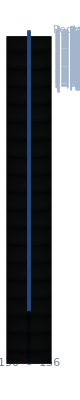

The evolution of the main branch in tableau up to 660 steps as color diagram:

-Graphics-

Final expression of the proof search in the NNF-calculus: ∃_{y(2),y(3),y(4),y(5),y(6),y(7)}(∀_(x(1,1))∃_{y(8,1),y(9,1),y(10,1),y(11,1)}(({Faux0(True,x(1,1),x(1,1),x(1,1),x(1,1),x(1,1),69),Faux0(True,y(7),y(7),y(7),y(7),y(7),1)}∨{P(False,y(8,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),70),P(False,y(8,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),2)})∧∀_{x(23,1,1),x(100,1,1),x(177,1,1),x(254,1,1),x(331,1,1)}({P(True,y(8,1),x(331,1,1),x(254,1,1),x(177,1,1),x(100,1,1),x(23,1,1),25),P(True,y(8,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),2)}∨{P1(False,y(11,1),x(331,1,1),x(254,1,1),x(177,1,1),x(100,1,1),x(23,1,1),26),P1(False,y(11,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),3)})∧∀_{x(25,1,1),x(102,1,1),x(179,1,1),x(256,1,1),x(333,1,1)}({P1(True,y(11,1),x(333,1,1),x(256,1,1),x(179,1,1),x(102,1,1),x(25,1,1),29),P1(True,y(11,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),3)}∨{FauxR(False,y(11,1),x(333,1,1),x(256,1,1),x(179,1,1),x(102,1,1),x(25,1,1),y(5),30),FauxR(False,y(11,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(5),4)})∧∀_{x(45,1,1),x(122,1,1),x(199,1,1),x(276,1,1),x(353,1,1),x(407,1,1)}({FauxR(True,x(407,1,1),y(10,1),x(353,1,1),x(276,1,1),x(199,1,1),x(122,1,1),x(45,1,1),71),FauxR(True,y(11,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(5),4)}∨{Faux1A3(False,y(10,1),x(1,1),y(7),x(353,1,1),x(276,1,1),x(199,1,1),x(407,1,1),x(122,1,1),x(45,1,1),72),Faux1A3(False,y(10,1),y(7),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),5)})∧∀_{x(46,1,1),x(123,1,1),x(200,1,1),x(277,1,1),x(354,1,1),x(408,1,1),x(431,1,1),x(448,1,1)}({Faux1A3(True,x(448,1,1),x(431,1,1),x(408,1,1),x(354,1,1),x(277,1,1),x(200,1,1),x(123,1,1),x(1,1),x(46,1,1),73),Faux1A3(True,y(10,1),y(7),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),5)}∨{Faux2(False,y(10,1),x(431,1,1),x(408,1,1),x(354,1,1),x(277,1,1),x(200,1,1),x(123,1,1),x(1,1),x(46,1,1),74),Faux2(False,y(10,1),y(7),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),6)})∧∀_{x(58,1,1),x(135,1,1),x(212,1,1),x(289,1,1),x(366,1,1)}({P1(True,y(10,1),x(366,1,1),x(289,1,1),x(212,1,1),x(135,1,1),x(58,1,1),97),P1(True,y(10,1),y(8,1),y(8,1),y(9,1),y(11,1),y(7),9)}∨{FauxR(False,y(10,1),x(366,1,1),x(289,1,1),x(212,1,1),x(135,1,1),x(58,1,1),y(6),98),FauxR(False,y(10,1),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(6),10)})∧∀_{x(29,1,1),x(106,1,1),x(183,1,1),x(260,1,1),x(337,1,1),x(401,1,1)}({FauxR(True,x(401,1,1),y(8,1),x(337,1,1),x(260,1,1),x(183,1,1),x(106,1,1),x(29,1,1),37),FauxR(True,y(10,1),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(6),10)}∨{Faux1A1(False,y(8,1),x(1,1),y(7),x(337,1,1),x(260,1,1),x(183,1,1),x(401,1,1),x(106,1,1),x(29,1,1),38),Faux1A1(False,y(8,1),y(7),y(7),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(6),11)})∧∀_{x(30,1,1),x(107,1,1),x(184,1,1),x(261,1,1),x(338,1,1),x(402,1,1),x(426,1,1),x(445,1,1)}({Faux1A1(True,x(445,1,1),x(426,1,1),x(402,1,1),x(338,1,1),x(261,1,1),x(184,1,1),x(107,1,1),x(1,1),x(30,1,1),39),Faux1A1(True,y(8,1),y(7),y(7),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(6),11)}∨{Faux2(False,y(8,1),x(426,1,1),x(402,1,1),x(338,1,1),x(261,1,1),x(184,1,1),x(107,1,1),x(1,1),x(30,1,1),40),Faux2(False,y(8,1),y(7),y(7),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(6),12)})∧∀_{x(23,1,2),x(100,1,2),x(177,1,2),x(254,1,2),x(331,1,2)}({P(True,y(8,1),x(331,1,2),x(254,1,2),x(177,1,2),x(100,1,2),x(23,1,2),25),P(True,y(8,1),y(8,1),y(9,1),y(11,1),y(10,1),y(7),15)}∨{P1(False,y(11,1),x(331,1,2),x(254,1,2),x(177,1,2),x(100,1,2),x(23,1,2),26),P1(False,y(11,1),y(8,1),y(9,1),y(11,1),y(10,1),y(7),16)})∧∀_{x(25,1,2),x(102,1,2),x(179,1,2),x(256,1,2),x(333,1,2)}({P1(True,y(11,1),x(333,1,2),x(256,1,2),x(179,1,2),x(102,1,2),x(25,1,2),29),P1(True,y(11,1),y(8,1),y(9,1),y(11,1),y(10,1),y(7),16)}∨{FauxR(False,y(11,1),x(333,1,2),x(256,1,2),x(179,1,2),x(102,1,2),x(25,1,2),y(5),30),FauxR(False,y(11,1),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(5),17)})∧∀_{x(29,1,2),x(106,1,2),x(183,1,2),x(260,1,2),x(337,1,2),x(401,1,2)}({FauxR(True,x(401,1,2),y(8,1),x(337,1,2),x(260,1,2),x(183,1,2),x(106,1,2),x(29,1,2),37),FauxR(True,y(11,1),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(5),17)}∨{Faux1A1(False,y(8,1),x(1,1),y(7),x(337,1,2),x(260,1,2),x(183,1,2),x(401,1,2),x(106,1,2),x(29,1,2),38),Faux1A1(False,y(8,1),y(7),y(7),y(9,1),y(11,1),y(10,1),y(11,1),y(7),y(5),18)})∧∀_{x(30,1,2),x(107,1,2),x(184,1,2),x(261,1,2),x(338,1,2),x(402,1,2),x(426,1,2),x(445,1,2)}({Faux1A1(True,x(445,1,2),x(426,1,2),x(402,1,2),x(338,1,2),x(261,1,2),x(184,1,2),x(107,1,2),x(1,1),x(30,1,2),39),Faux1A1(True,y(8,1),y(7),y(7),y(9,1),y(11,1),y(10,1),y(11,1),y(7),y(5),18)}∨{Faux2(False,y(8,1),x(426,1,2),x(402,1,2),x(338,1,2),x(261,1,2),x(184,1,2),x(107,1,2),x(1,1),x(30,1,2),40),Faux2(False,y(8,1),y(7),y(7),y(9,1),y(11,1),y(10,1),y(11,1),y(7),y(5),19)})∧∀_{x(41,1,1),x(118,1,1),x(195,1,1),x(272,1,1),x(349,1,1)}({P1(True,y(8,1),x(349,1,1),x(272,1,1),x(195,1,1),x(118,1,1),x(41,1,1),61),P1(True,y(8,1),y(9,1),y(11,1),y(10,1),y(11,1),y(7),22)}∨{FauxR(False,y(8,1),x(349,1,1),x(272,1,1),x(195,1,1),x(118,1,1),x(41,1,1),y(5),62),FauxR(False,y(8,1),y(9,1),y(11,1),y(10,1),y(11,1),y(7),y(5),23)})∧∀_{x(62,1,1),x(139,1,1),x(216,1,1),x(293,1,1),x(370,1,1),x(413,1,1)}({FauxR(True,x(413,1,1),y(9,1),x(370,1,1),x(293,1,1),x(216,1,1),x(139,1,1),x(62,1,1),105),FauxR(True,y(8,1),y(9,1),y(11,1),y(10,1),y(11,1),y(7),y(5),23)}∨{Faux1A4(False,y(9,1),x(1,1),y(7),x(370,1,1),x(293,1,1),x(216,1,1),x(413,1,1),x(139,1,1),x(62,1,1),106),Faux1A4(False,y(9,1),y(7),y(7),y(11,1),y(10,1),y(11,1),y(8,1),y(7),y(5),24)})∧∀_{x(63,1,1),x(140,1,1),x(217,1,1),x(294,1,1),x(371,1,1),x(414,1,1),x(436,1,1),x(451,1,1)}({Faux1A4(True,x(451,1,1),x(436,1,1),x(414,1,1),x(371,1,1),x(294,1,1),x(217,1,1),x(140,1,1),x(1,1),x(63,1,1),107),Faux1A4(True,y(9,1),y(7),y(7),y(11,1),y(10,1),y(11,1),y(8,1),y(7),y(5),24)}∨{Faux2(False,y(9,1),x(436,1,1),x(414,1,1),x(371,1,1),x(294,1,1),x(217,1,1),x(140,1,1),x(1,1),x(63,1,1),108),Faux2(False,y(9,1),y(7),y(7),y(11,1),y(10,1),y(11,1),y(8,1),y(7),y(5),25)})∧∀_{x(75,1,1),x(152,1,1),x(229,1,1),x(306,1,1),x(383,1,1)}({P1(True,y(9,1),x(383,1,1),x(306,1,1),x(229,1,1),x(152,1,1),x(75,1,1),131),P1(True,y(9,1),y(11,1),y(10,1),y(11,1),y(8,1),y(7),28)}∨{FauxR(False,y(9,1),x(383,1,1),x(306,1,1),x(229,1,1),x(152,1,1),x(75,1,1),y(6),132),FauxR(False,y(9,1),y(11,1),y(10,1),y(11,1),y(8,1),y(7),y(6),29)})∧∀_{x(11,1,1),x(88,1,1),x(165,1,1),x(242,1,1),x(319,1,1),x(395,1,1)}({FauxR(True,x(395,1,1),y(11,1),x(319,1,1),x(242,1,1),x(165,1,1),x(88,1,1),x(11,1,1),1),FauxR(True,y(9,1),y(11,1),y(10,1),y(11,1),y(8,1),y(7),y(6),29)}∨{Faux1A2(False,y(11,1),x(1,1),y(7),x(319,1,1),x(242,1,1),x(165,1,1),x(395,1,1),x(88,1,1),x(11,1,1),2),Faux1A2(False,y(11,1),y(7),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),30)})∧∀_{x(12,1,1),x(89,1,1),x(166,1,1),x(243,1,1),x(320,1,1),x(396,1,1),x(421,1,1),x(442,1,1)}({Faux1A2(True,x(442,1,1),x(421,1,1),x(396,1,1),x(320,1,1),x(243,1,1),x(166,1,1),x(89,1,1),x(1,1),x(12,1,1),3),Faux1A2(True,y(11,1),y(7),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),30)}∨{Faux2(False,y(11,1),x(421,1,1),x(396,1,1),x(320,1,1),x(243,1,1),x(166,1,1),x(89,1,1),x(1,1),x(12,1,1),4),Faux2(False,y(11,1),y(7),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),31)})∧∀_{x(24,1,1),x(101,1,1),x(178,1,1),x(255,1,1),x(332,1,1)}({P(True,y(11,1),x(332,1,1),x(255,1,1),x(178,1,1),x(101,1,1),x(24,1,1),27),P(True,y(11,1),y(10,1),y(11,1),y(8,1),y(9,1),y(7),34)}∨{FauxR(False,y(11,1),x(332,1,1),x(255,1,1),x(178,1,1),x(101,1,1),x(24,1,1),y(6),28),FauxR(False,y(11,1),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),35)})∧∀_{x(45,1,2),x(122,1,2),x(199,1,2),x(276,1,2),x(353,1,2),x(407,1,2)}({FauxR(True,x(407,1,2),y(10,1),x(353,1,2),x(276,1,2),x(199,1,2),x(122,1,2),x(45,1,2),71),FauxR(True,y(11,1),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),35)}∨{Faux1A3(False,y(10,1),x(1,1),y(7),x(353,1,2),x(276,1,2),x(199,1,2),x(407,1,2),x(122,1,2),x(45,1,2),72),Faux1A3(False,y(10,1),y(7),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),36)})∧∀_{x(46,1,2),x(123,1,2),x(200,1,2),x(277,1,2),x(354,1,2),x(408,1,2),x(431,1,2),x(448,1,2)}({Faux1A3(True,x(448,1,2),x(431,1,2),x(408,1,2),x(354,1,2),x(277,1,2),x(200,1,2),x(123,1,2),x(1,1),x(46,1,2),73),Faux1A3(True,y(10,1),y(7),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),36)}∨{Faux2(False,y(10,1),x(431,1,2),x(408,1,2),x(354,1,2),x(277,1,2),x(200,1,2),x(123,1,2),x(1,1),x(46,1,2),74),Faux2(False,y(10,1),y(7),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),37)})∧∀_{x(57,1,1),x(134,1,1),x(211,1,1),x(288,1,1),x(365,1,1)}({P(True,y(10,1),x(365,1,1),x(288,1,1),x(211,1,1),x(134,1,1),x(57,1,1),95),P(True,y(10,1),y(11,1),y(8,1),y(9,1),y(11,1),y(7),40)}∨{FauxR(False,y(10,1),x(365,1,1),x(288,1,1),x(211,1,1),x(134,1,1),x(57,1,1),y(2),96),FauxR(False,y(10,1),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(2),41)})∧∀_{x(11,1,2),x(88,1,2),x(165,1,2),x(242,1,2),x(319,1,2),x(395,1,2)}({FauxR(True,x(395,1,2),y(11,1),x(319,1,2),x(242,1,2),x(165,1,2),x(88,1,2),x(11,1,2),1),FauxR(True,y(10,1),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(2),41)}∨{Faux1A2(False,y(11,1),x(1,1),y(7),x(319,1,2),x(242,1,2),x(165,1,2),x(395,1,2),x(88,1,2),x(11,1,2),2),Faux1A2(False,y(11,1),y(7),y(7),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(2),42)})∧∀_{x(12,1,2),x(89,1,2),x(166,1,2),x(243,1,2),x(320,1,2),x(396,1,2),x(421,1,2),x(442,1,2)}({Faux1A2(True,x(442,1,2),x(421,1,2),x(396,1,2),x(320,1,2),x(243,1,2),x(166,1,2),x(89,1,2),x(1,1),x(12,1,2),3),Faux1A2(True,y(11,1),y(7),y(7),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(2),42)}∨{Faux2(False,y(11,1),x(421,1,2),x(396,1,2),x(320,1,2),x(243,1,2),x(166,1,2),x(89,1,2),x(1,1),x(12,1,2),4),Faux2(False,y(11,1),y(7),y(7),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(2),43)})∧∀_{x(26,1,1),x(103,1,1),x(180,1,1),x(257,1,1),x(334,1,1)}({P4(True,y(11,1),x(334,1,1),x(257,1,1),x(180,1,1),x(103,1,1),x(26,1,1),31),P4(True,y(11,1),y(8,1),y(9,1),y(11,1),y(10,1),y(7),46)}∨{P4(False,y(8,1),x(334,1,1),x(257,1,1),x(180,1,1),x(103,1,1),x(26,1,1),32),P4(False,y(8,1),y(8,1),y(9,1),y(11,1),y(10,1),y(7),47)})∧∀_{x(42,1,1),x(119,1,1),x(196,1,1),x(273,1,1),x(350,1,1)}({P4(True,y(8,1),x(350,1,1),x(273,1,1),x(196,1,1),x(119,1,1),x(42,1,1),63),P4(True,y(8,1),y(8,1),y(9,1),y(11,1),y(10,1),y(7),47)}∨{FauxR(False,y(8,1),x(350,1,1),x(273,1,1),x(196,1,1),x(119,1,1),x(42,1,1),y(2),64),FauxR(False,y(8,1),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(2),48)})∧∀_{x(29,1,3),x(106,1,3),x(183,1,3),x(260,1,3),x(337,1,3),x(401,1,3)}({FauxR(True,x(401,1,3),y(8,1),x(337,1,3),x(260,1,3),x(183,1,3),x(106,1,3),x(29,1,3),37),FauxR(True,y(8,1),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(2),48)}∨{Faux1A1(False,y(8,1),x(1,1),y(7),x(337,1,3),x(260,1,3),x(183,1,3),x(401,1,3),x(106,1,3),x(29,1,3),38),Faux1A1(False,y(8,1),y(7),y(7),y(9,1),y(11,1),y(10,1),y(8,1),y(7),y(2),49)})∧∀_{x(30,1,3),x(107,1,3),x(184,1,3),x(261,1,3),x(338,1,3),x(402,1,3),x(426,1,3),x(445,1,3)}({Faux1A1(True,x(445,1,3),x(426,1,3),x(402,1,3),x(338,1,3),x(261,1,3),x(184,1,3),x(107,1,3),x(1,1),x(30,1,3),39),Faux1A1(True,y(8,1),y(7),y(7),y(9,1),y(11,1),y(10,1),y(8,1),y(7),y(2),49)}∨{Faux2(False,y(8,1),x(426,1,3),x(402,1,3),x(338,1,3),x(261,1,3),x(184,1,3),x(107,1,3),x(1,1),x(30,1,3),40),Faux2(False,y(8,1),y(7),y(7),y(9,1),y(11,1),y(10,1),y(8,1),y(7),y(2),50)})∧∀_{x(42,1,2),x(119,1,2),x(196,1,2),x(273,1,2),x(350,1,2)}({P4(True,y(8,1),x(350,1,2),x(273,1,2),x(196,1,2),x(119,1,2),x(42,1,2),63),P4(True,y(8,1),y(9,1),y(11,1),y(10,1),y(8,1),y(7),53)}∨{FauxR(False,y(8,1),x(350,1,2),x(273,1,2),x(196,1,2),x(119,1,2),x(42,1,2),y(2),64),FauxR(False,y(8,1),y(9,1),y(11,1),y(10,1),y(8,1),y(7),y(2),54)})∧∀_{x(62,1,2),x(139,1,2),x(216,1,2),x(293,1,2),x(370,1,2),x(413,1,2)}({FauxR(True,x(413,1,2),y(9,1),x(370,1,2),x(293,1,2),x(216,1,2),x(139,1,2),x(62,1,2),105),FauxR(True,y(8,1),y(9,1),y(11,1),y(10,1),y(8,1),y(7),y(2),54)}∨{Faux1A4(False,y(9,1),x(1,1),y(7),x(370,1,2),x(293,1,2),x(216,1,2),x(413,1,2),x(139,1,2),x(62,1,2),106),Faux1A4(False,y(9,1),y(7),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),55)})∧∀_{x(63,1,2),x(140,1,2),x(217,1,2),x(294,1,2),x(371,1,2),x(414,1,2),x(436,1,2),x(451,1,2)}({Faux1A4(True,x(451,1,2),x(436,1,2),x(414,1,2),x(371,1,2),x(294,1,2),x(217,1,2),x(140,1,2),x(1,1),x(63,1,2),107),Faux1A4(True,y(9,1),y(7),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),55)}∨{Faux2(False,y(9,1),x(436,1,2),x(414,1,2),x(371,1,2),x(294,1,2),x(217,1,2),x(140,1,2),x(1,1),x(63,1,2),108),Faux2(False,y(9,1),y(7),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),56)})∧∀_{x(76,1,1),x(153,1,1),x(230,1,1),x(307,1,1),x(384,1,1)}({P4(True,y(9,1),x(384,1,1),x(307,1,1),x(230,1,1),x(153,1,1),x(76,1,1),133),P4(True,y(9,1),y(11,1),y(10,1),y(8,1),y(8,1),y(7),59)}∨{FauxR(False,y(9,1),x(384,1,1),x(307,1,1),x(230,1,1),x(153,1,1),x(76,1,1),y(2),134),FauxR(False,y(9,1),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),60)})∧∀_{x(11,1,3),x(88,1,3),x(165,1,3),x(242,1,3),x(319,1,3),x(395,1,3)}({FauxR(True,x(395,1,3),y(11,1),x(319,1,3),x(242,1,3),x(165,1,3),x(88,1,3),x(11,1,3),1),FauxR(True,y(9,1),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),60)}∨{Faux1A2(False,y(11,1),x(1,1),y(7),x(319,1,3),x(242,1,3),x(165,1,3),x(395,1,3),x(88,1,3),x(11,1,3),2),Faux1A2(False,y(11,1),y(7),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),61)})∧∀_{x(12,1,3),x(89,1,3),x(166,1,3),x(243,1,3),x(320,1,3),x(396,1,3),x(421,1,3),x(442,1,3)}({Faux1A2(True,x(442,1,3),x(421,1,3),x(396,1,3),x(320,1,3),x(243,1,3),x(166,1,3),x(89,1,3),x(1,1),x(12,1,3),3),Faux1A2(True,y(11,1),y(7),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),61)}∨{Faux2(False,y(11,1),x(421,1,3),x(396,1,3),x(320,1,3),x(243,1,3),x(166,1,3),x(89,1,3),x(1,1),x(12,1,3),4),Faux2(False,y(11,1),y(7),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),62)})∧∀_{x(26,1,2),x(103,1,2),x(180,1,2),x(257,1,2),x(334,1,2)}({P4(True,y(11,1),x(334,1,2),x(257,1,2),x(180,1,2),x(103,1,2),x(26,1,2),31),P4(True,y(11,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),65)}∨{P4(False,y(8,1),x(334,1,2),x(257,1,2),x(180,1,2),x(103,1,2),x(26,1,2),32),P4(False,y(8,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),66)})∧∀_{x(42,1,3),x(119,1,3),x(196,1,3),x(273,1,3),x(350,1,3)}({P4(True,y(8,1),x(350,1,3),x(273,1,3),x(196,1,3),x(119,1,3),x(42,1,3),63),P4(True,y(8,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),66)}∨{FauxR(False,y(8,1),x(350,1,3),x(273,1,3),x(196,1,3),x(119,1,3),x(42,1,3),y(2),64),FauxR(False,y(8,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),67)})∧∀_{x(45,1,3),x(122,1,3),x(199,1,3),x(276,1,3),x(353,1,3),x(407,1,3)}({FauxR(True,x(407,1,3),y(10,1),x(353,1,3),x(276,1,3),x(199,1,3),x(122,1,3),x(45,1,3),71),FauxR(True,y(8,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),67)}∨{Faux1A3(False,y(10,1),x(1,1),y(7),x(353,1,3),x(276,1,3),x(199,1,3),x(407,1,3),x(122,1,3),x(45,1,3),72),Faux1A3(False,y(10,1),y(7),y(7),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(2),68)})∧∀_{x(46,1,3),x(123,1,3),x(200,1,3),x(277,1,3),x(354,1,3),x(408,1,3),x(431,1,3),x(448,1,3)}({Faux1A3(True,x(448,1,3),x(431,1,3),x(408,1,3),x(354,1,3),x(277,1,3),x(200,1,3),x(123,1,3),x(1,1),x(46,1,3),73),Faux1A3(True,y(10,1),y(7),y(7),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(2),68)}∨{Faux2(False,y(10,1),x(431,1,3),x(408,1,3),x(354,1,3),x(277,1,3),x(200,1,3),x(123,1,3),x(1,1),x(46,1,3),74),Faux2(False,y(10,1),y(7),y(7),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(2),69)})∧∀_{x(59,1,1),x(136,1,1),x(213,1,1),x(290,1,1),x(367,1,1)}({P4(True,y(10,1),x(367,1,1),x(290,1,1),x(213,1,1),x(136,1,1),x(59,1,1),99),P4(True,y(10,1),y(8,1),y(8,1),y(9,1),y(8,1),y(7),72)}∨{FauxR(False,y(10,1),x(367,1,1),x(290,1,1),x(213,1,1),x(136,1,1),x(59,1,1),y(4),100),FauxR(False,y(10,1),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(4),73)})∧∀_{x(29,1,4),x(106,1,4),x(183,1,4),x(260,1,4),x(337,1,4),x(401,1,4)}({FauxR(True,x(401,1,4),y(8,1),x(337,1,4),x(260,1,4),x(183,1,4),x(106,1,4),x(29,1,4),37),FauxR(True,y(10,1),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(4),73)}∨{Faux1A1(False,y(8,1),x(1,1),y(7),x(337,1,4),x(260,1,4),x(183,1,4),x(401,1,4),x(106,1,4),x(29,1,4),38),Faux1A1(False,y(8,1),y(7),y(7),y(8,1),y(9,1),y(8,1),y(10,1),y(7),y(4),74)})∧∀_{x(30,1,4),x(107,1,4),x(184,1,4),x(261,1,4),x(338,1,4),x(402,1,4),x(426,1,4),x(445,1,4)}({Faux1A1(True,x(445,1,4),x(426,1,4),x(402,1,4),x(338,1,4),x(261,1,4),x(184,1,4),x(107,1,4),x(1,1),x(30,1,4),39),Faux1A1(True,y(8,1),y(7),y(7),y(8,1),y(9,1),y(8,1),y(10,1),y(7),y(4),74)}∨{Faux2(False,y(8,1),x(426,1,4),x(402,1,4),x(338,1,4),x(261,1,4),x(184,1,4),x(107,1,4),x(1,1),x(30,1,4),40),Faux2(False,y(8,1),y(7),y(7),y(8,1),y(9,1),y(8,1),y(10,1),y(7),y(4),75)})∧∀_{x(43,1,1),x(120,1,1),x(197,1,1),x(274,1,1),x(351,1,1)}({P2(True,y(8,1),x(351,1,1),x(274,1,1),x(197,1,1),x(120,1,1),x(43,1,1),65),P2(True,y(8,1),y(8,1),y(9,1),y(8,1),y(10,1),y(7),78)}∨{FauxR(False,y(8,1),x(351,1,1),x(274,1,1),x(197,1,1),x(120,1,1),x(43,1,1),y(4),66),FauxR(False,y(8,1),y(8,1),y(9,1),y(8,1),y(10,1),y(7),y(4),79)})∧∀_{x(29,1,5),x(106,1,5),x(183,1,5),x(260,1,5),x(337,1,5),x(401,1,5)}({FauxR(True,x(401,1,5),y(8,1),x(337,1,5),x(260,1,5),x(183,1,5),x(106,1,5),x(29,1,5),37),FauxR(True,y(8,1),y(8,1),y(9,1),y(8,1),y(10,1),y(7),y(4),79)}∨{Faux1A1(False,y(8,1),x(1,1),y(7),x(337,1,5),x(260,1,5),x(183,1,5),x(401,1,5),x(106,1,5),x(29,1,5),38),Faux1A1(False,y(8,1),y(7),y(7),y(9,1),y(8,1),y(10,1),y(8,1),y(7),y(4),80)})∧∀_{x(30,1,5),x(107,1,5),x(184,1,5),x(261,1,5),x(338,1,5),x(402,1,5),x(426,1,5),x(445,1,5)}({Faux1A1(True,x(445,1,5),x(426,1,5),x(402,1,5),x(338,1,5),x(261,1,5),x(184,1,5),x(107,1,5),x(1,1),x(30,1,5),39),Faux1A1(True,y(8,1),y(7),y(7),y(9,1),y(8,1),y(10,1),y(8,1),y(7),y(4),80)}∨{Faux2(False,y(8,1),x(426,1,5),x(402,1,5),x(338,1,5),x(261,1,5),x(184,1,5),x(107,1,5),x(1,1),x(30,1,5),40),Faux2(False,y(8,1),y(7),y(7),y(9,1),y(8,1),y(10,1),y(8,1),y(7),y(4),81)})∧∀_{x(43,1,2),x(120,1,2),x(197,1,2),x(274,1,2),x(351,1,2)}({P2(True,y(8,1),x(351,1,2),x(274,1,2),x(197,1,2),x(120,1,2),x(43,1,2),65),P2(True,y(8,1),y(9,1),y(8,1),y(10,1),y(8,1),y(7),84)}∨{FauxR(False,y(8,1),x(351,1,2),x(274,1,2),x(197,1,2),x(120,1,2),x(43,1,2),y(4),66),FauxR(False,y(8,1),y(9,1),y(8,1),y(10,1),y(8,1),y(7),y(4),85)})∧∀_{x(62,1,3),x(139,1,3),x(216,1,3),x(293,1,3),x(370,1,3),x(413,1,3)}({FauxR(True,x(413,1,3),y(9,1),x(370,1,3),x(293,1,3),x(216,1,3),x(139,1,3),x(62,1,3),105),FauxR(True,y(8,1),y(9,1),y(8,1),y(10,1),y(8,1),y(7),y(4),85)}∨{Faux1A4(False,y(9,1),x(1,1),y(7),x(370,1,3),x(293,1,3),x(216,1,3),x(413,1,3),x(139,1,3),x(62,1,3),106),Faux1A4(False,y(9,1),y(7),y(7),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(4),86)})∧∀_{x(63,1,3),x(140,1,3),x(217,1,3),x(294,1,3),x(371,1,3),x(414,1,3),x(436,1,3),x(451,1,3)}({Faux1A4(True,x(451,1,3),x(436,1,3),x(414,1,3),x(371,1,3),x(294,1,3),x(217,1,3),x(140,1,3),x(1,1),x(63,1,3),107),Faux1A4(True,y(9,1),y(7),y(7),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(4),86)}∨{Faux2(False,y(9,1),x(436,1,3),x(414,1,3),x(371,1,3),x(294,1,3),x(217,1,3),x(140,1,3),x(1,1),x(63,1,3),108),Faux2(False,y(9,1),y(7),y(7),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(4),87)})∧∀_{x(77,1,1),x(154,1,1),x(231,1,1),x(308,1,1),x(385,1,1)}({P2(True,y(9,1),x(385,1,1),x(308,1,1),x(231,1,1),x(154,1,1),x(77,1,1),135),P2(True,y(9,1),y(8,1),y(10,1),y(8,1),y(8,1),y(7),90)}∨{FauxR(False,y(9,1),x(385,1,1),x(308,1,1),x(231,1,1),x(154,1,1),x(77,1,1),y(3),136),FauxR(False,y(9,1),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(3),91)})∧∀_{x(29,1,6),x(106,1,6),x(183,1,6),x(260,1,6),x(337,1,6),x(401,1,6)}({FauxR(True,x(401,1,6),y(8,1),x(337,1,6),x(260,1,6),x(183,1,6),x(106,1,6),x(29,1,6),37),FauxR(True,y(9,1),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(3),91)}∨{Faux1A1(False,y(8,1),x(1,1),y(7),x(337,1,6),x(260,1,6),x(183,1,6),x(401,1,6),x(106,1,6),x(29,1,6),38),Faux1A1(False,y(8,1),y(7),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(3),92)})∧∀_{x(30,1,6),x(107,1,6),x(184,1,6),x(261,1,6),x(338,1,6),x(402,1,6),x(426,1,6),x(445,1,6)}({Faux1A1(True,x(445,1,6),x(426,1,6),x(402,1,6),x(338,1,6),x(261,1,6),x(184,1,6),x(107,1,6),x(1,1),x(30,1,6),39),Faux1A1(True,y(8,1),y(7),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(3),92)}∨{Faux2(False,y(8,1),x(426,1,6),x(402,1,6),x(338,1,6),x(261,1,6),x(184,1,6),x(107,1,6),x(1,1),x(30,1,6),40),Faux2(False,y(8,1),y(7),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(3),93)})∧∀_{x(44,1,1),x(121,1,1),x(198,1,1),x(275,1,1),x(352,1,1)}({P3(True,y(8,1),x(352,1,1),x(275,1,1),x(198,1,1),x(121,1,1),x(44,1,1),67),P3(True,y(8,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),96)}∨{FauxS1(False,y(8,1),x(352,1,1),x(275,1,1),x(198,1,1),x(121,1,1),x(44,1,1),y(6),68),FauxS1(False,y(8,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(6),97)})∧∀_{x(23,1,3),x(100,1,3),x(177,1,3),x(254,1,3),x(331,1,3)}({P(True,y(8,1),x(331,1,3),x(254,1,3),x(177,1,3),x(100,1,3),x(23,1,3),25),P(True,y(8,1),y(8,2),y(8,1),y(8,1),y(9,1),y(7),98)}∨{P1(False,y(11,1),x(331,1,3),x(254,1,3),x(177,1,3),x(100,1,3),x(23,1,3),26),P1(False,y(11,1),y(8,2),y(8,1),y(8,1),y(9,1),y(7),99)})∧∀_{x(25,1,3),x(102,1,3),x(179,1,3),x(256,1,3),x(333,1,3)}({P1(True,y(11,1),x(333,1,3),x(256,1,3),x(179,1,3),x(102,1,3),x(25,1,3),29),P1(True,y(11,1),y(8,2),y(8,1),y(8,1),y(9,1),y(7),99)}∨{FauxR(False,y(11,1),x(333,1,3),x(256,1,3),x(179,1,3),x(102,1,3),x(25,1,3),y(5),30),FauxR(False,y(11,1),y(8,2),y(8,1),y(8,1),y(9,1),y(7),y(5),100)})∧∀_{x(30,1,7),x(107,1,7),x(184,1,7),x(261,1,7),x(338,1,7),x(402,1,7),x(426,1,7),x(445,1,7)}({Faux1A1(True,x(445,1,7),x(426,1,7),x(402,1,7),x(338,1,7),x(261,1,7),x(184,1,7),x(107,1,7),x(1,1),x(30,1,7),39),Faux1A1(True,y(8,2),y(10,1),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),101)}∨{Faux2(False,y(8,1),x(426,1,7),x(402,1,7),x(338,1,7),x(261,1,7),x(184,1,7),x(107,1,7),x(1,1),x(30,1,7),40),Faux2(False,y(8,1),y(10,1),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),102)})∧∀_{x(47,1,1),x(124,1,1),x(201,1,1),x(278,1,1),x(355,1,1),x(409,1,1),x(432,1,1),x(449,1,1)}({Faux2(True,x(449,1,1),y(10,1),x(432,1,1),x(409,1,1),x(355,1,1),x(278,1,1),x(201,1,1),x(124,1,1),x(47,1,1),75),Faux2(True,y(8,1),y(10,1),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),102)}∨{Faux3A3(False,x(449,1,1),x(1,1),x(432,1,1),x(409,1,1),x(355,1,1),x(278,1,1),x(201,1,1),x(124,1,1),x(47,1,1),76),Faux3A3(False,y(8,1),y(7),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),103)})∧∀_{x(48,1,1),x(125,1,1),x(202,1,1),x(279,1,1),x(356,1,1),x(410,1,1),x(433,1,1),x(450,1,1)}({Faux3A3(True,x(450,1,1),x(433,1,1),x(1,1),x(410,1,1),x(356,1,1),x(279,1,1),x(202,1,1),x(125,1,1),x(48,1,1),77),Faux3A3(True,y(8,1),y(7),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),103)}∨{Faux2(False,x(450,1,1),x(433,1,1),y(10,1),x(410,1,1),x(356,1,1),x(279,1,1),x(202,1,1),x(125,1,1),x(48,1,1),78),Faux2(False,y(8,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),104)})∧∀_{x(49,1,1),x(126,1,1),x(203,1,1),x(280,1,1),x(357,1,1),x(411,1,1),x(434,1,1)}({Faux4(True,x(434,1,1),y(10,1),x(411,1,1),x(357,1,1),x(280,1,1),x(203,1,1),x(126,1,1),x(49,1,1),79),Faux4(True,y(8,1),y(10,1),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),105)}∨{Faux5A3(False,x(434,1,1),x(1,1),x(411,1,1),x(357,1,1),x(280,1,1),x(203,1,1),x(126,1,1),x(49,1,1),80),Faux5A3(False,y(8,1),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),106)})∧∀_{x(41,1,2),x(118,1,2),x(195,1,2),x(272,1,2),x(349,1,2)}({P1(True,y(8,1),x(349,1,2),x(272,1,2),x(195,1,2),x(118,1,2),x(41,1,2),61),P1(True,y(8,1),y(10,2),y(8,1),y(9,1),y(11,1),y(7),109)}∨{FauxR(False,y(8,1),x(349,1,2),x(272,1,2),x(195,1,2),x(118,1,2),x(41,1,2),y(5),62),FauxR(False,y(8,1),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(5),110)})∧∀_{x(46,1,4),x(123,1,4),x(200,1,4),x(277,1,4),x(354,1,4),x(408,1,4),x(431,1,4),x(448,1,4)}({Faux1A3(True,x(448,1,4),x(431,1,4),x(408,1,4),x(354,1,4),x(277,1,4),x(200,1,4),x(123,1,4),x(1,1),x(46,1,4),73),Faux1A3(True,y(10,2),y(8,1),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),111)}∨{Faux2(False,y(10,1),x(431,1,4),x(408,1,4),x(354,1,4),x(277,1,4),x(200,1,4),x(123,1,4),x(1,1),x(46,1,4),74),Faux2(False,y(10,1),y(8,1),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),112)})∧∀_{x(31,1,1),x(108,1,1),x(185,1,1),x(262,1,1),x(339,1,1),x(403,1,1),x(427,1,1),x(446,1,1)}({Faux2(True,x(446,1,1),y(8,1),x(427,1,1),x(403,1,1),x(339,1,1),x(262,1,1),x(185,1,1),x(108,1,1),x(31,1,1),41),Faux2(True,y(10,1),y(8,1),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),112)}∨{Faux3A1(False,x(446,1,1),x(1,1),x(427,1,1),x(403,1,1),x(339,1,1),x(262,1,1),x(185,1,1),x(108,1,1),x(31,1,1),42),Faux3A1(False,y(10,1),y(7),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),113)})∧∀_{x(32,1,1),x(109,1,1),x(186,1,1),x(263,1,1),x(340,1,1),x(404,1,1),x(428,1,1),x(447,1,1)}({Faux3A1(True,x(447,1,1),x(428,1,1),x(1,1),x(404,1,1),x(340,1,1),x(263,1,1),x(186,1,1),x(109,1,1),x(32,1,1),43),Faux3A1(True,y(10,1),y(7),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),113)}∨{Faux2(False,x(447,1,1),x(428,1,1),y(8,1),x(404,1,1),x(340,1,1),x(263,1,1),x(186,1,1),x(109,1,1),x(32,1,1),44),Faux2(False,y(10,1),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),114)})∧∀_{x(33,1,1),x(110,1,1),x(187,1,1),x(264,1,1),x(341,1,1),x(405,1,1),x(429,1,1)}({Faux4(True,x(429,1,1),y(8,1),x(405,1,1),x(341,1,1),x(264,1,1),x(187,1,1),x(110,1,1),x(33,1,1),45),Faux4(True,y(10,1),y(8,1),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),115)}∨{Faux5A1(False,x(429,1,1),x(1,1),x(405,1,1),x(341,1,1),x(264,1,1),x(187,1,1),x(110,1,1),x(33,1,1),46),Faux5A1(False,y(10,1),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),116)})∧∀_{x(58,1,2),x(135,1,2),x(212,1,2),x(289,1,2),x(366,1,2)}({P1(True,y(10,1),x(366,1,2),x(289,1,2),x(212,1,2),x(135,1,2),x(58,1,2),97),P1(True,y(10,1),y(8,2),y(9,1),y(11,1),y(8,1),y(7),119)}∨{FauxR(False,y(10,1),x(366,1,2),x(289,1,2),x(212,1,2),x(135,1,2),x(58,1,2),y(6),98),FauxR(False,y(10,1),y(8,2),y(9,1),y(11,1),y(8,1),y(7),y(6),120)})∧∀_{x(30,1,8),x(107,1,8),x(184,1,8),x(261,1,8),x(338,1,8),x(402,1,8),x(426,1,8),x(445,1,8)}({Faux1A1(True,x(445,1,8),x(426,1,8),x(402,1,8),x(338,1,8),x(261,1,8),x(184,1,8),x(107,1,8),x(1,1),x(30,1,8),39),Faux1A1(True,y(8,2),y(8,1),y(7),y(9,1),y(11,1),y(8,1),y(10,1),y(7),y(6),121)}∨{Faux2(False,y(8,1),x(426,1,8),x(402,1,8),x(338,1,8),x(261,1,8),x(184,1,8),x(107,1,8),x(1,1),x(30,1,8),40),Faux2(False,y(8,1),y(8,1),y(7),y(9,1),y(11,1),y(8,1),y(10,1),y(7),y(6),122)})∧∀_{x(31,1,2),x(108,1,2),x(185,1,2),x(262,1,2),x(339,1,2),x(403,1,2),x(427,1,2),x(446,1,2)}({Faux2(True,x(446,1,2),y(8,1),x(427,1,2),x(403,1,2),x(339,1,2),x(262,1,2),x(185,1,2),x(108,1,2),x(31,1,2),41),Faux2(True,y(8,1),y(8,1),y(7),y(9,1),y(11,1),y(8,1),y(10,1),y(7),y(6),122)}∨{Faux3A1(False,x(446,1,2),x(1,1),x(427,1,2),x(403,1,2),x(339,1,2),x(262,1,2),x(185,1,2),x(108,1,2),x(31,1,2),42),Faux3A1(False,y(8,1),y(7),y(7),y(9,1),y(11,1),y(8,1),y(10,1),y(7),y(6),123)})∧∀_{x(32,1,2),x(109,1,2),x(186,1,2),x(263,1,2),x(340,1,2),x(404,1,2),x(428,1,2),x(447,1,2)}({Faux3A1(True,x(447,1,2),x(428,1,2),x(1,1),x(404,1,2),x(340,1,2),x(263,1,2),x(186,1,2),x(109,1,2),x(32,1,2),43),Faux3A1(True,y(8,1),y(7),y(7),y(9,1),y(11,1),y(8,1),y(10,1),y(7),y(6),123)}∨{Faux2(False,x(447,1,2),x(428,1,2),y(8,1),x(404,1,2),x(340,1,2),x(263,1,2),x(186,1,2),x(109,1,2),x(32,1,2),44),Faux2(False,y(8,1),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(10,1),y(7),y(6),124)})∧∀_{x(33,1,2),x(110,1,2),x(187,1,2),x(264,1,2),x(341,1,2),x(405,1,2),x(429,1,2)}({Faux4(True,x(429,1,2),y(8,1),x(405,1,2),x(341,1,2),x(264,1,2),x(187,1,2),x(110,1,2),x(33,1,2),45),Faux4(True,y(8,1),y(8,1),y(9,1),y(11,1),y(8,1),y(10,1),y(7),y(6),125)}∨{Faux5A1(False,x(429,1,2),x(1,1),x(405,1,2),x(341,1,2),x(264,1,2),x(187,1,2),x(110,1,2),x(33,1,2),46),Faux5A1(False,y(8,1),y(7),y(9,1),y(11,1),y(8,1),y(10,1),y(7),y(6),126)})∧∀_{x(23,1,4),x(100,1,4),x(177,1,4),x(254,1,4),x(331,1,4)}({P(True,y(8,1),x(331,1,4),x(254,1,4),x(177,1,4),x(100,1,4),x(23,1,4),25),P(True,y(8,1),y(8,2),y(11,1),y(8,1),y(10,1),y(7),129)}∨{P1(False,y(11,1),x(331,1,4),x(254,1,4),x(177,1,4),x(100,1,4),x(23,1,4),26),P1(False,y(11,1),y(8,2),y(11,1),y(8,1),y(10,1),y(7),130)})∧∀_{x(25,1,4),x(102,1,4),x(179,1,4),x(256,1,4),x(333,1,4)}({P1(True,y(11,1),x(333,1,4),x(256,1,4),x(179,1,4),x(102,1,4),x(25,1,4),29),P1(True,y(11,1),y(8,2),y(11,1),y(8,1),y(10,1),y(7),130)}∨{FauxR(False,y(11,1),x(333,1,4),x(256,1,4),x(179,1,4),x(102,1,4),x(25,1,4),y(5),30),FauxR(False,y(11,1),y(8,2),y(11,1),y(8,1),y(10,1),y(7),y(5),131)})∧∀_{x(30,1,9),x(107,1,9),x(184,1,9),x(261,1,9),x(338,1,9),x(402,1,9),x(426,1,9),x(445,1,9)}({Faux1A1(True,x(445,1,9),x(426,1,9),x(402,1,9),x(338,1,9),x(261,1,9),x(184,1,9),x(107,1,9),x(1,1),x(30,1,9),39),Faux1A1(True,y(8,2),y(9,1),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(5),132)}∨{Faux2(False,y(8,1),x(426,1,9),x(402,1,9),x(338,1,9),x(261,1,9),x(184,1,9),x(107,1,9),x(1,1),x(30,1,9),40),Faux2(False,y(8,1),y(9,1),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(5),133)})∧∀_{x(64,1,1),x(141,1,1),x(218,1,1),x(295,1,1),x(372,1,1),x(415,1,1),x(437,1,1),x(452,1,1)}({Faux2(True,x(452,1,1),y(9,1),x(437,1,1),x(415,1,1),x(372,1,1),x(295,1,1),x(218,1,1),x(141,1,1),x(64,1,1),109),Faux2(True,y(8,1),y(9,1),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(5),133)}∨{Faux3A4(False,x(452,1,1),x(1,1),x(437,1,1),x(415,1,1),x(372,1,1),x(295,1,1),x(218,1,1),x(141,1,1),x(64,1,1),110),Faux3A4(False,y(8,1),y(7),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(5),134)})∧∀_{x(65,1,1),x(142,1,1),x(219,1,1),x(296,1,1),x(373,1,1),x(416,1,1),x(438,1,1),x(453,1,1)}({Faux3A4(True,x(453,1,1),x(438,1,1),x(1,1),x(416,1,1),x(373,1,1),x(296,1,1),x(219,1,1),x(142,1,1),x(65,1,1),111),Faux3A4(True,y(8,1),y(7),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(5),134)}∨{Faux2(False,x(453,1,1),x(438,1,1),y(9,1),x(416,1,1),x(373,1,1),x(296,1,1),x(219,1,1),x(142,1,1),x(65,1,1),112),Faux2(False,y(8,1),y(7),y(9,1),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(5),135)})∧∀_{x(66,1,1),x(143,1,1),x(220,1,1),x(297,1,1),x(374,1,1),x(417,1,1),x(439,1,1)}({Faux4(True,x(439,1,1),y(9,1),x(417,1,1),x(374,1,1),x(297,1,1),x(220,1,1),x(143,1,1),x(66,1,1),113),Faux4(True,y(8,1),y(9,1),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(5),136)}∨{Faux5A4(False,x(439,1,1),x(1,1),x(417,1,1),x(374,1,1),x(297,1,1),x(220,1,1),x(143,1,1),x(66,1,1),114),Faux5A4(False,y(8,1),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(5),137)})∧∀_{x(41,1,3),x(118,1,3),x(195,1,3),x(272,1,3),x(349,1,3)}({P1(True,y(8,1),x(349,1,3),x(272,1,3),x(195,1,3),x(118,1,3),x(41,1,3),61),P1(True,y(8,1),y(9,2),y(8,1),y(10,1),y(11,1),y(7),140)}∨{FauxR(False,y(8,1),x(349,1,3),x(272,1,3),x(195,1,3),x(118,1,3),x(41,1,3),y(5),62),FauxR(False,y(8,1),y(9,2),y(8,1),y(10,1),y(11,1),y(7),y(5),141)})∧∀_{x(63,1,4),x(140,1,4),x(217,1,4),x(294,1,4),x(371,1,4),x(414,1,4),x(436,1,4),x(451,1,4)}({Faux1A4(True,x(451,1,4),x(436,1,4),x(414,1,4),x(371,1,4),x(294,1,4),x(217,1,4),x(140,1,4),x(1,1),x(63,1,4),107),Faux1A4(True,y(9,2),y(11,1),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),142)}∨{Faux2(False,y(9,1),x(436,1,4),x(414,1,4),x(371,1,4),x(294,1,4),x(217,1,4),x(140,1,4),x(1,1),x(63,1,4),108),Faux2(False,y(9,1),y(11,1),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),143)})∧∀_{x(13,1,1),x(90,1,1),x(167,1,1),x(244,1,1),x(321,1,1),x(397,1,1),x(422,1,1),x(443,1,1)}({Faux2(True,x(443,1,1),y(11,1),x(422,1,1),x(397,1,1),x(321,1,1),x(244,1,1),x(167,1,1),x(90,1,1),x(13,1,1),5),Faux2(True,y(9,1),y(11,1),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),143)}∨{Faux3A2(False,x(443,1,1),x(1,1),x(422,1,1),x(397,1,1),x(321,1,1),x(244,1,1),x(167,1,1),x(90,1,1),x(13,1,1),6),Faux3A2(False,y(9,1),y(7),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),144)})∧∀_{x(14,1,1),x(91,1,1),x(168,1,1),x(245,1,1),x(322,1,1),x(398,1,1),x(423,1,1),x(444,1,1)}({Faux3A2(True,x(444,1,1),x(423,1,1),x(1,1),x(398,1,1),x(322,1,1),x(245,1,1),x(168,1,1),x(91,1,1),x(14,1,1),7),Faux3A2(True,y(9,1),y(7),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),144)}∨{Faux2(False,x(444,1,1),x(423,1,1),y(11,1),x(398,1,1),x(322,1,1),x(245,1,1),x(168,1,1),x(91,1,1),x(14,1,1),8),Faux2(False,y(9,1),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),145)})∧∀_{x(15,1,1),x(92,1,1),x(169,1,1),x(246,1,1),x(323,1,1),x(399,1,1),x(424,1,1)}({Faux4(True,x(424,1,1),y(11,1),x(399,1,1),x(323,1,1),x(246,1,1),x(169,1,1),x(92,1,1),x(15,1,1),9),Faux4(True,y(9,1),y(11,1),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),146)}∨{Faux5A2(False,x(424,1,1),x(1,1),x(399,1,1),x(323,1,1),x(246,1,1),x(169,1,1),x(92,1,1),x(15,1,1),10),Faux5A2(False,y(9,1),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),147)})∧∀_{x(75,1,2),x(152,1,2),x(229,1,2),x(306,1,2),x(383,1,2)}({P1(True,y(9,1),x(383,1,2),x(306,1,2),x(229,1,2),x(152,1,2),x(75,1,2),131),P1(True,y(9,1),y(11,2),y(10,1),y(11,1),y(8,1),y(7),150)}∨{FauxR(False,y(9,1),x(383,1,2),x(306,1,2),x(229,1,2),x(152,1,2),x(75,1,2),y(6),132),FauxR(False,y(9,1),y(11,2),y(10,1),y(11,1),y(8,1),y(7),y(6),151)})∧∀_{x(12,1,4),x(89,1,4),x(166,1,4),x(243,1,4),x(320,1,4),x(396,1,4),x(421,1,4),x(442,1,4)}({Faux1A2(True,x(442,1,4),x(421,1,4),x(396,1,4),x(320,1,4),x(243,1,4),x(166,1,4),x(89,1,4),x(1,1),x(12,1,4),3),Faux1A2(True,y(11,2),y(8,1),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),152)}∨{Faux2(False,y(11,1),x(421,1,4),x(396,1,4),x(320,1,4),x(243,1,4),x(166,1,4),x(89,1,4),x(1,1),x(12,1,4),4),Faux2(False,y(11,1),y(8,1),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),153)})∧∀_{x(31,1,3),x(108,1,3),x(185,1,3),x(262,1,3),x(339,1,3),x(403,1,3),x(427,1,3),x(446,1,3)}({Faux2(True,x(446,1,3),y(8,1),x(427,1,3),x(403,1,3),x(339,1,3),x(262,1,3),x(185,1,3),x(108,1,3),x(31,1,3),41),Faux2(True,y(11,1),y(8,1),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),153)}∨{Faux3A1(False,x(446,1,3),x(1,1),x(427,1,3),x(403,1,3),x(339,1,3),x(262,1,3),x(185,1,3),x(108,1,3),x(31,1,3),42),Faux3A1(False,y(11,1),y(7),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),154)})∧∀_{x(32,1,3),x(109,1,3),x(186,1,3),x(263,1,3),x(340,1,3),x(404,1,3),x(428,1,3),x(447,1,3)}({Faux3A1(True,x(447,1,3),x(428,1,3),x(1,1),x(404,1,3),x(340,1,3),x(263,1,3),x(186,1,3),x(109,1,3),x(32,1,3),43),Faux3A1(True,y(11,1),y(7),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),154)}∨{Faux2(False,x(447,1,3),x(428,1,3),y(8,1),x(404,1,3),x(340,1,3),x(263,1,3),x(186,1,3),x(109,1,3),x(32,1,3),44),Faux2(False,y(11,1),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),155)})∧∀_{x(33,1,3),x(110,1,3),x(187,1,3),x(264,1,3),x(341,1,3),x(405,1,3),x(429,1,3)}({Faux4(True,x(429,1,3),y(8,1),x(405,1,3),x(341,1,3),x(264,1,3),x(187,1,3),x(110,1,3),x(33,1,3),45),Faux4(True,y(11,1),y(8,1),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),156)}∨{Faux5A1(False,x(429,1,3),x(1,1),x(405,1,3),x(341,1,3),x(264,1,3),x(187,1,3),x(110,1,3),x(33,1,3),46),Faux5A1(False,y(11,1),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),157)})∧∀_{x(24,1,2),x(101,1,2),x(178,1,2),x(255,1,2),x(332,1,2)}({P(True,y(11,1),x(332,1,2),x(255,1,2),x(178,1,2),x(101,1,2),x(24,1,2),27),P(True,y(11,1),y(8,2),y(11,1),y(8,1),y(9,1),y(7),160)}∨{FauxR(False,y(11,1),x(332,1,2),x(255,1,2),x(178,1,2),x(101,1,2),x(24,1,2),y(6),28),FauxR(False,y(11,1),y(8,2),y(11,1),y(8,1),y(9,1),y(7),y(6),161)})∧∀_{x(30,1,10),x(107,1,10),x(184,1,10),x(261,1,10),x(338,1,10),x(402,1,10),x(426,1,10),x(445,1,10)}({Faux1A1(True,x(445,1,10),x(426,1,10),x(402,1,10),x(338,1,10),x(261,1,10),x(184,1,10),x(107,1,10),x(1,1),x(30,1,10),39),Faux1A1(True,y(8,2),y(10,1),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),162)}∨{Faux2(False,y(8,1),x(426,1,10),x(402,1,10),x(338,1,10),x(261,1,10),x(184,1,10),x(107,1,10),x(1,1),x(30,1,10),40),Faux2(False,y(8,1),y(10,1),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),163)})∧∀_{x(47,1,2),x(124,1,2),x(201,1,2),x(278,1,2),x(355,1,2),x(409,1,2),x(432,1,2),x(449,1,2)}({Faux2(True,x(449,1,2),y(10,1),x(432,1,2),x(409,1,2),x(355,1,2),x(278,1,2),x(201,1,2),x(124,1,2),x(47,1,2),75),Faux2(True,y(8,1),y(10,1),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),163)}∨{Faux3A3(False,x(449,1,2),x(1,1),x(432,1,2),x(409,1,2),x(355,1,2),x(278,1,2),x(201,1,2),x(124,1,2),x(47,1,2),76),Faux3A3(False,y(8,1),y(7),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),164)})∧∀_{x(48,1,2),x(125,1,2),x(202,1,2),x(279,1,2),x(356,1,2),x(410,1,2),x(433,1,2),x(450,1,2)}({Faux3A3(True,x(450,1,2),x(433,1,2),x(1,1),x(410,1,2),x(356,1,2),x(279,1,2),x(202,1,2),x(125,1,2),x(48,1,2),77),Faux3A3(True,y(8,1),y(7),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),164)}∨{Faux2(False,x(450,1,2),x(433,1,2),y(10,1),x(410,1,2),x(356,1,2),x(279,1,2),x(202,1,2),x(125,1,2),x(48,1,2),78),Faux2(False,y(8,1),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),165)})∧∀_{x(49,1,2),x(126,1,2),x(203,1,2),x(280,1,2),x(357,1,2),x(411,1,2),x(434,1,2)}({Faux4(True,x(434,1,2),y(10,1),x(411,1,2),x(357,1,2),x(280,1,2),x(203,1,2),x(126,1,2),x(49,1,2),79),Faux4(True,y(8,1),y(10,1),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),166)}∨{Faux5A3(False,x(434,1,2),x(1,1),x(411,1,2),x(357,1,2),x(280,1,2),x(203,1,2),x(126,1,2),x(49,1,2),80),Faux5A3(False,y(8,1),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),167)})∧∀_{x(23,1,5),x(100,1,5),x(177,1,5),x(254,1,5),x(331,1,5)}({P(True,y(8,1),x(331,1,5),x(254,1,5),x(177,1,5),x(100,1,5),x(23,1,5),25),P(True,y(8,1),y(10,2),y(8,1),y(9,1),y(11,1),y(7),170)}∨{P1(False,y(11,1),x(331,1,5),x(254,1,5),x(177,1,5),x(100,1,5),x(23,1,5),26),P1(False,y(11,1),y(10,2),y(8,1),y(9,1),y(11,1),y(7),171)})∧∀_{x(25,1,5),x(102,1,5),x(179,1,5),x(256,1,5),x(333,1,5)}({P1(True,y(11,1),x(333,1,5),x(256,1,5),x(179,1,5),x(102,1,5),x(25,1,5),29),P1(True,y(11,1),y(10,2),y(8,1),y(9,1),y(11,1),y(7),171)}∨{FauxR(False,y(11,1),x(333,1,5),x(256,1,5),x(179,1,5),x(102,1,5),x(25,1,5),y(5),30),FauxR(False,y(11,1),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(5),172)})∧∀_{x(46,1,5),x(123,1,5),x(200,1,5),x(277,1,5),x(354,1,5),x(408,1,5),x(431,1,5),x(448,1,5)}({Faux1A3(True,x(448,1,5),x(431,1,5),x(408,1,5),x(354,1,5),x(277,1,5),x(200,1,5),x(123,1,5),x(1,1),x(46,1,5),73),Faux1A3(True,y(10,2),y(11,1),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),173)}∨{Faux2(False,y(10,1),x(431,1,5),x(408,1,5),x(354,1,5),x(277,1,5),x(200,1,5),x(123,1,5),x(1,1),x(46,1,5),74),Faux2(False,y(10,1),y(11,1),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),174)})∧∀_{x(13,1,2),x(90,1,2),x(167,1,2),x(244,1,2),x(321,1,2),x(397,1,2),x(422,1,2),x(443,1,2)}({Faux2(True,x(443,1,2),y(11,1),x(422,1,2),x(397,1,2),x(321,1,2),x(244,1,2),x(167,1,2),x(90,1,2),x(13,1,2),5),Faux2(True,y(10,1),y(11,1),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),174)}∨{Faux3A2(False,x(443,1,2),x(1,1),x(422,1,2),x(397,1,2),x(321,1,2),x(244,1,2),x(167,1,2),x(90,1,2),x(13,1,2),6),Faux3A2(False,y(10,1),y(7),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),175)})∧∀_{x(14,1,2),x(91,1,2),x(168,1,2),x(245,1,2),x(322,1,2),x(398,1,2),x(423,1,2),x(444,1,2)}({Faux3A2(True,x(444,1,2),x(423,1,2),x(1,1),x(398,1,2),x(322,1,2),x(245,1,2),x(168,1,2),x(91,1,2),x(14,1,2),7),Faux3A2(True,y(10,1),y(7),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),175)}∨{Faux2(False,x(444,1,2),x(423,1,2),y(11,1),x(398,1,2),x(322,1,2),x(245,1,2),x(168,1,2),x(91,1,2),x(14,1,2),8),Faux2(False,y(10,1),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),176)})∧∀_{x(15,1,2),x(92,1,2),x(169,1,2),x(246,1,2),x(323,1,2),x(399,1,2),x(424,1,2)}({Faux4(True,x(424,1,2),y(11,1),x(399,1,2),x(323,1,2),x(246,1,2),x(169,1,2),x(92,1,2),x(15,1,2),9),Faux4(True,y(10,1),y(11,1),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),177)}∨{Faux5A2(False,x(424,1,2),x(1,1),x(399,1,2),x(323,1,2),x(246,1,2),x(169,1,2),x(92,1,2),x(15,1,2),10),Faux5A2(False,y(10,1),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),178)})∧∀_{x(58,1,3),x(135,1,3),x(212,1,3),x(289,1,3),x(366,1,3)}({P1(True,y(10,1),x(366,1,3),x(289,1,3),x(212,1,3),x(135,1,3),x(58,1,3),97),P1(True,y(10,1),y(11,2),y(9,1),y(11,1),y(11,1),y(7),181)}∨{FauxR(False,y(10,1),x(366,1,3),x(289,1,3),x(212,1,3),x(135,1,3),x(58,1,3),y(6),98),FauxR(False,y(10,1),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(6),182)})∧∀_{x(12,1,5),x(89,1,5),x(166,1,5),x(243,1,5),x(320,1,5),x(396,1,5),x(421,1,5),x(442,1,5)}({Faux1A2(True,x(442,1,5),x(421,1,5),x(396,1,5),x(320,1,5),x(243,1,5),x(166,1,5),x(89,1,5),x(1,1),x(12,1,5),3),Faux1A2(True,y(11,2),y(8,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(6),183)}∨{Faux2(False,y(11,1),x(421,1,5),x(396,1,5),x(320,1,5),x(243,1,5),x(166,1,5),x(89,1,5),x(1,1),x(12,1,5),4),Faux2(False,y(11,1),y(8,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(6),184)})∧∀_{x(31,1,4),x(108,1,4),x(185,1,4),x(262,1,4),x(339,1,4),x(403,1,4),x(427,1,4),x(446,1,4)}({Faux2(True,x(446,1,4),y(8,1),x(427,1,4),x(403,1,4),x(339,1,4),x(262,1,4),x(185,1,4),x(108,1,4),x(31,1,4),41),Faux2(True,y(11,1),y(8,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(6),184)}∨{Faux3A1(False,x(446,1,4),x(1,1),x(427,1,4),x(403,1,4),x(339,1,4),x(262,1,4),x(185,1,4),x(108,1,4),x(31,1,4),42),Faux3A1(False,y(11,1),y(7),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(6),185)})∧∀_{x(32,1,4),x(109,1,4),x(186,1,4),x(263,1,4),x(340,1,4),x(404,1,4),x(428,1,4),x(447,1,4)}({Faux3A1(True,x(447,1,4),x(428,1,4),x(1,1),x(404,1,4),x(340,1,4),x(263,1,4),x(186,1,4),x(109,1,4),x(32,1,4),43),Faux3A1(True,y(11,1),y(7),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(6),185)}∨{Faux2(False,x(447,1,4),x(428,1,4),y(8,1),x(404,1,4),x(340,1,4),x(263,1,4),x(186,1,4),x(109,1,4),x(32,1,4),44),Faux2(False,y(11,1),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(6),186)})∧∀_{x(33,1,4),x(110,1,4),x(187,1,4),x(264,1,4),x(341,1,4),x(405,1,4),x(429,1,4)}({Faux4(True,x(429,1,4),y(8,1),x(405,1,4),x(341,1,4),x(264,1,4),x(187,1,4),x(110,1,4),x(33,1,4),45),Faux4(True,y(11,1),y(8,1),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(6),187)}∨{Faux5A1(False,x(429,1,4),x(1,1),x(405,1,4),x(341,1,4),x(264,1,4),x(187,1,4),x(110,1,4),x(33,1,4),46),Faux5A1(False,y(11,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(6),188)})∧∀_{x(24,1,3),x(101,1,3),x(178,1,3),x(255,1,3),x(332,1,3)}({P(True,y(11,1),x(332,1,3),x(255,1,3),x(178,1,3),x(101,1,3),x(24,1,3),27),P(True,y(11,1),y(8,2),y(11,1),y(11,1),y(10,1),y(7),191)}∨{FauxR(False,y(11,1),x(332,1,3),x(255,1,3),x(178,1,3),x(101,1,3),x(24,1,3),y(6),28),FauxR(False,y(11,1),y(8,2),y(11,1),y(11,1),y(10,1),y(7),y(6),192)})∧∀_{x(30,1,11),x(107,1,11),x(184,1,11),x(261,1,11),x(338,1,11),x(402,1,11),x(426,1,11),x(445,1,11)}({Faux1A1(True,x(445,1,11),x(426,1,11),x(402,1,11),x(338,1,11),x(261,1,11),x(184,1,11),x(107,1,11),x(1,1),x(30,1,11),39),Faux1A1(True,y(8,2),y(9,1),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),193)}∨{Faux2(False,y(8,1),x(426,1,11),x(402,1,11),x(338,1,11),x(261,1,11),x(184,1,11),x(107,1,11),x(1,1),x(30,1,11),40),Faux2(False,y(8,1),y(9,1),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),194)})∧∀_{x(64,1,2),x(141,1,2),x(218,1,2),x(295,1,2),x(372,1,2),x(415,1,2),x(437,1,2),x(452,1,2)}({Faux2(True,x(452,1,2),y(9,1),x(437,1,2),x(415,1,2),x(372,1,2),x(295,1,2),x(218,1,2),x(141,1,2),x(64,1,2),109),Faux2(True,y(8,1),y(9,1),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),194)}∨{Faux3A4(False,x(452,1,2),x(1,1),x(437,1,2),x(415,1,2),x(372,1,2),x(295,1,2),x(218,1,2),x(141,1,2),x(64,1,2),110),Faux3A4(False,y(8,1),y(7),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),195)})∧∀_{x(65,1,2),x(142,1,2),x(219,1,2),x(296,1,2),x(373,1,2),x(416,1,2),x(438,1,2),x(453,1,2)}({Faux3A4(True,x(453,1,2),x(438,1,2),x(1,1),x(416,1,2),x(373,1,2),x(296,1,2),x(219,1,2),x(142,1,2),x(65,1,2),111),Faux3A4(True,y(8,1),y(7),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),195)}∨{Faux2(False,x(453,1,2),x(438,1,2),y(9,1),x(416,1,2),x(373,1,2),x(296,1,2),x(219,1,2),x(142,1,2),x(65,1,2),112),Faux2(False,y(8,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),196)})∧∀_{x(66,1,2),x(143,1,2),x(220,1,2),x(297,1,2),x(374,1,2),x(417,1,2),x(439,1,2)}({Faux4(True,x(439,1,2),y(9,1),x(417,1,2),x(374,1,2),x(297,1,2),x(220,1,2),x(143,1,2),x(66,1,2),113),Faux4(True,y(8,1),y(9,1),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),197)}∨{Faux5A4(False,x(439,1,2),x(1,1),x(417,1,2),x(374,1,2),x(297,1,2),x(220,1,2),x(143,1,2),x(66,1,2),114),Faux5A4(False,y(8,1),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),198)})∧∀_{x(23,1,6),x(100,1,6),x(177,1,6),x(254,1,6),x(331,1,6)}({P(True,y(8,1),x(331,1,6),x(254,1,6),x(177,1,6),x(100,1,6),x(23,1,6),25),P(True,y(8,1),y(9,2),y(11,1),y(10,1),y(11,1),y(7),201)}∨{P1(False,y(11,1),x(331,1,6),x(254,1,6),x(177,1,6),x(100,1,6),x(23,1,6),26),P1(False,y(11,1),y(9,2),y(11,1),y(10,1),y(11,1),y(7),202)})∧∀_{x(25,1,6),x(102,1,6),x(179,1,6),x(256,1,6),x(333,1,6)}({P1(True,y(11,1),x(333,1,6),x(256,1,6),x(179,1,6),x(102,1,6),x(25,1,6),29),P1(True,y(11,1),y(9,2),y(11,1),y(10,1),y(11,1),y(7),202)}∨{FauxR(False,y(11,1),x(333,1,6),x(256,1,6),x(179,1,6),x(102,1,6),x(25,1,6),y(5),30),FauxR(False,y(11,1),y(9,2),y(11,1),y(10,1),y(11,1),y(7),y(5),203)})∧∀_{x(63,1,5),x(140,1,5),x(217,1,5),x(294,1,5),x(371,1,5),x(414,1,5),x(436,1,5),x(451,1,5)}({Faux1A4(True,x(451,1,5),x(436,1,5),x(414,1,5),x(371,1,5),x(294,1,5),x(217,1,5),x(140,1,5),x(1,1),x(63,1,5),107),Faux1A4(True,y(9,2),y(11,1),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(5),204)}∨{Faux2(False,y(9,1),x(436,1,5),x(414,1,5),x(371,1,5),x(294,1,5),x(217,1,5),x(140,1,5),x(1,1),x(63,1,5),108),Faux2(False,y(9,1),y(11,1),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(5),205)})∧∀_{x(13,1,3),x(90,1,3),x(167,1,3),x(244,1,3),x(321,1,3),x(397,1,3),x(422,1,3),x(443,1,3)}({Faux2(True,x(443,1,3),y(11,1),x(422,1,3),x(397,1,3),x(321,1,3),x(244,1,3),x(167,1,3),x(90,1,3),x(13,1,3),5),Faux2(True,y(9,1),y(11,1),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(5),205)}∨{Faux3A2(False,x(443,1,3),x(1,1),x(422,1,3),x(397,1,3),x(321,1,3),x(244,1,3),x(167,1,3),x(90,1,3),x(13,1,3),6),Faux3A2(False,y(9,1),y(7),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(5),206)})∧∀_{x(14,1,3),x(91,1,3),x(168,1,3),x(245,1,3),x(322,1,3),x(398,1,3),x(423,1,3),x(444,1,3)}({Faux3A2(True,x(444,1,3),x(423,1,3),x(1,1),x(398,1,3),x(322,1,3),x(245,1,3),x(168,1,3),x(91,1,3),x(14,1,3),7),Faux3A2(True,y(9,1),y(7),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(5),206)}∨{Faux2(False,x(444,1,3),x(423,1,3),y(11,1),x(398,1,3),x(322,1,3),x(245,1,3),x(168,1,3),x(91,1,3),x(14,1,3),8),Faux2(False,y(9,1),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(5),207)})∧∀_{x(15,1,3),x(92,1,3),x(169,1,3),x(246,1,3),x(323,1,3),x(399,1,3),x(424,1,3)}({Faux4(True,x(424,1,3),y(11,1),x(399,1,3),x(323,1,3),x(246,1,3),x(169,1,3),x(92,1,3),x(15,1,3),9),Faux4(True,y(9,1),y(11,1),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(5),208)}∨{Faux5A2(False,x(424,1,3),x(1,1),x(399,1,3),x(323,1,3),x(246,1,3),x(169,1,3),x(92,1,3),x(15,1,3),10),Faux5A2(False,y(9,1),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(5),209)})∧∀_{x(75,1,3),x(152,1,3),x(229,1,3),x(306,1,3),x(383,1,3)}({P1(True,y(9,1),x(383,1,3),x(306,1,3),x(229,1,3),x(152,1,3),x(75,1,3),131),P1(True,y(9,1),y(11,2),y(10,1),y(11,1),y(11,1),y(7),212)}∨{FauxR(False,y(9,1),x(383,1,3),x(306,1,3),x(229,1,3),x(152,1,3),x(75,1,3),y(6),132),FauxR(False,y(9,1),y(11,2),y(10,1),y(11,1),y(11,1),y(7),y(6),213)})∧∀_{x(12,1,6),x(89,1,6),x(166,1,6),x(243,1,6),x(320,1,6),x(396,1,6),x(421,1,6),x(442,1,6)}({Faux1A2(True,x(442,1,6),x(421,1,6),x(396,1,6),x(320,1,6),x(243,1,6),x(166,1,6),x(89,1,6),x(1,1),x(12,1,6),3),Faux1A2(True,y(11,2),y(11,1),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),214)}∨{Faux2(False,y(11,1),x(421,1,6),x(396,1,6),x(320,1,6),x(243,1,6),x(166,1,6),x(89,1,6),x(1,1),x(12,1,6),4),Faux2(False,y(11,1),y(11,1),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),215)})∧∀_{x(13,1,4),x(90,1,4),x(167,1,4),x(244,1,4),x(321,1,4),x(397,1,4),x(422,1,4),x(443,1,4)}({Faux2(True,x(443,1,4),y(11,1),x(422,1,4),x(397,1,4),x(321,1,4),x(244,1,4),x(167,1,4),x(90,1,4),x(13,1,4),5),Faux2(True,y(11,1),y(11,1),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),215)}∨{Faux3A2(False,x(443,1,4),x(1,1),x(422,1,4),x(397,1,4),x(321,1,4),x(244,1,4),x(167,1,4),x(90,1,4),x(13,1,4),6),Faux3A2(False,y(11,1),y(7),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),216)})∧∀_{x(14,1,4),x(91,1,4),x(168,1,4),x(245,1,4),x(322,1,4),x(398,1,4),x(423,1,4),x(444,1,4)}({Faux3A2(True,x(444,1,4),x(423,1,4),x(1,1),x(398,1,4),x(322,1,4),x(245,1,4),x(168,1,4),x(91,1,4),x(14,1,4),7),Faux3A2(True,y(11,1),y(7),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),216)}∨{Faux2(False,x(444,1,4),x(423,1,4),y(11,1),x(398,1,4),x(322,1,4),x(245,1,4),x(168,1,4),x(91,1,4),x(14,1,4),8),Faux2(False,y(11,1),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),217)})∧∀_{x(15,1,4),x(92,1,4),x(169,1,4),x(246,1,4),x(323,1,4),x(399,1,4),x(424,1,4)}({Faux4(True,x(424,1,4),y(11,1),x(399,1,4),x(323,1,4),x(246,1,4),x(169,1,4),x(92,1,4),x(15,1,4),9),Faux4(True,y(11,1),y(11,1),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),218)}∨{Faux5A2(False,x(424,1,4),x(1,1),x(399,1,4),x(323,1,4),x(246,1,4),x(169,1,4),x(92,1,4),x(15,1,4),10),Faux5A2(False,y(11,1),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),219)})∧∀_{x(24,1,4),x(101,1,4),x(178,1,4),x(255,1,4),x(332,1,4)}({P(True,y(11,1),x(332,1,4),x(255,1,4),x(178,1,4),x(101,1,4),x(24,1,4),27),P(True,y(11,1),y(11,2),y(11,1),y(11,1),y(9,1),y(7),222)}∨{FauxR(False,y(11,1),x(332,1,4),x(255,1,4),x(178,1,4),x(101,1,4),x(24,1,4),y(6),28),FauxR(False,y(11,1),y(11,2),y(11,1),y(11,1),y(9,1),y(7),y(6),223)})∧∀_{x(12,1,7),x(89,1,7),x(166,1,7),x(243,1,7),x(320,1,7),x(396,1,7),x(421,1,7),x(442,1,7)}({Faux1A2(True,x(442,1,7),x(421,1,7),x(396,1,7),x(320,1,7),x(243,1,7),x(166,1,7),x(89,1,7),x(1,1),x(12,1,7),3),Faux1A2(True,y(11,2),y(10,1),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),224)}∨{Faux2(False,y(11,1),x(421,1,7),x(396,1,7),x(320,1,7),x(243,1,7),x(166,1,7),x(89,1,7),x(1,1),x(12,1,7),4),Faux2(False,y(11,1),y(10,1),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),225)})∧∀_{x(47,1,3),x(124,1,3),x(201,1,3),x(278,1,3),x(355,1,3),x(409,1,3),x(432,1,3),x(449,1,3)}({Faux2(True,x(449,1,3),y(10,1),x(432,1,3),x(409,1,3),x(355,1,3),x(278,1,3),x(201,1,3),x(124,1,3),x(47,1,3),75),Faux2(True,y(11,1),y(10,1),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),225)}∨{Faux3A3(False,x(449,1,3),x(1,1),x(432,1,3),x(409,1,3),x(355,1,3),x(278,1,3),x(201,1,3),x(124,1,3),x(47,1,3),76),Faux3A3(False,y(11,1),y(7),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),226)})∧∀_{x(48,1,3),x(125,1,3),x(202,1,3),x(279,1,3),x(356,1,3),x(410,1,3),x(433,1,3),x(450,1,3)}({Faux3A3(True,x(450,1,3),x(433,1,3),x(1,1),x(410,1,3),x(356,1,3),x(279,1,3),x(202,1,3),x(125,1,3),x(48,1,3),77),Faux3A3(True,y(11,1),y(7),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),226)}∨{Faux2(False,x(450,1,3),x(433,1,3),y(10,1),x(410,1,3),x(356,1,3),x(279,1,3),x(202,1,3),x(125,1,3),x(48,1,3),78),Faux2(False,y(11,1),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),227)})∧∀_{x(49,1,3),x(126,1,3),x(203,1,3),x(280,1,3),x(357,1,3),x(411,1,3),x(434,1,3)}({Faux4(True,x(434,1,3),y(10,1),x(411,1,3),x(357,1,3),x(280,1,3),x(203,1,3),x(126,1,3),x(49,1,3),79),Faux4(True,y(11,1),y(10,1),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),228)}∨{Faux5A3(False,x(434,1,3),x(1,1),x(411,1,3),x(357,1,3),x(280,1,3),x(203,1,3),x(126,1,3),x(49,1,3),80),Faux5A3(False,y(11,1),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),229)})∧∀_{x(24,1,5),x(101,1,5),x(178,1,5),x(255,1,5),x(332,1,5)}({P(True,y(11,1),x(332,1,5),x(255,1,5),x(178,1,5),x(101,1,5),x(24,1,5),27),P(True,y(11,1),y(10,2),y(11,1),y(9,1),y(11,1),y(7),232)}∨{FauxR(False,y(11,1),x(332,1,5),x(255,1,5),x(178,1,5),x(101,1,5),x(24,1,5),y(6),28),FauxR(False,y(11,1),y(10,2),y(11,1),y(9,1),y(11,1),y(7),y(6),233)})∧∀_{x(46,1,6),x(123,1,6),x(200,1,6),x(277,1,6),x(354,1,6),x(408,1,6),x(431,1,6),x(448,1,6)}({Faux1A3(True,x(448,1,6),x(431,1,6),x(408,1,6),x(354,1,6),x(277,1,6),x(200,1,6),x(123,1,6),x(1,1),x(46,1,6),73),Faux1A3(True,y(10,2),y(11,1),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),234)}∨{Faux2(False,y(10,1),x(431,1,6),x(408,1,6),x(354,1,6),x(277,1,6),x(200,1,6),x(123,1,6),x(1,1),x(46,1,6),74),Faux2(False,y(10,1),y(11,1),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),235)})∧∀_{x(13,1,5),x(90,1,5),x(167,1,5),x(244,1,5),x(321,1,5),x(397,1,5),x(422,1,5),x(443,1,5)}({Faux2(True,x(443,1,5),y(11,1),x(422,1,5),x(397,1,5),x(321,1,5),x(244,1,5),x(167,1,5),x(90,1,5),x(13,1,5),5),Faux2(True,y(10,1),y(11,1),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),235)}∨{Faux3A2(False,x(443,1,5),x(1,1),x(422,1,5),x(397,1,5),x(321,1,5),x(244,1,5),x(167,1,5),x(90,1,5),x(13,1,5),6),Faux3A2(False,y(10,1),y(7),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),236)})∧∀_{x(14,1,5),x(91,1,5),x(168,1,5),x(245,1,5),x(322,1,5),x(398,1,5),x(423,1,5),x(444,1,5)}({Faux3A2(True,x(444,1,5),x(423,1,5),x(1,1),x(398,1,5),x(322,1,5),x(245,1,5),x(168,1,5),x(91,1,5),x(14,1,5),7),Faux3A2(True,y(10,1),y(7),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),236)}∨{Faux2(False,x(444,1,5),x(423,1,5),y(11,1),x(398,1,5),x(322,1,5),x(245,1,5),x(168,1,5),x(91,1,5),x(14,1,5),8),Faux2(False,y(10,1),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),237)})∧∀_{x(15,1,5),x(92,1,5),x(169,1,5),x(246,1,5),x(323,1,5),x(399,1,5),x(424,1,5)}({Faux4(True,x(424,1,5),y(11,1),x(399,1,5),x(323,1,5),x(246,1,5),x(169,1,5),x(92,1,5),x(15,1,5),9),Faux4(True,y(10,1),y(11,1),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),238)}∨{Faux5A2(False,x(424,1,5),x(1,1),x(399,1,5),x(323,1,5),x(246,1,5),x(169,1,5),x(92,1,5),x(15,1,5),10),Faux5A2(False,y(10,1),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),239)})∧∀_{x(57,1,2),x(134,1,2),x(211,1,2),x(288,1,2),x(365,1,2)}({P(True,y(10,1),x(365,1,2),x(288,1,2),x(211,1,2),x(134,1,2),x(57,1,2),95),P(True,y(10,1),y(11,2),y(9,1),y(11,1),y(11,1),y(7),242)}∨{FauxR(False,y(10,1),x(365,1,2),x(288,1,2),x(211,1,2),x(134,1,2),x(57,1,2),y(2),96),FauxR(False,y(10,1),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(2),243)})∧∀_{x(12,1,8),x(89,1,8),x(166,1,8),x(243,1,8),x(320,1,8),x(396,1,8),x(421,1,8),x(442,1,8)}({Faux1A2(True,x(442,1,8),x(421,1,8),x(396,1,8),x(320,1,8),x(243,1,8),x(166,1,8),x(89,1,8),x(1,1),x(12,1,8),3),Faux1A2(True,y(11,2),y(11,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(2),244)}∨{Faux2(False,y(11,1),x(421,1,8),x(396,1,8),x(320,1,8),x(243,1,8),x(166,1,8),x(89,1,8),x(1,1),x(12,1,8),4),Faux2(False,y(11,1),y(11,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(2),245)})∧∀_{x(13,1,6),x(90,1,6),x(167,1,6),x(244,1,6),x(321,1,6),x(397,1,6),x(422,1,6),x(443,1,6)}({Faux2(True,x(443,1,6),y(11,1),x(422,1,6),x(397,1,6),x(321,1,6),x(244,1,6),x(167,1,6),x(90,1,6),x(13,1,6),5),Faux2(True,y(11,1),y(11,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(2),245)}∨{Faux3A2(False,x(443,1,6),x(1,1),x(422,1,6),x(397,1,6),x(321,1,6),x(244,1,6),x(167,1,6),x(90,1,6),x(13,1,6),6),Faux3A2(False,y(11,1),y(7),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(2),246)})∧∀_{x(14,1,6),x(91,1,6),x(168,1,6),x(245,1,6),x(322,1,6),x(398,1,6),x(423,1,6),x(444,1,6)}({Faux3A2(True,x(444,1,6),x(423,1,6),x(1,1),x(398,1,6),x(322,1,6),x(245,1,6),x(168,1,6),x(91,1,6),x(14,1,6),7),Faux3A2(True,y(11,1),y(7),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(2),246)}∨{Faux2(False,x(444,1,6),x(423,1,6),y(11,1),x(398,1,6),x(322,1,6),x(245,1,6),x(168,1,6),x(91,1,6),x(14,1,6),8),Faux2(False,y(11,1),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(2),247)})∧∀_{x(15,1,6),x(92,1,6),x(169,1,6),x(246,1,6),x(323,1,6),x(399,1,6),x(424,1,6)}({Faux4(True,x(424,1,6),y(11,1),x(399,1,6),x(323,1,6),x(246,1,6),x(169,1,6),x(92,1,6),x(15,1,6),9),Faux4(True,y(11,1),y(11,1),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(2),248)}∨{Faux5A2(False,x(424,1,6),x(1,1),x(399,1,6),x(323,1,6),x(246,1,6),x(169,1,6),x(92,1,6),x(15,1,6),10),Faux5A2(False,y(11,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(2),249)})∧∀_{x(26,1,3),x(103,1,3),x(180,1,3),x(257,1,3),x(334,1,3)}({P4(True,y(11,1),x(334,1,3),x(257,1,3),x(180,1,3),x(103,1,3),x(26,1,3),31),P4(True,y(11,1),y(11,2),y(11,1),y(11,1),y(10,1),y(7),252)}∨{P4(False,y(8,1),x(334,1,3),x(257,1,3),x(180,1,3),x(103,1,3),x(26,1,3),32),P4(False,y(8,1),y(11,2),y(11,1),y(11,1),y(10,1),y(7),253)})∧∀_{x(42,1,4),x(119,1,4),x(196,1,4),x(273,1,4),x(350,1,4)}({P4(True,y(8,1),x(350,1,4),x(273,1,4),x(196,1,4),x(119,1,4),x(42,1,4),63),P4(True,y(8,1),y(11,2),y(11,1),y(11,1),y(10,1),y(7),253)}∨{FauxR(False,y(8,1),x(350,1,4),x(273,1,4),x(196,1,4),x(119,1,4),x(42,1,4),y(2),64),FauxR(False,y(8,1),y(11,2),y(11,1),y(11,1),y(10,1),y(7),y(2),254)})∧∀_{x(12,1,9),x(89,1,9),x(166,1,9),x(243,1,9),x(320,1,9),x(396,1,9),x(421,1,9),x(442,1,9)}({Faux1A2(True,x(442,1,9),x(421,1,9),x(396,1,9),x(320,1,9),x(243,1,9),x(166,1,9),x(89,1,9),x(1,1),x(12,1,9),3),Faux1A2(True,y(11,2),y(9,1),y(7),y(11,1),y(11,1),y(10,1),y(8,1),y(7),y(2),255)}∨{Faux2(False,y(11,1),x(421,1,9),x(396,1,9),x(320,1,9),x(243,1,9),x(166,1,9),x(89,1,9),x(1,1),x(12,1,9),4),Faux2(False,y(11,1),y(9,1),y(7),y(11,1),y(11,1),y(10,1),y(8,1),y(7),y(2),256)})∧∀_{x(64,1,3),x(141,1,3),x(218,1,3),x(295,1,3),x(372,1,3),x(415,1,3),x(437,1,3),x(452,1,3)}({Faux2(True,x(452,1,3),y(9,1),x(437,1,3),x(415,1,3),x(372,1,3),x(295,1,3),x(218,1,3),x(141,1,3),x(64,1,3),109),Faux2(True,y(11,1),y(9,1),y(7),y(11,1),y(11,1),y(10,1),y(8,1),y(7),y(2),256)}∨{Faux3A4(False,x(452,1,3),x(1,1),x(437,1,3),x(415,1,3),x(372,1,3),x(295,1,3),x(218,1,3),x(141,1,3),x(64,1,3),110),Faux3A4(False,y(11,1),y(7),y(7),y(11,1),y(11,1),y(10,1),y(8,1),y(7),y(2),257)})∧∀_{x(65,1,3),x(142,1,3),x(219,1,3),x(296,1,3),x(373,1,3),x(416,1,3),x(438,1,3),x(453,1,3)}({Faux3A4(True,x(453,1,3),x(438,1,3),x(1,1),x(416,1,3),x(373,1,3),x(296,1,3),x(219,1,3),x(142,1,3),x(65,1,3),111),Faux3A4(True,y(11,1),y(7),y(7),y(11,1),y(11,1),y(10,1),y(8,1),y(7),y(2),257)}∨{Faux2(False,x(453,1,3),x(438,1,3),y(9,1),x(416,1,3),x(373,1,3),x(296,1,3),x(219,1,3),x(142,1,3),x(65,1,3),112),Faux2(False,y(11,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(8,1),y(7),y(2),258)})∧∀_{x(66,1,3),x(143,1,3),x(220,1,3),x(297,1,3),x(374,1,3),x(417,1,3),x(439,1,3)}({Faux4(True,x(439,1,3),y(9,1),x(417,1,3),x(374,1,3),x(297,1,3),x(220,1,3),x(143,1,3),x(66,1,3),113),Faux4(True,y(11,1),y(9,1),y(11,1),y(11,1),y(10,1),y(8,1),y(7),y(2),259)}∨{Faux5A4(False,x(439,1,3),x(1,1),x(417,1,3),x(374,1,3),x(297,1,3),x(220,1,3),x(143,1,3),x(66,1,3),114),Faux5A4(False,y(11,1),y(7),y(11,1),y(11,1),y(10,1),y(8,1),y(7),y(2),260)})∧∀_{x(26,1,4),x(103,1,4),x(180,1,4),x(257,1,4),x(334,1,4)}({P4(True,y(11,1),x(334,1,4),x(257,1,4),x(180,1,4),x(103,1,4),x(26,1,4),31),P4(True,y(11,1),y(9,2),y(11,1),y(10,1),y(8,1),y(7),263)}∨{P4(False,y(8,1),x(334,1,4),x(257,1,4),x(180,1,4),x(103,1,4),x(26,1,4),32),P4(False,y(8,1),y(9,2),y(11,1),y(10,1),y(8,1),y(7),264)})∧∀_{x(42,1,5),x(119,1,5),x(196,1,5),x(273,1,5),x(350,1,5)}({P4(True,y(8,1),x(350,1,5),x(273,1,5),x(196,1,5),x(119,1,5),x(42,1,5),63),P4(True,y(8,1),y(9,2),y(11,1),y(10,1),y(8,1),y(7),264)}∨{FauxR(False,y(8,1),x(350,1,5),x(273,1,5),x(196,1,5),x(119,1,5),x(42,1,5),y(2),64),FauxR(False,y(8,1),y(9,2),y(11,1),y(10,1),y(8,1),y(7),y(2),265)})∧∀_{x(63,1,6),x(140,1,6),x(217,1,6),x(294,1,6),x(371,1,6),x(414,1,6),x(436,1,6),x(451,1,6)}({Faux1A4(True,x(451,1,6),x(436,1,6),x(414,1,6),x(371,1,6),x(294,1,6),x(217,1,6),x(140,1,6),x(1,1),x(63,1,6),107),Faux1A4(True,y(9,2),y(11,1),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),266)}∨{Faux2(False,y(9,1),x(436,1,6),x(414,1,6),x(371,1,6),x(294,1,6),x(217,1,6),x(140,1,6),x(1,1),x(63,1,6),108),Faux2(False,y(9,1),y(11,1),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),267)})∧∀_{x(13,1,7),x(90,1,7),x(167,1,7),x(244,1,7),x(321,1,7),x(397,1,7),x(422,1,7),x(443,1,7)}({Faux2(True,x(443,1,7),y(11,1),x(422,1,7),x(397,1,7),x(321,1,7),x(244,1,7),x(167,1,7),x(90,1,7),x(13,1,7),5),Faux2(True,y(9,1),y(11,1),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),267)}∨{Faux3A2(False,x(443,1,7),x(1,1),x(422,1,7),x(397,1,7),x(321,1,7),x(244,1,7),x(167,1,7),x(90,1,7),x(13,1,7),6),Faux3A2(False,y(9,1),y(7),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),268)})∧∀_{x(14,1,7),x(91,1,7),x(168,1,7),x(245,1,7),x(322,1,7),x(398,1,7),x(423,1,7),x(444,1,7)}({Faux3A2(True,x(444,1,7),x(423,1,7),x(1,1),x(398,1,7),x(322,1,7),x(245,1,7),x(168,1,7),x(91,1,7),x(14,1,7),7),Faux3A2(True,y(9,1),y(7),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),268)}∨{Faux2(False,x(444,1,7),x(423,1,7),y(11,1),x(398,1,7),x(322,1,7),x(245,1,7),x(168,1,7),x(91,1,7),x(14,1,7),8),Faux2(False,y(9,1),y(7),y(11,1),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),269)})∧∀_{x(15,1,7),x(92,1,7),x(169,1,7),x(246,1,7),x(323,1,7),x(399,1,7),x(424,1,7)}({Faux4(True,x(424,1,7),y(11,1),x(399,1,7),x(323,1,7),x(246,1,7),x(169,1,7),x(92,1,7),x(15,1,7),9),Faux4(True,y(9,1),y(11,1),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),270)}∨{Faux5A2(False,x(424,1,7),x(1,1),x(399,1,7),x(323,1,7),x(246,1,7),x(169,1,7),x(92,1,7),x(15,1,7),10),Faux5A2(False,y(9,1),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),271)})∧∀_{x(76,1,2),x(153,1,2),x(230,1,2),x(307,1,2),x(384,1,2)}({P4(True,y(9,1),x(384,1,2),x(307,1,2),x(230,1,2),x(153,1,2),x(76,1,2),133),P4(True,y(9,1),y(11,2),y(10,1),y(8,1),y(8,1),y(7),274)}∨{FauxR(False,y(9,1),x(384,1,2),x(307,1,2),x(230,1,2),x(153,1,2),x(76,1,2),y(2),134),FauxR(False,y(9,1),y(11,2),y(10,1),y(8,1),y(8,1),y(7),y(2),275)})∧∀_{x(12,1,10),x(89,1,10),x(166,1,10),x(243,1,10),x(320,1,10),x(396,1,10),x(421,1,10),x(442,1,10)}({Faux1A2(True,x(442,1,10),x(421,1,10),x(396,1,10),x(320,1,10),x(243,1,10),x(166,1,10),x(89,1,10),x(1,1),x(12,1,10),3),Faux1A2(True,y(11,2),y(11,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),276)}∨{Faux2(False,y(11,1),x(421,1,10),x(396,1,10),x(320,1,10),x(243,1,10),x(166,1,10),x(89,1,10),x(1,1),x(12,1,10),4),Faux2(False,y(11,1),y(11,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),277)})∧∀_{x(13,1,8),x(90,1,8),x(167,1,8),x(244,1,8),x(321,1,8),x(397,1,8),x(422,1,8),x(443,1,8)}({Faux2(True,x(443,1,8),y(11,1),x(422,1,8),x(397,1,8),x(321,1,8),x(244,1,8),x(167,1,8),x(90,1,8),x(13,1,8),5),Faux2(True,y(11,1),y(11,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),277)}∨{Faux3A2(False,x(443,1,8),x(1,1),x(422,1,8),x(397,1,8),x(321,1,8),x(244,1,8),x(167,1,8),x(90,1,8),x(13,1,8),6),Faux3A2(False,y(11,1),y(7),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),278)})∧∀_{x(14,1,8),x(91,1,8),x(168,1,8),x(245,1,8),x(322,1,8),x(398,1,8),x(423,1,8),x(444,1,8)}({Faux3A2(True,x(444,1,8),x(423,1,8),x(1,1),x(398,1,8),x(322,1,8),x(245,1,8),x(168,1,8),x(91,1,8),x(14,1,8),7),Faux3A2(True,y(11,1),y(7),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),278)}∨{Faux2(False,x(444,1,8),x(423,1,8),y(11,1),x(398,1,8),x(322,1,8),x(245,1,8),x(168,1,8),x(91,1,8),x(14,1,8),8),Faux2(False,y(11,1),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),279)})∧∀_{x(15,1,8),x(92,1,8),x(169,1,8),x(246,1,8),x(323,1,8),x(399,1,8),x(424,1,8)}({Faux4(True,x(424,1,8),y(11,1),x(399,1,8),x(323,1,8),x(246,1,8),x(169,1,8),x(92,1,8),x(15,1,8),9),Faux4(True,y(11,1),y(11,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),280)}∨{Faux5A2(False,x(424,1,8),x(1,1),x(399,1,8),x(323,1,8),x(246,1,8),x(169,1,8),x(92,1,8),x(15,1,8),10),Faux5A2(False,y(11,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),281)})∧∀_{x(26,1,5),x(103,1,5),x(180,1,5),x(257,1,5),x(334,1,5)}({P4(True,y(11,1),x(334,1,5),x(257,1,5),x(180,1,5),x(103,1,5),x(26,1,5),31),P4(True,y(11,1),y(11,2),y(8,1),y(8,1),y(9,1),y(7),284)}∨{P4(False,y(8,1),x(334,1,5),x(257,1,5),x(180,1,5),x(103,1,5),x(26,1,5),32),P4(False,y(8,1),y(11,2),y(8,1),y(8,1),y(9,1),y(7),285)})∧∀_{x(42,1,6),x(119,1,6),x(196,1,6),x(273,1,6),x(350,1,6)}({P4(True,y(8,1),x(350,1,6),x(273,1,6),x(196,1,6),x(119,1,6),x(42,1,6),63),P4(True,y(8,1),y(11,2),y(8,1),y(8,1),y(9,1),y(7),285)}∨{FauxR(False,y(8,1),x(350,1,6),x(273,1,6),x(196,1,6),x(119,1,6),x(42,1,6),y(2),64),FauxR(False,y(8,1),y(11,2),y(8,1),y(8,1),y(9,1),y(7),y(2),286)})∧∀_{x(12,1,11),x(89,1,11),x(166,1,11),x(243,1,11),x(320,1,11),x(396,1,11),x(421,1,11),x(442,1,11)}({Faux1A2(True,x(442,1,11),x(421,1,11),x(396,1,11),x(320,1,11),x(243,1,11),x(166,1,11),x(89,1,11),x(1,1),x(12,1,11),3),Faux1A2(True,y(11,2),y(10,1),y(7),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(2),287)}∨{Faux2(False,y(11,1),x(421,1,11),x(396,1,11),x(320,1,11),x(243,1,11),x(166,1,11),x(89,1,11),x(1,1),x(12,1,11),4),Faux2(False,y(11,1),y(10,1),y(7),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(2),288)})∧∀_{x(47,1,4),x(124,1,4),x(201,1,4),x(278,1,4),x(355,1,4),x(409,1,4),x(432,1,4),x(449,1,4)}({Faux2(True,x(449,1,4),y(10,1),x(432,1,4),x(409,1,4),x(355,1,4),x(278,1,4),x(201,1,4),x(124,1,4),x(47,1,4),75),Faux2(True,y(11,1),y(10,1),y(7),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(2),288)}∨{Faux3A3(False,x(449,1,4),x(1,1),x(432,1,4),x(409,1,4),x(355,1,4),x(278,1,4),x(201,1,4),x(124,1,4),x(47,1,4),76),Faux3A3(False,y(11,1),y(7),y(7),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(2),289)})∧∀_{x(48,1,4),x(125,1,4),x(202,1,4),x(279,1,4),x(356,1,4),x(410,1,4),x(433,1,4),x(450,1,4)}({Faux3A3(True,x(450,1,4),x(433,1,4),x(1,1),x(410,1,4),x(356,1,4),x(279,1,4),x(202,1,4),x(125,1,4),x(48,1,4),77),Faux3A3(True,y(11,1),y(7),y(7),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(2),289)}∨{Faux2(False,x(450,1,4),x(433,1,4),y(10,1),x(410,1,4),x(356,1,4),x(279,1,4),x(202,1,4),x(125,1,4),x(48,1,4),78),Faux2(False,y(11,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(2),290)})∧∀_{x(49,1,4),x(126,1,4),x(203,1,4),x(280,1,4),x(357,1,4),x(411,1,4),x(434,1,4)}({Faux4(True,x(434,1,4),y(10,1),x(411,1,4),x(357,1,4),x(280,1,4),x(203,1,4),x(126,1,4),x(49,1,4),79),Faux4(True,y(11,1),y(10,1),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(2),291)}∨{Faux5A3(False,x(434,1,4),x(1,1),x(411,1,4),x(357,1,4),x(280,1,4),x(203,1,4),x(126,1,4),x(49,1,4),80),Faux5A3(False,y(11,1),y(7),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(2),292)})∧∀_{x(26,1,6),x(103,1,6),x(180,1,6),x(257,1,6),x(334,1,6)}({P4(True,y(11,1),x(334,1,6),x(257,1,6),x(180,1,6),x(103,1,6),x(26,1,6),31),P4(True,y(11,1),y(10,2),y(8,1),y(9,1),y(8,1),y(7),295)}∨{P4(False,y(8,1),x(334,1,6),x(257,1,6),x(180,1,6),x(103,1,6),x(26,1,6),32),P4(False,y(8,1),y(10,2),y(8,1),y(9,1),y(8,1),y(7),296)})∧∀_{x(42,1,7),x(119,1,7),x(196,1,7),x(273,1,7),x(350,1,7)}({P4(True,y(8,1),x(350,1,7),x(273,1,7),x(196,1,7),x(119,1,7),x(42,1,7),63),P4(True,y(8,1),y(10,2),y(8,1),y(9,1),y(8,1),y(7),296)}∨{FauxR(False,y(8,1),x(350,1,7),x(273,1,7),x(196,1,7),x(119,1,7),x(42,1,7),y(2),64),FauxR(False,y(8,1),y(10,2),y(8,1),y(9,1),y(8,1),y(7),y(2),297)})∧∀_{x(46,1,7),x(123,1,7),x(200,1,7),x(277,1,7),x(354,1,7),x(408,1,7),x(431,1,7),x(448,1,7)}({Faux1A3(True,x(448,1,7),x(431,1,7),x(408,1,7),x(354,1,7),x(277,1,7),x(200,1,7),x(123,1,7),x(1,1),x(46,1,7),73),Faux1A3(True,y(10,2),y(8,1),y(7),y(8,1),y(9,1),y(8,1),y(8,1),y(7),y(2),298)}∨{Faux2(False,y(10,1),x(431,1,7),x(408,1,7),x(354,1,7),x(277,1,7),x(200,1,7),x(123,1,7),x(1,1),x(46,1,7),74),Faux2(False,y(10,1),y(8,1),y(7),y(8,1),y(9,1),y(8,1),y(8,1),y(7),y(2),299)})∧∀_{x(31,1,5),x(108,1,5),x(185,1,5),x(262,1,5),x(339,1,5),x(403,1,5),x(427,1,5),x(446,1,5)}({Faux2(True,x(446,1,5),y(8,1),x(427,1,5),x(403,1,5),x(339,1,5),x(262,1,5),x(185,1,5),x(108,1,5),x(31,1,5),41),Faux2(True,y(10,1),y(8,1),y(7),y(8,1),y(9,1),y(8,1),y(8,1),y(7),y(2),299)}∨{Faux3A1(False,x(446,1,5),x(1,1),x(427,1,5),x(403,1,5),x(339,1,5),x(262,1,5),x(185,1,5),x(108,1,5),x(31,1,5),42),Faux3A1(False,y(10,1),y(7),y(7),y(8,1),y(9,1),y(8,1),y(8,1),y(7),y(2),300)})∧∀_{x(32,1,5),x(109,1,5),x(186,1,5),x(263,1,5),x(340,1,5),x(404,1,5),x(428,1,5),x(447,1,5)}({Faux3A1(True,x(447,1,5),x(428,1,5),x(1,1),x(404,1,5),x(340,1,5),x(263,1,5),x(186,1,5),x(109,1,5),x(32,1,5),43),Faux3A1(True,y(10,1),y(7),y(7),y(8,1),y(9,1),y(8,1),y(8,1),y(7),y(2),300)}∨{Faux2(False,x(447,1,5),x(428,1,5),y(8,1),x(404,1,5),x(340,1,5),x(263,1,5),x(186,1,5),x(109,1,5),x(32,1,5),44),Faux2(False,y(10,1),y(7),y(8,1),y(8,1),y(9,1),y(8,1),y(8,1),y(7),y(2),301)})∧∀_{x(33,1,5),x(110,1,5),x(187,1,5),x(264,1,5),x(341,1,5),x(405,1,5),x(429,1,5)}({Faux4(True,x(429,1,5),y(8,1),x(405,1,5),x(341,1,5),x(264,1,5),x(187,1,5),x(110,1,5),x(33,1,5),45),Faux4(True,y(10,1),y(8,1),y(8,1),y(9,1),y(8,1),y(8,1),y(7),y(2),302)}∨{Faux5A1(False,x(429,1,5),x(1,1),x(405,1,5),x(341,1,5),x(264,1,5),x(187,1,5),x(110,1,5),x(33,1,5),46),Faux5A1(False,y(10,1),y(7),y(8,1),y(9,1),y(8,1),y(8,1),y(7),y(2),303)})∧∀_{x(59,1,2),x(136,1,2),x(213,1,2),x(290,1,2),x(367,1,2)}({P4(True,y(10,1),x(367,1,2),x(290,1,2),x(213,1,2),x(136,1,2),x(59,1,2),99),P4(True,y(10,1),y(8,2),y(9,1),y(8,1),y(8,1),y(7),306)}∨{FauxR(False,y(10,1),x(367,1,2),x(290,1,2),x(213,1,2),x(136,1,2),x(59,1,2),y(4),100),FauxR(False,y(10,1),y(8,2),y(9,1),y(8,1),y(8,1),y(7),y(4),307)})∧∀_{x(30,1,12),x(107,1,12),x(184,1,12),x(261,1,12),x(338,1,12),x(402,1,12),x(426,1,12),x(445,1,12)}({Faux1A1(True,x(445,1,12),x(426,1,12),x(402,1,12),x(338,1,12),x(261,1,12),x(184,1,12),x(107,1,12),x(1,1),x(30,1,12),39),Faux1A1(True,y(8,2),y(8,1),y(7),y(9,1),y(8,1),y(8,1),y(10,1),y(7),y(4),308)}∨{Faux2(False,y(8,1),x(426,1,12),x(402,1,12),x(338,1,12),x(261,1,12),x(184,1,12),x(107,1,12),x(1,1),x(30,1,12),40),Faux2(False,y(8,1),y(8,1),y(7),y(9,1),y(8,1),y(8,1),y(10,1),y(7),y(4),309)})∧∀_{x(31,1,6),x(108,1,6),x(185,1,6),x(262,1,6),x(339,1,6),x(403,1,6),x(427,1,6),x(446,1,6)}({Faux2(True,x(446,1,6),y(8,1),x(427,1,6),x(403,1,6),x(339,1,6),x(262,1,6),x(185,1,6),x(108,1,6),x(31,1,6),41),Faux2(True,y(8,1),y(8,1),y(7),y(9,1),y(8,1),y(8,1),y(10,1),y(7),y(4),309)}∨{Faux3A1(False,x(446,1,6),x(1,1),x(427,1,6),x(403,1,6),x(339,1,6),x(262,1,6),x(185,1,6),x(108,1,6),x(31,1,6),42),Faux3A1(False,y(8,1),y(7),y(7),y(9,1),y(8,1),y(8,1),y(10,1),y(7),y(4),310)})∧∀_{x(32,1,6),x(109,1,6),x(186,1,6),x(263,1,6),x(340,1,6),x(404,1,6),x(428,1,6),x(447,1,6)}({Faux3A1(True,x(447,1,6),x(428,1,6),x(1,1),x(404,1,6),x(340,1,6),x(263,1,6),x(186,1,6),x(109,1,6),x(32,1,6),43),Faux3A1(True,y(8,1),y(7),y(7),y(9,1),y(8,1),y(8,1),y(10,1),y(7),y(4),310)}∨{Faux2(False,x(447,1,6),x(428,1,6),y(8,1),x(404,1,6),x(340,1,6),x(263,1,6),x(186,1,6),x(109,1,6),x(32,1,6),44),Faux2(False,y(8,1),y(7),y(8,1),y(9,1),y(8,1),y(8,1),y(10,1),y(7),y(4),311)})∧∀_{x(33,1,6),x(110,1,6),x(187,1,6),x(264,1,6),x(341,1,6),x(405,1,6),x(429,1,6)}({Faux4(True,x(429,1,6),y(8,1),x(405,1,6),x(341,1,6),x(264,1,6),x(187,1,6),x(110,1,6),x(33,1,6),45),Faux4(True,y(8,1),y(8,1),y(9,1),y(8,1),y(8,1),y(10,1),y(7),y(4),312)}∨{Faux5A1(False,x(429,1,6),x(1,1),x(405,1,6),x(341,1,6),x(264,1,6),x(187,1,6),x(110,1,6),x(33,1,6),46),Faux5A1(False,y(8,1),y(7),y(9,1),y(8,1),y(8,1),y(10,1),y(7),y(4),313)})∧∀_{x(43,1,3),x(120,1,3),x(197,1,3),x(274,1,3),x(351,1,3)}({P2(True,y(8,1),x(351,1,3),x(274,1,3),x(197,1,3),x(120,1,3),x(43,1,3),65),P2(True,y(8,1),y(8,2),y(8,1),y(8,1),y(10,1),y(7),316)}∨{FauxR(False,y(8,1),x(351,1,3),x(274,1,3),x(197,1,3),x(120,1,3),x(43,1,3),y(4),66),FauxR(False,y(8,1),y(8,2),y(8,1),y(8,1),y(10,1),y(7),y(4),317)})∧∀_{x(30,1,13),x(107,1,13),x(184,1,13),x(261,1,13),x(338,1,13),x(402,1,13),x(426,1,13),x(445,1,13)}({Faux1A1(True,x(445,1,13),x(426,1,13),x(402,1,13),x(338,1,13),x(261,1,13),x(184,1,13),x(107,1,13),x(1,1),x(30,1,13),39),Faux1A1(True,y(8,2),y(9,1),y(7),y(8,1),y(8,1),y(10,1),y(8,1),y(7),y(4),318)}∨{Faux2(False,y(8,1),x(426,1,13),x(402,1,13),x(338,1,13),x(261,1,13),x(184,1,13),x(107,1,13),x(1,1),x(30,1,13),40),Faux2(False,y(8,1),y(9,1),y(7),y(8,1),y(8,1),y(10,1),y(8,1),y(7),y(4),319)})∧∀_{x(64,1,4),x(141,1,4),x(218,1,4),x(295,1,4),x(372,1,4),x(415,1,4),x(437,1,4),x(452,1,4)}({Faux2(True,x(452,1,4),y(9,1),x(437,1,4),x(415,1,4),x(372,1,4),x(295,1,4),x(218,1,4),x(141,1,4),x(64,1,4),109),Faux2(True,y(8,1),y(9,1),y(7),y(8,1),y(8,1),y(10,1),y(8,1),y(7),y(4),319)}∨{Faux3A4(False,x(452,1,4),x(1,1),x(437,1,4),x(415,1,4),x(372,1,4),x(295,1,4),x(218,1,4),x(141,1,4),x(64,1,4),110),Faux3A4(False,y(8,1),y(7),y(7),y(8,1),y(8,1),y(10,1),y(8,1),y(7),y(4),320)})∧∀_{x(65,1,4),x(142,1,4),x(219,1,4),x(296,1,4),x(373,1,4),x(416,1,4),x(438,1,4),x(453,1,4)}({Faux3A4(True,x(453,1,4),x(438,1,4),x(1,1),x(416,1,4),x(373,1,4),x(296,1,4),x(219,1,4),x(142,1,4),x(65,1,4),111),Faux3A4(True,y(8,1),y(7),y(7),y(8,1),y(8,1),y(10,1),y(8,1),y(7),y(4),320)}∨{Faux2(False,x(453,1,4),x(438,1,4),y(9,1),x(416,1,4),x(373,1,4),x(296,1,4),x(219,1,4),x(142,1,4),x(65,1,4),112),Faux2(False,y(8,1),y(7),y(9,1),y(8,1),y(8,1),y(10,1),y(8,1),y(7),y(4),321)})∧∀_{x(66,1,4),x(143,1,4),x(220,1,4),x(297,1,4),x(374,1,4),x(417,1,4),x(439,1,4)}({Faux4(True,x(439,1,4),y(9,1),x(417,1,4),x(374,1,4),x(297,1,4),x(220,1,4),x(143,1,4),x(66,1,4),113),Faux4(True,y(8,1),y(9,1),y(8,1),y(8,1),y(10,1),y(8,1),y(7),y(4),322)}∨{Faux5A4(False,x(439,1,4),x(1,1),x(417,1,4),x(374,1,4),x(297,1,4),x(220,1,4),x(143,1,4),x(66,1,4),114),Faux5A4(False,y(8,1),y(7),y(8,1),y(8,1),y(10,1),y(8,1),y(7),y(4),323)})∧∀_{x(43,1,4),x(120,1,4),x(197,1,4),x(274,1,4),x(351,1,4)}({P2(True,y(8,1),x(351,1,4),x(274,1,4),x(197,1,4),x(120,1,4),x(43,1,4),65),P2(True,y(8,1),y(9,2),y(8,1),y(10,1),y(8,1),y(7),326)}∨{FauxR(False,y(8,1),x(351,1,4),x(274,1,4),x(197,1,4),x(120,1,4),x(43,1,4),y(4),66),FauxR(False,y(8,1),y(9,2),y(8,1),y(10,1),y(8,1),y(7),y(4),327)})∧∀_{x(63,1,7),x(140,1,7),x(217,1,7),x(294,1,7),x(371,1,7),x(414,1,7),x(436,1,7),x(451,1,7)}({Faux1A4(True,x(451,1,7),x(436,1,7),x(414,1,7),x(371,1,7),x(294,1,7),x(217,1,7),x(140,1,7),x(1,1),x(63,1,7),107),Faux1A4(True,y(9,2),y(8,1),y(7),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(4),328)}∨{Faux2(False,y(9,1),x(436,1,7),x(414,1,7),x(371,1,7),x(294,1,7),x(217,1,7),x(140,1,7),x(1,1),x(63,1,7),108),Faux2(False,y(9,1),y(8,1),y(7),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(4),329)})∧∀_{x(31,1,7),x(108,1,7),x(185,1,7),x(262,1,7),x(339,1,7),x(403,1,7),x(427,1,7),x(446,1,7)}({Faux2(True,x(446,1,7),y(8,1),x(427,1,7),x(403,1,7),x(339,1,7),x(262,1,7),x(185,1,7),x(108,1,7),x(31,1,7),41),Faux2(True,y(9,1),y(8,1),y(7),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(4),329)}∨{Faux3A1(False,x(446,1,7),x(1,1),x(427,1,7),x(403,1,7),x(339,1,7),x(262,1,7),x(185,1,7),x(108,1,7),x(31,1,7),42),Faux3A1(False,y(9,1),y(7),y(7),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(4),330)})∧∀_{x(32,1,7),x(109,1,7),x(186,1,7),x(263,1,7),x(340,1,7),x(404,1,7),x(428,1,7),x(447,1,7)}({Faux3A1(True,x(447,1,7),x(428,1,7),x(1,1),x(404,1,7),x(340,1,7),x(263,1,7),x(186,1,7),x(109,1,7),x(32,1,7),43),Faux3A1(True,y(9,1),y(7),y(7),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(4),330)}∨{Faux2(False,x(447,1,7),x(428,1,7),y(8,1),x(404,1,7),x(340,1,7),x(263,1,7),x(186,1,7),x(109,1,7),x(32,1,7),44),Faux2(False,y(9,1),y(7),y(8,1),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(4),331)})∧∀_{x(33,1,7),x(110,1,7),x(187,1,7),x(264,1,7),x(341,1,7),x(405,1,7),x(429,1,7)}({Faux4(True,x(429,1,7),y(8,1),x(405,1,7),x(341,1,7),x(264,1,7),x(187,1,7),x(110,1,7),x(33,1,7),45),Faux4(True,y(9,1),y(8,1),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(4),332)}∨{Faux5A1(False,x(429,1,7),x(1,1),x(405,1,7),x(341,1,7),x(264,1,7),x(187,1,7),x(110,1,7),x(33,1,7),46),Faux5A1(False,y(9,1),y(7),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(4),333)})∧∀_{x(77,1,2),x(154,1,2),x(231,1,2),x(308,1,2),x(385,1,2)}({P2(True,y(9,1),x(385,1,2),x(308,1,2),x(231,1,2),x(154,1,2),x(77,1,2),135),P2(True,y(9,1),y(8,2),y(10,1),y(8,1),y(8,1),y(7),336)}∨{FauxR(False,y(9,1),x(385,1,2),x(308,1,2),x(231,1,2),x(154,1,2),x(77,1,2),y(3),136),FauxR(False,y(9,1),y(8,2),y(10,1),y(8,1),y(8,1),y(7),y(3),337)})∧∀_{x(30,1,14),x(107,1,14),x(184,1,14),x(261,1,14),x(338,1,14),x(402,1,14),x(426,1,14),x(445,1,14)}({Faux1A1(True,x(445,1,14),x(426,1,14),x(402,1,14),x(338,1,14),x(261,1,14),x(184,1,14),x(107,1,14),x(1,1),x(30,1,14),39),Faux1A1(True,y(8,2),y(8,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(3),338)}∨{Faux2(False,y(8,1),x(426,1,14),x(402,1,14),x(338,1,14),x(261,1,14),x(184,1,14),x(107,1,14),x(1,1),x(30,1,14),40),Faux2(False,y(8,1),y(8,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(3),339)})∧∀_{x(31,1,8),x(108,1,8),x(185,1,8),x(262,1,8),x(339,1,8),x(403,1,8),x(427,1,8),x(446,1,8)}({Faux2(True,x(446,1,8),y(8,1),x(427,1,8),x(403,1,8),x(339,1,8),x(262,1,8),x(185,1,8),x(108,1,8),x(31,1,8),41),Faux2(True,y(8,1),y(8,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(3),339)}∨{Faux3A1(False,x(446,1,8),x(1,1),x(427,1,8),x(403,1,8),x(339,1,8),x(262,1,8),x(185,1,8),x(108,1,8),x(31,1,8),42),Faux3A1(False,y(8,1),y(7),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(3),340)})∧∀_{x(32,1,8),x(109,1,8),x(186,1,8),x(263,1,8),x(340,1,8),x(404,1,8),x(428,1,8),x(447,1,8)}({Faux3A1(True,x(447,1,8),x(428,1,8),x(1,1),x(404,1,8),x(340,1,8),x(263,1,8),x(186,1,8),x(109,1,8),x(32,1,8),43),Faux3A1(True,y(8,1),y(7),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(3),340)}∨{Faux2(False,x(447,1,8),x(428,1,8),y(8,1),x(404,1,8),x(340,1,8),x(263,1,8),x(186,1,8),x(109,1,8),x(32,1,8),44),Faux2(False,y(8,1),y(7),y(8,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(3),341)})∧∀_{x(33,1,8),x(110,1,8),x(187,1,8),x(264,1,8),x(341,1,8),x(405,1,8),x(429,1,8)}({Faux4(True,x(429,1,8),y(8,1),x(405,1,8),x(341,1,8),x(264,1,8),x(187,1,8),x(110,1,8),x(33,1,8),45),Faux4(True,y(8,1),y(8,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(3),342)}∨{Faux5A1(False,x(429,1,8),x(1,1),x(405,1,8),x(341,1,8),x(264,1,8),x(187,1,8),x(110,1,8),x(33,1,8),46),Faux5A1(False,y(8,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(3),343)})∧∀_{x(44,1,2),x(121,1,2),x(198,1,2),x(275,1,2),x(352,1,2)}({P3(True,y(8,1),x(352,1,2),x(275,1,2),x(198,1,2),x(121,1,2),x(44,1,2),67),P3(True,y(8,1),y(8,2),y(8,1),y(8,1),y(9,1),y(7),346)}∨{FauxS1(False,y(8,1),x(352,1,2),x(275,1,2),x(198,1,2),x(121,1,2),x(44,1,2),y(6),68),FauxS1(False,y(8,1),y(8,2),y(8,1),y(8,1),y(9,1),y(7),y(6),347)})∧∀_{x(23,1,7),x(100,1,7),x(177,1,7),x(254,1,7),x(331,1,7)}({P(True,y(8,1),x(331,1,7),x(254,1,7),x(177,1,7),x(100,1,7),x(23,1,7),25),P(True,y(8,1),y(8,3),y(8,1),y(8,1),y(9,1),y(7),348)}∨{P1(False,y(11,1),x(331,1,7),x(254,1,7),x(177,1,7),x(100,1,7),x(23,1,7),26),P1(False,y(11,1),y(8,3),y(8,1),y(8,1),y(9,1),y(7),349)})∧∀_{x(25,1,7),x(102,1,7),x(179,1,7),x(256,1,7),x(333,1,7)}({P1(True,y(11,1),x(333,1,7),x(256,1,7),x(179,1,7),x(102,1,7),x(25,1,7),29),P1(True,y(11,1),y(8,3),y(8,1),y(8,1),y(9,1),y(7),349)}∨{FauxR(False,y(11,1),x(333,1,7),x(256,1,7),x(179,1,7),x(102,1,7),x(25,1,7),y(5),30),FauxR(False,y(11,1),y(8,3),y(8,1),y(8,1),y(9,1),y(7),y(5),350)})∧∀_{x(30,1,15),x(107,1,15),x(184,1,15),x(261,1,15),x(338,1,15),x(402,1,15),x(426,1,15),x(445,1,15)}({Faux1A1(True,x(445,1,15),x(426,1,15),x(402,1,15),x(338,1,15),x(261,1,15),x(184,1,15),x(107,1,15),x(1,1),x(30,1,15),39),Faux1A1(True,y(8,3),y(8,2),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),351)}∨{Faux2(False,y(8,1),x(426,1,15),x(402,1,15),x(338,1,15),x(261,1,15),x(184,1,15),x(107,1,15),x(1,1),x(30,1,15),40),Faux2(False,y(8,1),y(8,2),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),352)})∧∀_{x(32,1,9),x(109,1,9),x(186,1,9),x(263,1,9),x(340,1,9),x(404,1,9),x(428,1,9),x(447,1,9)}({Faux3A1(True,x(447,1,9),x(428,1,9),x(1,1),x(404,1,9),x(340,1,9),x(263,1,9),x(186,1,9),x(109,1,9),x(32,1,9),43),Faux3A1(True,y(8,1),y(10,1),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),353)}∨{Faux2(False,x(447,1,9),x(428,1,9),y(8,1),x(404,1,9),x(340,1,9),x(263,1,9),x(186,1,9),x(109,1,9),x(32,1,9),44),Faux2(False,y(8,1),y(10,1),y(8,1),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),354)})∧∀_{x(47,1,5),x(124,1,5),x(201,1,5),x(278,1,5),x(355,1,5),x(409,1,5),x(432,1,5),x(449,1,5)}({Faux2(True,x(449,1,5),y(10,1),x(432,1,5),x(409,1,5),x(355,1,5),x(278,1,5),x(201,1,5),x(124,1,5),x(47,1,5),75),Faux2(True,y(8,1),y(10,1),y(8,1),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),354)}∨{Faux3A3(False,x(449,1,5),x(1,1),x(432,1,5),x(409,1,5),x(355,1,5),x(278,1,5),x(201,1,5),x(124,1,5),x(47,1,5),76),Faux3A3(False,y(8,1),y(7),y(8,1),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),355)})∧∀_{x(33,1,9),x(110,1,9),x(187,1,9),x(264,1,9),x(341,1,9),x(405,1,9),x(429,1,9)}({Faux4(True,x(429,1,9),y(8,1),x(405,1,9),x(341,1,9),x(264,1,9),x(187,1,9),x(110,1,9),x(33,1,9),45),Faux4(True,y(8,1),y(8,1),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(5),359)}∨{Faux5A1(False,x(429,1,9),x(1,1),x(405,1,9),x(341,1,9),x(264,1,9),x(187,1,9),x(110,1,9),x(33,1,9),46),Faux5A1(False,y(8,1),y(7),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(5),360)})∧∀_{x(41,1,4),x(118,1,4),x(195,1,4),x(272,1,4),x(349,1,4)}({P1(True,y(8,1),x(349,1,4),x(272,1,4),x(195,1,4),x(118,1,4),x(41,1,4),61),P1(True,y(8,1),y(8,3),y(8,1),y(9,1),y(11,1),y(7),363)}∨{FauxR(False,y(8,1),x(349,1,4),x(272,1,4),x(195,1,4),x(118,1,4),x(41,1,4),y(5),62),FauxR(False,y(8,1),y(8,3),y(8,1),y(9,1),y(11,1),y(7),y(5),364)})∧∀_{x(30,1,16),x(107,1,16),x(184,1,16),x(261,1,16),x(338,1,16),x(402,1,16),x(426,1,16),x(445,1,16)}({Faux1A1(True,x(445,1,16),x(426,1,16),x(402,1,16),x(338,1,16),x(261,1,16),x(184,1,16),x(107,1,16),x(1,1),x(30,1,16),39),Faux1A1(True,y(8,3),y(10,2),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),365)}∨{Faux2(False,y(8,1),x(426,1,16),x(402,1,16),x(338,1,16),x(261,1,16),x(184,1,16),x(107,1,16),x(1,1),x(30,1,16),40),Faux2(False,y(8,1),y(10,2),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),366)})∧∀_{x(48,1,5),x(125,1,5),x(202,1,5),x(279,1,5),x(356,1,5),x(410,1,5),x(433,1,5),x(450,1,5)}({Faux3A3(True,x(450,1,5),x(433,1,5),x(1,1),x(410,1,5),x(356,1,5),x(279,1,5),x(202,1,5),x(125,1,5),x(48,1,5),77),Faux3A3(True,y(8,1),y(8,1),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),367)}∨{Faux2(False,x(450,1,5),x(433,1,5),y(10,1),x(410,1,5),x(356,1,5),x(279,1,5),x(202,1,5),x(125,1,5),x(48,1,5),78),Faux2(False,y(8,1),y(8,1),y(10,1),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),368)})∧∀_{x(31,1,9),x(108,1,9),x(185,1,9),x(262,1,9),x(339,1,9),x(403,1,9),x(427,1,9),x(446,1,9)}({Faux2(True,x(446,1,9),y(8,1),x(427,1,9),x(403,1,9),x(339,1,9),x(262,1,9),x(185,1,9),x(108,1,9),x(31,1,9),41),Faux2(True,y(8,1),y(8,1),y(10,1),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),368)}∨{Faux3A1(False,x(446,1,9),x(1,1),x(427,1,9),x(403,1,9),x(339,1,9),x(262,1,9),x(185,1,9),x(108,1,9),x(31,1,9),42),Faux3A1(False,y(8,1),y(7),y(10,1),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),369)})∧∀_{x(49,1,5),x(126,1,5),x(203,1,5),x(280,1,5),x(357,1,5),x(411,1,5),x(434,1,5)}({Faux4(True,x(434,1,5),y(10,1),x(411,1,5),x(357,1,5),x(280,1,5),x(203,1,5),x(126,1,5),x(49,1,5),79),Faux4(True,y(8,1),y(10,1),y(8,2),y(9,1),y(11,1),y(8,1),y(7),y(5),373)}∨{Faux5A3(False,x(434,1,5),x(1,1),x(411,1,5),x(357,1,5),x(280,1,5),x(203,1,5),x(126,1,5),x(49,1,5),80),Faux5A3(False,y(8,1),y(7),y(8,2),y(9,1),y(11,1),y(8,1),y(7),y(5),374)})∧∀_{x(41,1,5),x(118,1,5),x(195,1,5),x(272,1,5),x(349,1,5)}({P1(True,y(8,1),x(349,1,5),x(272,1,5),x(195,1,5),x(118,1,5),x(41,1,5),61),P1(True,y(8,1),y(10,3),y(9,1),y(11,1),y(8,1),y(7),377)}∨{FauxR(False,y(8,1),x(349,1,5),x(272,1,5),x(195,1,5),x(118,1,5),x(41,1,5),y(5),62),FauxR(False,y(8,1),y(10,3),y(9,1),y(11,1),y(8,1),y(7),y(5),378)})∧∀_{x(46,1,8),x(123,1,8),x(200,1,8),x(277,1,8),x(354,1,8),x(408,1,8),x(431,1,8),x(448,1,8)}({Faux1A3(True,x(448,1,8),x(431,1,8),x(408,1,8),x(354,1,8),x(277,1,8),x(200,1,8),x(123,1,8),x(1,1),x(46,1,8),73),Faux1A3(True,y(10,3),y(8,2),y(7),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),379)}∨{Faux2(False,y(10,1),x(431,1,8),x(408,1,8),x(354,1,8),x(277,1,8),x(200,1,8),x(123,1,8),x(1,1),x(46,1,8),74),Faux2(False,y(10,1),y(8,2),y(7),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),380)})∧∀_{x(32,1,10),x(109,1,10),x(186,1,10),x(263,1,10),x(340,1,10),x(404,1,10),x(428,1,10),x(447,1,10)}({Faux3A1(True,x(447,1,10),x(428,1,10),x(1,1),x(404,1,10),x(340,1,10),x(263,1,10),x(186,1,10),x(109,1,10),x(32,1,10),43),Faux3A1(True,y(10,1),y(8,1),y(7),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),381)}∨{Faux2(False,x(447,1,10),x(428,1,10),y(8,1),x(404,1,10),x(340,1,10),x(263,1,10),x(186,1,10),x(109,1,10),x(32,1,10),44),Faux2(False,y(10,1),y(8,1),y(8,1),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),382)})∧∀_{x(31,1,10),x(108,1,10),x(185,1,10),x(262,1,10),x(339,1,10),x(403,1,10),x(427,1,10),x(446,1,10)}({Faux2(True,x(446,1,10),y(8,1),x(427,1,10),x(403,1,10),x(339,1,10),x(262,1,10),x(185,1,10),x(108,1,10),x(31,1,10),41),Faux2(True,y(10,1),y(8,1),y(8,1),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),382)}∨{Faux3A1(False,x(446,1,10),x(1,1),x(427,1,10),x(403,1,10),x(339,1,10),x(262,1,10),x(185,1,10),x(108,1,10),x(31,1,10),42),Faux3A1(False,y(10,1),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),383)})∧∀_{x(33,1,10),x(110,1,10),x(187,1,10),x(264,1,10),x(341,1,10),x(405,1,10),x(429,1,10)}({Faux4(True,x(429,1,10),y(8,1),x(405,1,10),x(341,1,10),x(264,1,10),x(187,1,10),x(110,1,10),x(33,1,10),45),Faux4(True,y(10,1),y(8,1),y(8,2),y(11,1),y(8,1),y(8,1),y(7),y(5),387)}∨{Faux5A1(False,x(429,1,10),x(1,1),x(405,1,10),x(341,1,10),x(264,1,10),x(187,1,10),x(110,1,10),x(33,1,10),46),Faux5A1(False,y(10,1),y(7),y(8,2),y(11,1),y(8,1),y(8,1),y(7),y(5),388)})∧∀_{x(58,1,4),x(135,1,4),x(212,1,4),x(289,1,4),x(366,1,4)}({P1(True,y(10,1),x(366,1,4),x(289,1,4),x(212,1,4),x(135,1,4),x(58,1,4),97),P1(True,y(10,1),y(8,3),y(11,1),y(8,1),y(8,1),y(7),391)}∨{FauxR(False,y(10,1),x(366,1,4),x(289,1,4),x(212,1,4),x(135,1,4),x(58,1,4),y(6),98),FauxR(False,y(10,1),y(8,3),y(11,1),y(8,1),y(8,1),y(7),y(6),392)})∧∀_{x(30,1,17),x(107,1,17),x(184,1,17),x(261,1,17),x(338,1,17),x(402,1,17),x(426,1,17),x(445,1,17)}({Faux1A1(True,x(445,1,17),x(426,1,17),x(402,1,17),x(338,1,17),x(261,1,17),x(184,1,17),x(107,1,17),x(1,1),x(30,1,17),39),Faux1A1(True,y(8,3),y(8,2),y(7),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),393)}∨{Faux2(False,y(8,1),x(426,1,17),x(402,1,17),x(338,1,17),x(261,1,17),x(184,1,17),x(107,1,17),x(1,1),x(30,1,17),40),Faux2(False,y(8,1),y(8,2),y(7),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),394)})∧∀_{x(32,1,11),x(109,1,11),x(186,1,11),x(263,1,11),x(340,1,11),x(404,1,11),x(428,1,11),x(447,1,11)}({Faux3A1(True,x(447,1,11),x(428,1,11),x(1,1),x(404,1,11),x(340,1,11),x(263,1,11),x(186,1,11),x(109,1,11),x(32,1,11),43),Faux3A1(True,y(8,1),y(9,1),y(7),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),395)}∨{Faux2(False,x(447,1,11),x(428,1,11),y(8,1),x(404,1,11),x(340,1,11),x(263,1,11),x(186,1,11),x(109,1,11),x(32,1,11),44),Faux2(False,y(8,1),y(9,1),y(8,1),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),396)})∧∀_{x(64,1,5),x(141,1,5),x(218,1,5),x(295,1,5),x(372,1,5),x(415,1,5),x(437,1,5),x(452,1,5)}({Faux2(True,x(452,1,5),y(9,1),x(437,1,5),x(415,1,5),x(372,1,5),x(295,1,5),x(218,1,5),x(141,1,5),x(64,1,5),109),Faux2(True,y(8,1),y(9,1),y(8,1),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),396)}∨{Faux3A4(False,x(452,1,5),x(1,1),x(437,1,5),x(415,1,5),x(372,1,5),x(295,1,5),x(218,1,5),x(141,1,5),x(64,1,5),110),Faux3A4(False,y(8,1),y(7),y(8,1),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),397)})∧∀_{x(33,1,11),x(110,1,11),x(187,1,11),x(264,1,11),x(341,1,11),x(405,1,11),x(429,1,11)}({Faux4(True,x(429,1,11),y(8,1),x(405,1,11),x(341,1,11),x(264,1,11),x(187,1,11),x(110,1,11),x(33,1,11),45),Faux4(True,y(8,1),y(8,1),y(9,2),y(8,1),y(8,1),y(10,1),y(7),y(6),401)}∨{Faux5A1(False,x(429,1,11),x(1,1),x(405,1,11),x(341,1,11),x(264,1,11),x(187,1,11),x(110,1,11),x(33,1,11),46),Faux5A1(False,y(8,1),y(7),y(9,2),y(8,1),y(8,1),y(10,1),y(7),y(6),402)})∧∀_{x(23,1,8),x(100,1,8),x(177,1,8),x(254,1,8),x(331,1,8)}({P(True,y(8,1),x(331,1,8),x(254,1,8),x(177,1,8),x(100,1,8),x(23,1,8),25),P(True,y(8,1),y(8,3),y(8,1),y(8,1),y(10,1),y(7),405)}∨{P1(False,y(11,1),x(331,1,8),x(254,1,8),x(177,1,8),x(100,1,8),x(23,1,8),26),P1(False,y(11,1),y(8,3),y(8,1),y(8,1),y(10,1),y(7),406)})∧∀_{x(25,1,8),x(102,1,8),x(179,1,8),x(256,1,8),x(333,1,8)}({P1(True,y(11,1),x(333,1,8),x(256,1,8),x(179,1,8),x(102,1,8),x(25,1,8),29),P1(True,y(11,1),y(8,3),y(8,1),y(8,1),y(10,1),y(7),406)}∨{FauxR(False,y(11,1),x(333,1,8),x(256,1,8),x(179,1,8),x(102,1,8),x(25,1,8),y(5),30),FauxR(False,y(11,1),y(8,3),y(8,1),y(8,1),y(10,1),y(7),y(5),407)})∧∀_{x(30,1,18),x(107,1,18),x(184,1,18),x(261,1,18),x(338,1,18),x(402,1,18),x(426,1,18),x(445,1,18)}({Faux1A1(True,x(445,1,18),x(426,1,18),x(402,1,18),x(338,1,18),x(261,1,18),x(184,1,18),x(107,1,18),x(1,1),x(30,1,18),39),Faux1A1(True,y(8,3),y(9,2),y(7),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),408)}∨{Faux2(False,y(8,1),x(426,1,18),x(402,1,18),x(338,1,18),x(261,1,18),x(184,1,18),x(107,1,18),x(1,1),x(30,1,18),40),Faux2(False,y(8,1),y(9,2),y(7),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),409)})∧∀_{x(65,1,5),x(142,1,5),x(219,1,5),x(296,1,5),x(373,1,5),x(416,1,5),x(438,1,5),x(453,1,5)}({Faux3A4(True,x(453,1,5),x(438,1,5),x(1,1),x(416,1,5),x(373,1,5),x(296,1,5),x(219,1,5),x(142,1,5),x(65,1,5),111),Faux3A4(True,y(8,1),y(11,1),y(7),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),410)}∨{Faux2(False,x(453,1,5),x(438,1,5),y(9,1),x(416,1,5),x(373,1,5),x(296,1,5),x(219,1,5),x(142,1,5),x(65,1,5),112),Faux2(False,y(8,1),y(11,1),y(9,1),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),411)})∧∀_{x(13,1,9),x(90,1,9),x(167,1,9),x(244,1,9),x(321,1,9),x(397,1,9),x(422,1,9),x(443,1,9)}({Faux2(True,x(443,1,9),y(11,1),x(422,1,9),x(397,1,9),x(321,1,9),x(244,1,9),x(167,1,9),x(90,1,9),x(13,1,9),5),Faux2(True,y(8,1),y(11,1),y(9,1),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),411)}∨{Faux3A2(False,x(443,1,9),x(1,1),x(422,1,9),x(397,1,9),x(321,1,9),x(244,1,9),x(167,1,9),x(90,1,9),x(13,1,9),6),Faux3A2(False,y(8,1),y(7),y(9,1),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),412)})∧∀_{x(66,1,5),x(143,1,5),x(220,1,5),x(297,1,5),x(374,1,5),x(417,1,5),x(439,1,5)}({Faux4(True,x(439,1,5),y(9,1),x(417,1,5),x(374,1,5),x(297,1,5),x(220,1,5),x(143,1,5),x(66,1,5),113),Faux4(True,y(8,1),y(9,1),y(11,2),y(8,1),y(10,1),y(11,1),y(7),y(5),416)}∨{Faux5A4(False,x(439,1,5),x(1,1),x(417,1,5),x(374,1,5),x(297,1,5),x(220,1,5),x(143,1,5),x(66,1,5),114),Faux5A4(False,y(8,1),y(7),y(11,2),y(8,1),y(10,1),y(11,1),y(7),y(5),417)})∧∀_{x(41,1,6),x(118,1,6),x(195,1,6),x(272,1,6),x(349,1,6)}({P1(True,y(8,1),x(349,1,6),x(272,1,6),x(195,1,6),x(118,1,6),x(41,1,6),61),P1(True,y(8,1),y(9,3),y(8,1),y(10,1),y(11,1),y(7),420)}∨{FauxR(False,y(8,1),x(349,1,6),x(272,1,6),x(195,1,6),x(118,1,6),x(41,1,6),y(5),62),FauxR(False,y(8,1),y(9,3),y(8,1),y(10,1),y(11,1),y(7),y(5),421)})∧∀_{x(63,1,8),x(140,1,8),x(217,1,8),x(294,1,8),x(371,1,8),x(414,1,8),x(436,1,8),x(451,1,8)}({Faux1A4(True,x(451,1,8),x(436,1,8),x(414,1,8),x(371,1,8),x(294,1,8),x(217,1,8),x(140,1,8),x(1,1),x(63,1,8),107),Faux1A4(True,y(9,3),y(11,2),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),422)}∨{Faux2(False,y(9,1),x(436,1,8),x(414,1,8),x(371,1,8),x(294,1,8),x(217,1,8),x(140,1,8),x(1,1),x(63,1,8),108),Faux2(False,y(9,1),y(11,2),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),423)})∧∀_{x(14,1,9),x(91,1,9),x(168,1,9),x(245,1,9),x(322,1,9),x(398,1,9),x(423,1,9),x(444,1,9)}({Faux3A2(True,x(444,1,9),x(423,1,9),x(1,1),x(398,1,9),x(322,1,9),x(245,1,9),x(168,1,9),x(91,1,9),x(14,1,9),7),Faux3A2(True,y(9,1),y(8,1),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),424)}∨{Faux2(False,x(444,1,9),x(423,1,9),y(11,1),x(398,1,9),x(322,1,9),x(245,1,9),x(168,1,9),x(91,1,9),x(14,1,9),8),Faux2(False,y(9,1),y(8,1),y(11,1),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),425)})∧∀_{x(31,1,11),x(108,1,11),x(185,1,11),x(262,1,11),x(339,1,11),x(403,1,11),x(427,1,11),x(446,1,11)}({Faux2(True,x(446,1,11),y(8,1),x(427,1,11),x(403,1,11),x(339,1,11),x(262,1,11),x(185,1,11),x(108,1,11),x(31,1,11),41),Faux2(True,y(9,1),y(8,1),y(11,1),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),425)}∨{Faux3A1(False,x(446,1,11),x(1,1),x(427,1,11),x(403,1,11),x(339,1,11),x(262,1,11),x(185,1,11),x(108,1,11),x(31,1,11),42),Faux3A1(False,y(9,1),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),426)})∧∀_{x(15,1,9),x(92,1,9),x(169,1,9),x(246,1,9),x(323,1,9),x(399,1,9),x(424,1,9)}({Faux4(True,x(424,1,9),y(11,1),x(399,1,9),x(323,1,9),x(246,1,9),x(169,1,9),x(92,1,9),x(15,1,9),9),Faux4(True,y(9,1),y(11,1),y(8,2),y(10,1),y(11,1),y(8,1),y(7),y(5),430)}∨{Faux5A2(False,x(424,1,9),x(1,1),x(399,1,9),x(323,1,9),x(246,1,9),x(169,1,9),x(92,1,9),x(15,1,9),10),Faux5A2(False,y(9,1),y(7),y(8,2),y(10,1),y(11,1),y(8,1),y(7),y(5),431)})∧∀_{x(75,1,4),x(152,1,4),x(229,1,4),x(306,1,4),x(383,1,4)}({P1(True,y(9,1),x(383,1,4),x(306,1,4),x(229,1,4),x(152,1,4),x(75,1,4),131),P1(True,y(9,1),y(11,3),y(10,1),y(11,1),y(8,1),y(7),434)}∨{FauxR(False,y(9,1),x(383,1,4),x(306,1,4),x(229,1,4),x(152,1,4),x(75,1,4),y(6),132),FauxR(False,y(9,1),y(11,3),y(10,1),y(11,1),y(8,1),y(7),y(6),435)})∧∀_{x(12,1,12),x(89,1,12),x(166,1,12),x(243,1,12),x(320,1,12),x(396,1,12),x(421,1,12),x(442,1,12)}({Faux1A2(True,x(442,1,12),x(421,1,12),x(396,1,12),x(320,1,12),x(243,1,12),x(166,1,12),x(89,1,12),x(1,1),x(12,1,12),3),Faux1A2(True,y(11,3),y(8,2),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),436)}∨{Faux2(False,y(11,1),x(421,1,12),x(396,1,12),x(320,1,12),x(243,1,12),x(166,1,12),x(89,1,12),x(1,1),x(12,1,12),4),Faux2(False,y(11,1),y(8,2),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),437)})∧∀_{x(32,1,12),x(109,1,12),x(186,1,12),x(263,1,12),x(340,1,12),x(404,1,12),x(428,1,12),x(447,1,12)}({Faux3A1(True,x(447,1,12),x(428,1,12),x(1,1),x(404,1,12),x(340,1,12),x(263,1,12),x(186,1,12),x(109,1,12),x(32,1,12),43),Faux3A1(True,y(11,1),y(8,1),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),438)}∨{Faux2(False,x(447,1,12),x(428,1,12),y(8,1),x(404,1,12),x(340,1,12),x(263,1,12),x(186,1,12),x(109,1,12),x(32,1,12),44),Faux2(False,y(11,1),y(8,1),y(8,1),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),439)})∧∀_{x(31,1,12),x(108,1,12),x(185,1,12),x(262,1,12),x(339,1,12),x(403,1,12),x(427,1,12),x(446,1,12)}({Faux2(True,x(446,1,12),y(8,1),x(427,1,12),x(403,1,12),x(339,1,12),x(262,1,12),x(185,1,12),x(108,1,12),x(31,1,12),41),Faux2(True,y(11,1),y(8,1),y(8,1),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),439)}∨{Faux3A1(False,x(446,1,12),x(1,1),x(427,1,12),x(403,1,12),x(339,1,12),x(262,1,12),x(185,1,12),x(108,1,12),x(31,1,12),42),Faux3A1(False,y(11,1),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),440)})∧∀_{x(33,1,12),x(110,1,12),x(187,1,12),x(264,1,12),x(341,1,12),x(405,1,12),x(429,1,12)}({Faux4(True,x(429,1,12),y(8,1),x(405,1,12),x(341,1,12),x(264,1,12),x(187,1,12),x(110,1,12),x(33,1,12),45),Faux4(True,y(11,1),y(8,1),y(8,2),y(11,1),y(8,1),y(9,1),y(7),y(6),444)}∨{Faux5A1(False,x(429,1,12),x(1,1),x(405,1,12),x(341,1,12),x(264,1,12),x(187,1,12),x(110,1,12),x(33,1,12),46),Faux5A1(False,y(11,1),y(7),y(8,2),y(11,1),y(8,1),y(9,1),y(7),y(6),445)})∧∀_{x(24,1,6),x(101,1,6),x(178,1,6),x(255,1,6),x(332,1,6)}({P(True,y(11,1),x(332,1,6),x(255,1,6),x(178,1,6),x(101,1,6),x(24,1,6),27),P(True,y(11,1),y(8,3),y(11,1),y(8,1),y(9,1),y(7),448)}∨{FauxR(False,y(11,1),x(332,1,6),x(255,1,6),x(178,1,6),x(101,1,6),x(24,1,6),y(6),28),FauxR(False,y(11,1),y(8,3),y(11,1),y(8,1),y(9,1),y(7),y(6),449)})∧∀_{x(30,1,19),x(107,1,19),x(184,1,19),x(261,1,19),x(338,1,19),x(402,1,19),x(426,1,19),x(445,1,19)}({Faux1A1(True,x(445,1,19),x(426,1,19),x(402,1,19),x(338,1,19),x(261,1,19),x(184,1,19),x(107,1,19),x(1,1),x(30,1,19),39),Faux1A1(True,y(8,3),y(8,2),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),450)}∨{Faux2(False,y(8,1),x(426,1,19),x(402,1,19),x(338,1,19),x(261,1,19),x(184,1,19),x(107,1,19),x(1,1),x(30,1,19),40),Faux2(False,y(8,1),y(8,2),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),451)})∧∀_{x(32,1,13),x(109,1,13),x(186,1,13),x(263,1,13),x(340,1,13),x(404,1,13),x(428,1,13),x(447,1,13)}({Faux3A1(True,x(447,1,13),x(428,1,13),x(1,1),x(404,1,13),x(340,1,13),x(263,1,13),x(186,1,13),x(109,1,13),x(32,1,13),43),Faux3A1(True,y(8,1),y(10,1),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),452)}∨{Faux2(False,x(447,1,13),x(428,1,13),y(8,1),x(404,1,13),x(340,1,13),x(263,1,13),x(186,1,13),x(109,1,13),x(32,1,13),44),Faux2(False,y(8,1),y(10,1),y(8,1),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),453)})∧∀_{x(47,1,6),x(124,1,6),x(201,1,6),x(278,1,6),x(355,1,6),x(409,1,6),x(432,1,6),x(449,1,6)}({Faux2(True,x(449,1,6),y(10,1),x(432,1,6),x(409,1,6),x(355,1,6),x(278,1,6),x(201,1,6),x(124,1,6),x(47,1,6),75),Faux2(True,y(8,1),y(10,1),y(8,1),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),453)}∨{Faux3A3(False,x(449,1,6),x(1,1),x(432,1,6),x(409,1,6),x(355,1,6),x(278,1,6),x(201,1,6),x(124,1,6),x(47,1,6),76),Faux3A3(False,y(8,1),y(7),y(8,1),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),454)})∧∀_{x(33,1,13),x(110,1,13),x(187,1,13),x(264,1,13),x(341,1,13),x(405,1,13),x(429,1,13)}({Faux4(True,x(429,1,13),y(8,1),x(405,1,13),x(341,1,13),x(264,1,13),x(187,1,13),x(110,1,13),x(33,1,13),45),Faux4(True,y(8,1),y(8,1),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(6),458)}∨{Faux5A1(False,x(429,1,13),x(1,1),x(405,1,13),x(341,1,13),x(264,1,13),x(187,1,13),x(110,1,13),x(33,1,13),46),Faux5A1(False,y(8,1),y(7),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(6),459)})∧∀_{x(23,1,9),x(100,1,9),x(177,1,9),x(254,1,9),x(331,1,9)}({P(True,y(8,1),x(331,1,9),x(254,1,9),x(177,1,9),x(100,1,9),x(23,1,9),25),P(True,y(8,1),y(8,3),y(8,1),y(9,1),y(11,1),y(7),462)}∨{P1(False,y(11,1),x(331,1,9),x(254,1,9),x(177,1,9),x(100,1,9),x(23,1,9),26),P1(False,y(11,1),y(8,3),y(8,1),y(9,1),y(11,1),y(7),463)})∧∀_{x(25,1,9),x(102,1,9),x(179,1,9),x(256,1,9),x(333,1,9)}({P1(True,y(11,1),x(333,1,9),x(256,1,9),x(179,1,9),x(102,1,9),x(25,1,9),29),P1(True,y(11,1),y(8,3),y(8,1),y(9,1),y(11,1),y(7),463)}∨{FauxR(False,y(11,1),x(333,1,9),x(256,1,9),x(179,1,9),x(102,1,9),x(25,1,9),y(5),30),FauxR(False,y(11,1),y(8,3),y(8,1),y(9,1),y(11,1),y(7),y(5),464)})∧∀_{x(30,1,20),x(107,1,20),x(184,1,20),x(261,1,20),x(338,1,20),x(402,1,20),x(426,1,20),x(445,1,20)}({Faux1A1(True,x(445,1,20),x(426,1,20),x(402,1,20),x(338,1,20),x(261,1,20),x(184,1,20),x(107,1,20),x(1,1),x(30,1,20),39),Faux1A1(True,y(8,3),y(10,2),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),465)}∨{Faux2(False,y(8,1),x(426,1,20),x(402,1,20),x(338,1,20),x(261,1,20),x(184,1,20),x(107,1,20),x(1,1),x(30,1,20),40),Faux2(False,y(8,1),y(10,2),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),466)})∧∀_{x(48,1,6),x(125,1,6),x(202,1,6),x(279,1,6),x(356,1,6),x(410,1,6),x(433,1,6),x(450,1,6)}({Faux3A3(True,x(450,1,6),x(433,1,6),x(1,1),x(410,1,6),x(356,1,6),x(279,1,6),x(202,1,6),x(125,1,6),x(48,1,6),77),Faux3A3(True,y(8,1),y(11,1),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),467)}∨{Faux2(False,x(450,1,6),x(433,1,6),y(10,1),x(410,1,6),x(356,1,6),x(279,1,6),x(202,1,6),x(125,1,6),x(48,1,6),78),Faux2(False,y(8,1),y(11,1),y(10,1),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),468)})∧∀_{x(13,1,10),x(90,1,10),x(167,1,10),x(244,1,10),x(321,1,10),x(397,1,10),x(422,1,10),x(443,1,10)}({Faux2(True,x(443,1,10),y(11,1),x(422,1,10),x(397,1,10),x(321,1,10),x(244,1,10),x(167,1,10),x(90,1,10),x(13,1,10),5),Faux2(True,y(8,1),y(11,1),y(10,1),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),468)}∨{Faux3A2(False,x(443,1,10),x(1,1),x(422,1,10),x(397,1,10),x(321,1,10),x(244,1,10),x(167,1,10),x(90,1,10),x(13,1,10),6),Faux3A2(False,y(8,1),y(7),y(10,1),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),469)})∧∀_{x(49,1,6),x(126,1,6),x(203,1,6),x(280,1,6),x(357,1,6),x(411,1,6),x(434,1,6)}({Faux4(True,x(434,1,6),y(10,1),x(411,1,6),x(357,1,6),x(280,1,6),x(203,1,6),x(126,1,6),x(49,1,6),79),Faux4(True,y(8,1),y(10,1),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(5),473)}∨{Faux5A3(False,x(434,1,6),x(1,1),x(411,1,6),x(357,1,6),x(280,1,6),x(203,1,6),x(126,1,6),x(49,1,6),80),Faux5A3(False,y(8,1),y(7),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(5),474)})∧∀_{x(41,1,7),x(118,1,7),x(195,1,7),x(272,1,7),x(349,1,7)}({P1(True,y(8,1),x(349,1,7),x(272,1,7),x(195,1,7),x(118,1,7),x(41,1,7),61),P1(True,y(8,1),y(10,3),y(9,1),y(11,1),y(11,1),y(7),477)}∨{FauxR(False,y(8,1),x(349,1,7),x(272,1,7),x(195,1,7),x(118,1,7),x(41,1,7),y(5),62),FauxR(False,y(8,1),y(10,3),y(9,1),y(11,1),y(11,1),y(7),y(5),478)})∧∀_{x(46,1,9),x(123,1,9),x(200,1,9),x(277,1,9),x(354,1,9),x(408,1,9),x(431,1,9),x(448,1,9)}({Faux1A3(True,x(448,1,9),x(431,1,9),x(408,1,9),x(354,1,9),x(277,1,9),x(200,1,9),x(123,1,9),x(1,1),x(46,1,9),73),Faux1A3(True,y(10,3),y(11,2),y(7),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),479)}∨{Faux2(False,y(10,1),x(431,1,9),x(408,1,9),x(354,1,9),x(277,1,9),x(200,1,9),x(123,1,9),x(1,1),x(46,1,9),74),Faux2(False,y(10,1),y(11,2),y(7),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),480)})∧∀_{x(14,1,10),x(91,1,10),x(168,1,10),x(245,1,10),x(322,1,10),x(398,1,10),x(423,1,10),x(444,1,10)}({Faux3A2(True,x(444,1,10),x(423,1,10),x(1,1),x(398,1,10),x(322,1,10),x(245,1,10),x(168,1,10),x(91,1,10),x(14,1,10),7),Faux3A2(True,y(10,1),y(8,1),y(7),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),481)}∨{Faux2(False,x(444,1,10),x(423,1,10),y(11,1),x(398,1,10),x(322,1,10),x(245,1,10),x(168,1,10),x(91,1,10),x(14,1,10),8),Faux2(False,y(10,1),y(8,1),y(11,1),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),482)})∧∀_{x(31,1,13),x(108,1,13),x(185,1,13),x(262,1,13),x(339,1,13),x(403,1,13),x(427,1,13),x(446,1,13)}({Faux2(True,x(446,1,13),y(8,1),x(427,1,13),x(403,1,13),x(339,1,13),x(262,1,13),x(185,1,13),x(108,1,13),x(31,1,13),41),Faux2(True,y(10,1),y(8,1),y(11,1),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),482)}∨{Faux3A1(False,x(446,1,13),x(1,1),x(427,1,13),x(403,1,13),x(339,1,13),x(262,1,13),x(185,1,13),x(108,1,13),x(31,1,13),42),Faux3A1(False,y(10,1),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),483)})∧∀_{x(15,1,10),x(92,1,10),x(169,1,10),x(246,1,10),x(323,1,10),x(399,1,10),x(424,1,10)}({Faux4(True,x(424,1,10),y(11,1),x(399,1,10),x(323,1,10),x(246,1,10),x(169,1,10),x(92,1,10),x(15,1,10),9),Faux4(True,y(10,1),y(11,1),y(8,2),y(11,1),y(11,1),y(8,1),y(7),y(5),487)}∨{Faux5A2(False,x(424,1,10),x(1,1),x(399,1,10),x(323,1,10),x(246,1,10),x(169,1,10),x(92,1,10),x(15,1,10),10),Faux5A2(False,y(10,1),y(7),y(8,2),y(11,1),y(11,1),y(8,1),y(7),y(5),488)})∧∀_{x(58,1,5),x(135,1,5),x(212,1,5),x(289,1,5),x(366,1,5)}({P1(True,y(10,1),x(366,1,5),x(289,1,5),x(212,1,5),x(135,1,5),x(58,1,5),97),P1(True,y(10,1),y(11,3),y(11,1),y(11,1),y(8,1),y(7),491)}∨{FauxR(False,y(10,1),x(366,1,5),x(289,1,5),x(212,1,5),x(135,1,5),x(58,1,5),y(6),98),FauxR(False,y(10,1),y(11,3),y(11,1),y(11,1),y(8,1),y(7),y(6),492)})∧∀_{x(12,1,13),x(89,1,13),x(166,1,13),x(243,1,13),x(320,1,13),x(396,1,13),x(421,1,13),x(442,1,13)}({Faux1A2(True,x(442,1,13),x(421,1,13),x(396,1,13),x(320,1,13),x(243,1,13),x(166,1,13),x(89,1,13),x(1,1),x(12,1,13),3),Faux1A2(True,y(11,3),y(8,2),y(7),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),493)}∨{Faux2(False,y(11,1),x(421,1,13),x(396,1,13),x(320,1,13),x(243,1,13),x(166,1,13),x(89,1,13),x(1,1),x(12,1,13),4),Faux2(False,y(11,1),y(8,2),y(7),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),494)})∧∀_{x(32,1,14),x(109,1,14),x(186,1,14),x(263,1,14),x(340,1,14),x(404,1,14),x(428,1,14),x(447,1,14)}({Faux3A1(True,x(447,1,14),x(428,1,14),x(1,1),x(404,1,14),x(340,1,14),x(263,1,14),x(186,1,14),x(109,1,14),x(32,1,14),43),Faux3A1(True,y(11,1),y(9,1),y(7),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),495)}∨{Faux2(False,x(447,1,14),x(428,1,14),y(8,1),x(404,1,14),x(340,1,14),x(263,1,14),x(186,1,14),x(109,1,14),x(32,1,14),44),Faux2(False,y(11,1),y(9,1),y(8,1),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),496)})∧∀_{x(64,1,6),x(141,1,6),x(218,1,6),x(295,1,6),x(372,1,6),x(415,1,6),x(437,1,6),x(452,1,6)}({Faux2(True,x(452,1,6),y(9,1),x(437,1,6),x(415,1,6),x(372,1,6),x(295,1,6),x(218,1,6),x(141,1,6),x(64,1,6),109),Faux2(True,y(11,1),y(9,1),y(8,1),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),496)}∨{Faux3A4(False,x(452,1,6),x(1,1),x(437,1,6),x(415,1,6),x(372,1,6),x(295,1,6),x(218,1,6),x(141,1,6),x(64,1,6),110),Faux3A4(False,y(11,1),y(7),y(8,1),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),497)})∧∀_{x(33,1,14),x(110,1,14),x(187,1,14),x(264,1,14),x(341,1,14),x(405,1,14),x(429,1,14)}({Faux4(True,x(429,1,14),y(8,1),x(405,1,14),x(341,1,14),x(264,1,14),x(187,1,14),x(110,1,14),x(33,1,14),45),Faux4(True,y(11,1),y(8,1),y(9,2),y(11,1),y(8,1),y(10,1),y(7),y(6),501)}∨{Faux5A1(False,x(429,1,14),x(1,1),x(405,1,14),x(341,1,14),x(264,1,14),x(187,1,14),x(110,1,14),x(33,1,14),46),Faux5A1(False,y(11,1),y(7),y(9,2),y(11,1),y(8,1),y(10,1),y(7),y(6),502)})∧∀_{x(24,1,7),x(101,1,7),x(178,1,7),x(255,1,7),x(332,1,7)}({P(True,y(11,1),x(332,1,7),x(255,1,7),x(178,1,7),x(101,1,7),x(24,1,7),27),P(True,y(11,1),y(8,3),y(11,1),y(8,1),y(10,1),y(7),505)}∨{FauxR(False,y(11,1),x(332,1,7),x(255,1,7),x(178,1,7),x(101,1,7),x(24,1,7),y(6),28),FauxR(False,y(11,1),y(8,3),y(11,1),y(8,1),y(10,1),y(7),y(6),506)})∧∀_{x(30,1,21),x(107,1,21),x(184,1,21),x(261,1,21),x(338,1,21),x(402,1,21),x(426,1,21),x(445,1,21)}({Faux1A1(True,x(445,1,21),x(426,1,21),x(402,1,21),x(338,1,21),x(261,1,21),x(184,1,21),x(107,1,21),x(1,1),x(30,1,21),39),Faux1A1(True,y(8,3),y(9,2),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),507)}∨{Faux2(False,y(8,1),x(426,1,21),x(402,1,21),x(338,1,21),x(261,1,21),x(184,1,21),x(107,1,21),x(1,1),x(30,1,21),40),Faux2(False,y(8,1),y(9,2),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),508)})∧∀_{x(65,1,6),x(142,1,6),x(219,1,6),x(296,1,6),x(373,1,6),x(416,1,6),x(438,1,6),x(453,1,6)}({Faux3A4(True,x(453,1,6),x(438,1,6),x(1,1),x(416,1,6),x(373,1,6),x(296,1,6),x(219,1,6),x(142,1,6),x(65,1,6),111),Faux3A4(True,y(8,1),y(11,1),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),509)}∨{Faux2(False,x(453,1,6),x(438,1,6),y(9,1),x(416,1,6),x(373,1,6),x(296,1,6),x(219,1,6),x(142,1,6),x(65,1,6),112),Faux2(False,y(8,1),y(11,1),y(9,1),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),510)})∧∀_{x(13,1,11),x(90,1,11),x(167,1,11),x(244,1,11),x(321,1,11),x(397,1,11),x(422,1,11),x(443,1,11)}({Faux2(True,x(443,1,11),y(11,1),x(422,1,11),x(397,1,11),x(321,1,11),x(244,1,11),x(167,1,11),x(90,1,11),x(13,1,11),5),Faux2(True,y(8,1),y(11,1),y(9,1),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),510)}∨{Faux3A2(False,x(443,1,11),x(1,1),x(422,1,11),x(397,1,11),x(321,1,11),x(244,1,11),x(167,1,11),x(90,1,11),x(13,1,11),6),Faux3A2(False,y(8,1),y(7),y(9,1),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),511)})∧∀_{x(66,1,6),x(143,1,6),x(220,1,6),x(297,1,6),x(374,1,6),x(417,1,6),x(439,1,6)}({Faux4(True,x(439,1,6),y(9,1),x(417,1,6),x(374,1,6),x(297,1,6),x(220,1,6),x(143,1,6),x(66,1,6),113),Faux4(True,y(8,1),y(9,1),y(11,2),y(8,1),y(10,1),y(11,1),y(7),y(6),515)}∨{Faux5A4(False,x(439,1,6),x(1,1),x(417,1,6),x(374,1,6),x(297,1,6),x(220,1,6),x(143,1,6),x(66,1,6),114),Faux5A4(False,y(8,1),y(7),y(11,2),y(8,1),y(10,1),y(11,1),y(7),y(6),516)})∧∀_{x(23,1,10),x(100,1,10),x(177,1,10),x(254,1,10),x(331,1,10)}({P(True,y(8,1),x(331,1,10),x(254,1,10),x(177,1,10),x(100,1,10),x(23,1,10),25),P(True,y(8,1),y(9,3),y(8,1),y(10,1),y(11,1),y(7),519)}∨{P1(False,y(11,1),x(331,1,10),x(254,1,10),x(177,1,10),x(100,1,10),x(23,1,10),26),P1(False,y(11,1),y(9,3),y(8,1),y(10,1),y(11,1),y(7),520)})∧∀_{x(25,1,10),x(102,1,10),x(179,1,10),x(256,1,10),x(333,1,10)}({P1(True,y(11,1),x(333,1,10),x(256,1,10),x(179,1,10),x(102,1,10),x(25,1,10),29),P1(True,y(11,1),y(9,3),y(8,1),y(10,1),y(11,1),y(7),520)}∨{FauxR(False,y(11,1),x(333,1,10),x(256,1,10),x(179,1,10),x(102,1,10),x(25,1,10),y(5),30),FauxR(False,y(11,1),y(9,3),y(8,1),y(10,1),y(11,1),y(7),y(5),521)})∧∀_{x(63,1,9),x(140,1,9),x(217,1,9),x(294,1,9),x(371,1,9),x(414,1,9),x(436,1,9),x(451,1,9)}({Faux1A4(True,x(451,1,9),x(436,1,9),x(414,1,9),x(371,1,9),x(294,1,9),x(217,1,9),x(140,1,9),x(1,1),x(63,1,9),107),Faux1A4(True,y(9,3),y(11,2),y(7),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),522)}∨{Faux2(False,y(9,1),x(436,1,9),x(414,1,9),x(371,1,9),x(294,1,9),x(217,1,9),x(140,1,9),x(1,1),x(63,1,9),108),Faux2(False,y(9,1),y(11,2),y(7),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),523)})∧∀_{x(14,1,11),x(91,1,11),x(168,1,11),x(245,1,11),x(322,1,11),x(398,1,11),x(423,1,11),x(444,1,11)}({Faux3A2(True,x(444,1,11),x(423,1,11),x(1,1),x(398,1,11),x(322,1,11),x(245,1,11),x(168,1,11),x(91,1,11),x(14,1,11),7),Faux3A2(True,y(9,1),y(11,1),y(7),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),524)}∨{Faux2(False,x(444,1,11),x(423,1,11),y(11,1),x(398,1,11),x(322,1,11),x(245,1,11),x(168,1,11),x(91,1,11),x(14,1,11),8),Faux2(False,y(9,1),y(11,1),y(11,1),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),525)})∧∀_{x(13,1,12),x(90,1,12),x(167,1,12),x(244,1,12),x(321,1,12),x(397,1,12),x(422,1,12),x(443,1,12)}({Faux2(True,x(443,1,12),y(11,1),x(422,1,12),x(397,1,12),x(321,1,12),x(244,1,12),x(167,1,12),x(90,1,12),x(13,1,12),5),Faux2(True,y(9,1),y(11,1),y(11,1),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),525)}∨{Faux3A2(False,x(443,1,12),x(1,1),x(422,1,12),x(397,1,12),x(321,1,12),x(244,1,12),x(167,1,12),x(90,1,12),x(13,1,12),6),Faux3A2(False,y(9,1),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),526)})∧∀_{x(15,1,11),x(92,1,11),x(169,1,11),x(246,1,11),x(323,1,11),x(399,1,11),x(424,1,11)}({Faux4(True,x(424,1,11),y(11,1),x(399,1,11),x(323,1,11),x(246,1,11),x(169,1,11),x(92,1,11),x(15,1,11),9),Faux4(True,y(9,1),y(11,1),y(11,2),y(10,1),y(11,1),y(11,1),y(7),y(5),530)}∨{Faux5A2(False,x(424,1,11),x(1,1),x(399,1,11),x(323,1,11),x(246,1,11),x(169,1,11),x(92,1,11),x(15,1,11),10),Faux5A2(False,y(9,1),y(7),y(11,2),y(10,1),y(11,1),y(11,1),y(7),y(5),531)})∧∀_{x(75,1,5),x(152,1,5),x(229,1,5),x(306,1,5),x(383,1,5)}({P1(True,y(9,1),x(383,1,5),x(306,1,5),x(229,1,5),x(152,1,5),x(75,1,5),131),P1(True,y(9,1),y(11,3),y(10,1),y(11,1),y(11,1),y(7),534)}∨{FauxR(False,y(9,1),x(383,1,5),x(306,1,5),x(229,1,5),x(152,1,5),x(75,1,5),y(6),132),FauxR(False,y(9,1),y(11,3),y(10,1),y(11,1),y(11,1),y(7),y(6),535)})∧∀_{x(12,1,14),x(89,1,14),x(166,1,14),x(243,1,14),x(320,1,14),x(396,1,14),x(421,1,14),x(442,1,14)}({Faux1A2(True,x(442,1,14),x(421,1,14),x(396,1,14),x(320,1,14),x(243,1,14),x(166,1,14),x(89,1,14),x(1,1),x(12,1,14),3),Faux1A2(True,y(11,3),y(11,2),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),536)}∨{Faux2(False,y(11,1),x(421,1,14),x(396,1,14),x(320,1,14),x(243,1,14),x(166,1,14),x(89,1,14),x(1,1),x(12,1,14),4),Faux2(False,y(11,1),y(11,2),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),537)})∧∀_{x(14,1,12),x(91,1,12),x(168,1,12),x(245,1,12),x(322,1,12),x(398,1,12),x(423,1,12),x(444,1,12)}({Faux3A2(True,x(444,1,12),x(423,1,12),x(1,1),x(398,1,12),x(322,1,12),x(245,1,12),x(168,1,12),x(91,1,12),x(14,1,12),7),Faux3A2(True,y(11,1),y(8,1),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),538)}∨{Faux2(False,x(444,1,12),x(423,1,12),y(11,1),x(398,1,12),x(322,1,12),x(245,1,12),x(168,1,12),x(91,1,12),x(14,1,12),8),Faux2(False,y(11,1),y(8,1),y(11,1),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),539)})∧∀_{x(31,1,14),x(108,1,14),x(185,1,14),x(262,1,14),x(339,1,14),x(403,1,14),x(427,1,14),x(446,1,14)}({Faux2(True,x(446,1,14),y(8,1),x(427,1,14),x(403,1,14),x(339,1,14),x(262,1,14),x(185,1,14),x(108,1,14),x(31,1,14),41),Faux2(True,y(11,1),y(8,1),y(11,1),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),539)}∨{Faux3A1(False,x(446,1,14),x(1,1),x(427,1,14),x(403,1,14),x(339,1,14),x(262,1,14),x(185,1,14),x(108,1,14),x(31,1,14),42),Faux3A1(False,y(11,1),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),540)})∧∀_{x(15,1,12),x(92,1,12),x(169,1,12),x(246,1,12),x(323,1,12),x(399,1,12),x(424,1,12)}({Faux4(True,x(424,1,12),y(11,1),x(399,1,12),x(323,1,12),x(246,1,12),x(169,1,12),x(92,1,12),x(15,1,12),9),Faux4(True,y(11,1),y(11,1),y(8,2),y(11,1),y(11,1),y(9,1),y(7),y(6),544)}∨{Faux5A2(False,x(424,1,12),x(1,1),x(399,1,12),x(323,1,12),x(246,1,12),x(169,1,12),x(92,1,12),x(15,1,12),10),Faux5A2(False,y(11,1),y(7),y(8,2),y(11,1),y(11,1),y(9,1),y(7),y(6),545)})∧∀_{x(24,1,8),x(101,1,8),x(178,1,8),x(255,1,8),x(332,1,8)}({P(True,y(11,1),x(332,1,8),x(255,1,8),x(178,1,8),x(101,1,8),x(24,1,8),27),P(True,y(11,1),y(11,3),y(11,1),y(11,1),y(9,1),y(7),548)}∨{FauxR(False,y(11,1),x(332,1,8),x(255,1,8),x(178,1,8),x(101,1,8),x(24,1,8),y(6),28),FauxR(False,y(11,1),y(11,3),y(11,1),y(11,1),y(9,1),y(7),y(6),549)})∧∀_{x(12,1,15),x(89,1,15),x(166,1,15),x(243,1,15),x(320,1,15),x(396,1,15),x(421,1,15),x(442,1,15)}({Faux1A2(True,x(442,1,15),x(421,1,15),x(396,1,15),x(320,1,15),x(243,1,15),x(166,1,15),x(89,1,15),x(1,1),x(12,1,15),3),Faux1A2(True,y(11,3),y(8,2),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),550)}∨{Faux2(False,y(11,1),x(421,1,15),x(396,1,15),x(320,1,15),x(243,1,15),x(166,1,15),x(89,1,15),x(1,1),x(12,1,15),4),Faux2(False,y(11,1),y(8,2),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),551)})∧∀_{x(32,1,15),x(109,1,15),x(186,1,15),x(263,1,15),x(340,1,15),x(404,1,15),x(428,1,15),x(447,1,15)}({Faux3A1(True,x(447,1,15),x(428,1,15),x(1,1),x(404,1,15),x(340,1,15),x(263,1,15),x(186,1,15),x(109,1,15),x(32,1,15),43),Faux3A1(True,y(11,1),y(10,1),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),552)}∨{Faux2(False,x(447,1,15),x(428,1,15),y(8,1),x(404,1,15),x(340,1,15),x(263,1,15),x(186,1,15),x(109,1,15),x(32,1,15),44),Faux2(False,y(11,1),y(10,1),y(8,1),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),553)})∧∀_{x(47,1,7),x(124,1,7),x(201,1,7),x(278,1,7),x(355,1,7),x(409,1,7),x(432,1,7),x(449,1,7)}({Faux2(True,x(449,1,7),y(10,1),x(432,1,7),x(409,1,7),x(355,1,7),x(278,1,7),x(201,1,7),x(124,1,7),x(47,1,7),75),Faux2(True,y(11,1),y(10,1),y(8,1),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),553)}∨{Faux3A3(False,x(449,1,7),x(1,1),x(432,1,7),x(409,1,7),x(355,1,7),x(278,1,7),x(201,1,7),x(124,1,7),x(47,1,7),76),Faux3A3(False,y(11,1),y(7),y(8,1),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),554)})∧∀_{x(33,1,15),x(110,1,15),x(187,1,15),x(264,1,15),x(341,1,15),x(405,1,15),x(429,1,15)}({Faux4(True,x(429,1,15),y(8,1),x(405,1,15),x(341,1,15),x(264,1,15),x(187,1,15),x(110,1,15),x(33,1,15),45),Faux4(True,y(11,1),y(8,1),y(10,2),y(11,1),y(9,1),y(11,1),y(7),y(6),558)}∨{Faux5A1(False,x(429,1,15),x(1,1),x(405,1,15),x(341,1,15),x(264,1,15),x(187,1,15),x(110,1,15),x(33,1,15),46),Faux5A1(False,y(11,1),y(7),y(10,2),y(11,1),y(9,1),y(11,1),y(7),y(6),559)})∧∀_{x(24,1,9),x(101,1,9),x(178,1,9),x(255,1,9),x(332,1,9)}({P(True,y(11,1),x(332,1,9),x(255,1,9),x(178,1,9),x(101,1,9),x(24,1,9),27),P(True,y(11,1),y(8,3),y(11,1),y(9,1),y(11,1),y(7),562)}∨{FauxR(False,y(11,1),x(332,1,9),x(255,1,9),x(178,1,9),x(101,1,9),x(24,1,9),y(6),28),FauxR(False,y(11,1),y(8,3),y(11,1),y(9,1),y(11,1),y(7),y(6),563)})∧∀_{x(30,1,22),x(107,1,22),x(184,1,22),x(261,1,22),x(338,1,22),x(402,1,22),x(426,1,22),x(445,1,22)}({Faux1A1(True,x(445,1,22),x(426,1,22),x(402,1,22),x(338,1,22),x(261,1,22),x(184,1,22),x(107,1,22),x(1,1),x(30,1,22),39),Faux1A1(True,y(8,3),y(10,2),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),564)}∨{Faux2(False,y(8,1),x(426,1,22),x(402,1,22),x(338,1,22),x(261,1,22),x(184,1,22),x(107,1,22),x(1,1),x(30,1,22),40),Faux2(False,y(8,1),y(10,2),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),565)})∧∀_{x(48,1,7),x(125,1,7),x(202,1,7),x(279,1,7),x(356,1,7),x(410,1,7),x(433,1,7),x(450,1,7)}({Faux3A3(True,x(450,1,7),x(433,1,7),x(1,1),x(410,1,7),x(356,1,7),x(279,1,7),x(202,1,7),x(125,1,7),x(48,1,7),77),Faux3A3(True,y(8,1),y(11,1),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),566)}∨{Faux2(False,x(450,1,7),x(433,1,7),y(10,1),x(410,1,7),x(356,1,7),x(279,1,7),x(202,1,7),x(125,1,7),x(48,1,7),78),Faux2(False,y(8,1),y(11,1),y(10,1),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),567)})∧∀_{x(13,1,13),x(90,1,13),x(167,1,13),x(244,1,13),x(321,1,13),x(397,1,13),x(422,1,13),x(443,1,13)}({Faux2(True,x(443,1,13),y(11,1),x(422,1,13),x(397,1,13),x(321,1,13),x(244,1,13),x(167,1,13),x(90,1,13),x(13,1,13),5),Faux2(True,y(8,1),y(11,1),y(10,1),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),567)}∨{Faux3A2(False,x(443,1,13),x(1,1),x(422,1,13),x(397,1,13),x(321,1,13),x(244,1,13),x(167,1,13),x(90,1,13),x(13,1,13),6),Faux3A2(False,y(8,1),y(7),y(10,1),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),568)})∧∀_{x(49,1,7),x(126,1,7),x(203,1,7),x(280,1,7),x(357,1,7),x(411,1,7),x(434,1,7)}({Faux4(True,x(434,1,7),y(10,1),x(411,1,7),x(357,1,7),x(280,1,7),x(203,1,7),x(126,1,7),x(49,1,7),79),Faux4(True,y(8,1),y(10,1),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(6),572)}∨{Faux5A3(False,x(434,1,7),x(1,1),x(411,1,7),x(357,1,7),x(280,1,7),x(203,1,7),x(126,1,7),x(49,1,7),80),Faux5A3(False,y(8,1),y(7),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(6),573)})∧∀_{x(23,1,11),x(100,1,11),x(177,1,11),x(254,1,11),x(331,1,11)}({P(True,y(8,1),x(331,1,11),x(254,1,11),x(177,1,11),x(100,1,11),x(23,1,11),25),P(True,y(8,1),y(10,3),y(9,1),y(11,1),y(11,1),y(7),576)}∨{P1(False,y(11,1),x(331,1,11),x(254,1,11),x(177,1,11),x(100,1,11),x(23,1,11),26),P1(False,y(11,1),y(10,3),y(9,1),y(11,1),y(11,1),y(7),577)})∧∀_{x(25,1,11),x(102,1,11),x(179,1,11),x(256,1,11),x(333,1,11)}({P1(True,y(11,1),x(333,1,11),x(256,1,11),x(179,1,11),x(102,1,11),x(25,1,11),29),P1(True,y(11,1),y(10,3),y(9,1),y(11,1),y(11,1),y(7),577)}∨{FauxR(False,y(11,1),x(333,1,11),x(256,1,11),x(179,1,11),x(102,1,11),x(25,1,11),y(5),30),FauxR(False,y(11,1),y(10,3),y(9,1),y(11,1),y(11,1),y(7),y(5),578)})∧∀_{x(46,1,10),x(123,1,10),x(200,1,10),x(277,1,10),x(354,1,10),x(408,1,10),x(431,1,10),x(448,1,10)}({Faux1A3(True,x(448,1,10),x(431,1,10),x(408,1,10),x(354,1,10),x(277,1,10),x(200,1,10),x(123,1,10),x(1,1),x(46,1,10),73),Faux1A3(True,y(10,3),y(11,2),y(7),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),579)}∨{Faux2(False,y(10,1),x(431,1,10),x(408,1,10),x(354,1,10),x(277,1,10),x(200,1,10),x(123,1,10),x(1,1),x(46,1,10),74),Faux2(False,y(10,1),y(11,2),y(7),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),580)})∧∀_{x(14,1,13),x(91,1,13),x(168,1,13),x(245,1,13),x(322,1,13),x(398,1,13),x(423,1,13),x(444,1,13)}({Faux3A2(True,x(444,1,13),x(423,1,13),x(1,1),x(398,1,13),x(322,1,13),x(245,1,13),x(168,1,13),x(91,1,13),x(14,1,13),7),Faux3A2(True,y(10,1),y(11,1),y(7),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),581)}∨{Faux2(False,x(444,1,13),x(423,1,13),y(11,1),x(398,1,13),x(322,1,13),x(245,1,13),x(168,1,13),x(91,1,13),x(14,1,13),8),Faux2(False,y(10,1),y(11,1),y(11,1),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),582)})∧∀_{x(13,1,14),x(90,1,14),x(167,1,14),x(244,1,14),x(321,1,14),x(397,1,14),x(422,1,14),x(443,1,14)}({Faux2(True,x(443,1,14),y(11,1),x(422,1,14),x(397,1,14),x(321,1,14),x(244,1,14),x(167,1,14),x(90,1,14),x(13,1,14),5),Faux2(True,y(10,1),y(11,1),y(11,1),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),582)}∨{Faux3A2(False,x(443,1,14),x(1,1),x(422,1,14),x(397,1,14),x(321,1,14),x(244,1,14),x(167,1,14),x(90,1,14),x(13,1,14),6),Faux3A2(False,y(10,1),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),583)})∧∀_{x(15,1,13),x(92,1,13),x(169,1,13),x(246,1,13),x(323,1,13),x(399,1,13),x(424,1,13)}({Faux4(True,x(424,1,13),y(11,1),x(399,1,13),x(323,1,13),x(246,1,13),x(169,1,13),x(92,1,13),x(15,1,13),9),Faux4(True,y(10,1),y(11,1),y(11,2),y(11,1),y(11,1),y(11,1),y(7),y(5),587)}∨{Faux5A2(False,x(424,1,13),x(1,1),x(399,1,13),x(323,1,13),x(246,1,13),x(169,1,13),x(92,1,13),x(15,1,13),10),Faux5A2(False,y(10,1),y(7),y(11,2),y(11,1),y(11,1),y(11,1),y(7),y(5),588)})∧∀_{x(58,1,6),x(135,1,6),x(212,1,6),x(289,1,6),x(366,1,6)}({P1(True,y(10,1),x(366,1,6),x(289,1,6),x(212,1,6),x(135,1,6),x(58,1,6),97),P1(True,y(10,1),y(11,3),y(11,1),y(11,1),y(11,1),y(7),591)}∨{FauxR(False,y(10,1),x(366,1,6),x(289,1,6),x(212,1,6),x(135,1,6),x(58,1,6),y(6),98),FauxR(False,y(10,1),y(11,3),y(11,1),y(11,1),y(11,1),y(7),y(6),592)})∧∀_{x(12,1,16),x(89,1,16),x(166,1,16),x(243,1,16),x(320,1,16),x(396,1,16),x(421,1,16),x(442,1,16)}({Faux1A2(True,x(442,1,16),x(421,1,16),x(396,1,16),x(320,1,16),x(243,1,16),x(166,1,16),x(89,1,16),x(1,1),x(12,1,16),3),Faux1A2(True,y(11,3),y(11,2),y(7),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),593)}∨{Faux2(False,y(11,1),x(421,1,16),x(396,1,16),x(320,1,16),x(243,1,16),x(166,1,16),x(89,1,16),x(1,1),x(12,1,16),4),Faux2(False,y(11,1),y(11,2),y(7),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),594)})∧∀_{x(14,1,14),x(91,1,14),x(168,1,14),x(245,1,14),x(322,1,14),x(398,1,14),x(423,1,14),x(444,1,14)}({Faux3A2(True,x(444,1,14),x(423,1,14),x(1,1),x(398,1,14),x(322,1,14),x(245,1,14),x(168,1,14),x(91,1,14),x(14,1,14),7),Faux3A2(True,y(11,1),y(9,1),y(7),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),595)}∨{Faux2(False,x(444,1,14),x(423,1,14),y(11,1),x(398,1,14),x(322,1,14),x(245,1,14),x(168,1,14),x(91,1,14),x(14,1,14),8),Faux2(False,y(11,1),y(9,1),y(11,1),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),596)})∧∀_{x(64,1,7),x(141,1,7),x(218,1,7),x(295,1,7),x(372,1,7),x(415,1,7),x(437,1,7),x(452,1,7)}({Faux2(True,x(452,1,7),y(9,1),x(437,1,7),x(415,1,7),x(372,1,7),x(295,1,7),x(218,1,7),x(141,1,7),x(64,1,7),109),Faux2(True,y(11,1),y(9,1),y(11,1),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),596)}∨{Faux3A4(False,x(452,1,7),x(1,1),x(437,1,7),x(415,1,7),x(372,1,7),x(295,1,7),x(218,1,7),x(141,1,7),x(64,1,7),110),Faux3A4(False,y(11,1),y(7),y(11,1),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),597)})∧∀_{x(15,1,14),x(92,1,14),x(169,1,14),x(246,1,14),x(323,1,14),x(399,1,14),x(424,1,14)}({Faux4(True,x(424,1,14),y(11,1),x(399,1,14),x(323,1,14),x(246,1,14),x(169,1,14),x(92,1,14),x(15,1,14),9),Faux4(True,y(11,1),y(11,1),y(9,2),y(11,1),y(11,1),y(10,1),y(7),y(6),601)}∨{Faux5A2(False,x(424,1,14),x(1,1),x(399,1,14),x(323,1,14),x(246,1,14),x(169,1,14),x(92,1,14),x(15,1,14),10),Faux5A2(False,y(11,1),y(7),y(9,2),y(11,1),y(11,1),y(10,1),y(7),y(6),602)})∧∀_{x(24,1,10),x(101,1,10),x(178,1,10),x(255,1,10),x(332,1,10)}({P(True,y(11,1),x(332,1,10),x(255,1,10),x(178,1,10),x(101,1,10),x(24,1,10),27),P(True,y(11,1),y(11,3),y(11,1),y(11,1),y(10,1),y(7),605)}∨{FauxR(False,y(11,1),x(332,1,10),x(255,1,10),x(178,1,10),x(101,1,10),x(24,1,10),y(6),28),FauxR(False,y(11,1),y(11,3),y(11,1),y(11,1),y(10,1),y(7),y(6),606)})∧∀_{x(12,1,17),x(89,1,17),x(166,1,17),x(243,1,17),x(320,1,17),x(396,1,17),x(421,1,17),x(442,1,17)}({Faux1A2(True,x(442,1,17),x(421,1,17),x(396,1,17),x(320,1,17),x(243,1,17),x(166,1,17),x(89,1,17),x(1,1),x(12,1,17),3),Faux1A2(True,y(11,3),y(9,2),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),607)}∨{Faux2(False,y(11,1),x(421,1,17),x(396,1,17),x(320,1,17),x(243,1,17),x(166,1,17),x(89,1,17),x(1,1),x(12,1,17),4),Faux2(False,y(11,1),y(9,2),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),608)})∧∀_{x(65,1,7),x(142,1,7),x(219,1,7),x(296,1,7),x(373,1,7),x(416,1,7),x(438,1,7),x(453,1,7)}({Faux3A4(True,x(453,1,7),x(438,1,7),x(1,1),x(416,1,7),x(373,1,7),x(296,1,7),x(219,1,7),x(142,1,7),x(65,1,7),111),Faux3A4(True,y(11,1),y(11,1),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),609)}∨{Faux2(False,x(453,1,7),x(438,1,7),y(9,1),x(416,1,7),x(373,1,7),x(296,1,7),x(219,1,7),x(142,1,7),x(65,1,7),112),Faux2(False,y(11,1),y(11,1),y(9,1),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),610)})∧∀_{x(13,1,15),x(90,1,15),x(167,1,15),x(244,1,15),x(321,1,15),x(397,1,15),x(422,1,15),x(443,1,15)}({Faux2(True,x(443,1,15),y(11,1),x(422,1,15),x(397,1,15),x(321,1,15),x(244,1,15),x(167,1,15),x(90,1,15),x(13,1,15),5),Faux2(True,y(11,1),y(11,1),y(9,1),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),610)}∨{Faux3A2(False,x(443,1,15),x(1,1),x(422,1,15),x(397,1,15),x(321,1,15),x(244,1,15),x(167,1,15),x(90,1,15),x(13,1,15),6),Faux3A2(False,y(11,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),611)})∧∀_{x(66,1,7),x(143,1,7),x(220,1,7),x(297,1,7),x(374,1,7),x(417,1,7),x(439,1,7)}({Faux4(True,x(439,1,7),y(9,1),x(417,1,7),x(374,1,7),x(297,1,7),x(220,1,7),x(143,1,7),x(66,1,7),113),Faux4(True,y(11,1),y(9,1),y(11,2),y(11,1),y(10,1),y(11,1),y(7),y(6),615)}∨{Faux5A4(False,x(439,1,7),x(1,1),x(417,1,7),x(374,1,7),x(297,1,7),x(220,1,7),x(143,1,7),x(66,1,7),114),Faux5A4(False,y(11,1),y(7),y(11,2),y(11,1),y(10,1),y(11,1),y(7),y(6),616)})∧∀_{x(24,1,11),x(101,1,11),x(178,1,11),x(255,1,11),x(332,1,11)}({P(True,y(11,1),x(332,1,11),x(255,1,11),x(178,1,11),x(101,1,11),x(24,1,11),27),P(True,y(11,1),y(9,3),y(11,1),y(10,1),y(11,1),y(7),619)}∨{FauxR(False,y(11,1),x(332,1,11),x(255,1,11),x(178,1,11),x(101,1,11),x(24,1,11),y(6),28),FauxR(False,y(11,1),y(9,3),y(11,1),y(10,1),y(11,1),y(7),y(6),620)})∧∀_{x(63,1,10),x(140,1,10),x(217,1,10),x(294,1,10),x(371,1,10),x(414,1,10),x(436,1,10),x(451,1,10)}({Faux1A4(True,x(451,1,10),x(436,1,10),x(414,1,10),x(371,1,10),x(294,1,10),x(217,1,10),x(140,1,10),x(1,1),x(63,1,10),107),Faux1A4(True,y(9,3),y(11,2),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),621)}∨{Faux2(False,y(9,1),x(436,1,10),x(414,1,10),x(371,1,10),x(294,1,10),x(217,1,10),x(140,1,10),x(1,1),x(63,1,10),108),Faux2(False,y(9,1),y(11,2),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),622)})∧∀_{x(14,1,15),x(91,1,15),x(168,1,15),x(245,1,15),x(322,1,15),x(398,1,15),x(423,1,15),x(444,1,15)}({Faux3A2(True,x(444,1,15),x(423,1,15),x(1,1),x(398,1,15),x(322,1,15),x(245,1,15),x(168,1,15),x(91,1,15),x(14,1,15),7),Faux3A2(True,y(9,1),y(11,1),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),623)}∨{Faux2(False,x(444,1,15),x(423,1,15),y(11,1),x(398,1,15),x(322,1,15),x(245,1,15),x(168,1,15),x(91,1,15),x(14,1,15),8),Faux2(False,y(9,1),y(11,1),y(11,1),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),624)})∧∀_{x(13,1,16),x(90,1,16),x(167,1,16),x(244,1,16),x(321,1,16),x(397,1,16),x(422,1,16),x(443,1,16)}({Faux2(True,x(443,1,16),y(11,1),x(422,1,16),x(397,1,16),x(321,1,16),x(244,1,16),x(167,1,16),x(90,1,16),x(13,1,16),5),Faux2(True,y(9,1),y(11,1),y(11,1),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),624)}∨{Faux3A2(False,x(443,1,16),x(1,1),x(422,1,16),x(397,1,16),x(321,1,16),x(244,1,16),x(167,1,16),x(90,1,16),x(13,1,16),6),Faux3A2(False,y(9,1),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),625)})∧∀_{x(15,1,15),x(92,1,15),x(169,1,15),x(246,1,15),x(323,1,15),x(399,1,15),x(424,1,15)}({Faux4(True,x(424,1,15),y(11,1),x(399,1,15),x(323,1,15),x(246,1,15),x(169,1,15),x(92,1,15),x(15,1,15),9),Faux4(True,y(9,1),y(11,1),y(11,2),y(10,1),y(11,1),y(11,1),y(7),y(6),629)}∨{Faux5A2(False,x(424,1,15),x(1,1),x(399,1,15),x(323,1,15),x(246,1,15),x(169,1,15),x(92,1,15),x(15,1,15),10),Faux5A2(False,y(9,1),y(7),y(11,2),y(10,1),y(11,1),y(11,1),y(7),y(6),630)})∧∀_{x(74,1),x(151,1),x(228,1),x(305,1),x(382,1)}({P(True,y(9,1),x(382,1),x(305,1),x(228,1),x(151,1),x(74,1),129),P(True,y(9,1),y(11,3),y(10,1),y(11,1),y(11,1),y(7),633)}∨{H(False,y(9,1),x(382,1),x(305,1),x(228,1),x(151,1),x(74,1),130),H(False,y(9,1),y(11,3),y(10,1),y(11,1),y(11,1),y(7),634)}))∧∀_(x(1,2))∃_{y(8,2),y(9,2),y(10,2),y(11,2)}(∀_{x(50,2,1),x(127,2,1),x(204,2,1),x(281,2,1),x(358,2,1),x(412,2,1),x(435,2,1)}({Faux5A3(True,x(435,2,1),x(412,2,1),x(1,2),x(358,2,1),x(281,2,1),x(204,2,1),x(127,2,1),x(50,2,1),81),Faux5A3(True,y(8,1),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),106)}∨{Faux4(False,x(435,2,1),x(412,2,1),y(10,2),x(358,2,1),x(281,2,1),x(204,2,1),x(127,2,1),x(50,2,1),82),Faux4(False,y(8,1),y(7),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(5),107)})∧∀_{x(45,2,1),x(122,2,1),x(199,2,1),x(276,2,1),x(353,2,1),x(407,2,1)}({FauxR(True,x(407,2,1),y(10,2),x(353,2,1),x(276,2,1),x(199,2,1),x(122,2,1),x(45,2,1),71),FauxR(True,y(8,1),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(5),110)}∨{Faux1A3(False,y(10,2),x(1,2),y(7),x(353,2,1),x(276,2,1),x(199,2,1),x(407,2,1),x(122,2,1),x(45,2,1),72),Faux1A3(False,y(10,2),y(8,1),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),111)})∧∀_{x(34,2,1),x(111,2,1),x(188,2,1),x(265,2,1),x(342,2,1),x(406,2,1),x(430,2,1)}({Faux5A1(True,x(430,2,1),x(406,2,1),x(1,2),x(342,2,1),x(265,2,1),x(188,2,1),x(111,2,1),x(34,2,1),47),Faux5A1(True,y(10,1),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),116)}∨{Faux4(False,x(430,2,1),x(406,2,1),y(8,2),x(342,2,1),x(265,2,1),x(188,2,1),x(111,2,1),x(34,2,1),48),Faux4(False,y(10,1),y(7),y(8,2),y(9,1),y(11,1),y(8,1),y(7),y(5),117)})∧∀_{x(29,2,2),x(106,2,2),x(183,2,2),x(260,2,2),x(337,2,2),x(401,2,2)}({FauxR(True,x(401,2,2),y(8,2),x(337,2,2),x(260,2,2),x(183,2,2),x(106,2,2),x(29,2,2),37),FauxR(True,y(10,1),y(8,2),y(9,1),y(11,1),y(8,1),y(7),y(6),120)}∨{Faux1A1(False,y(8,2),x(1,2),y(7),x(337,2,2),x(260,2,2),x(183,2,2),x(401,2,2),x(106,2,2),x(29,2,2),38),Faux1A1(False,y(8,2),y(8,1),y(7),y(9,1),y(11,1),y(8,1),y(10,1),y(7),y(6),121)})∧∀_{x(16,2,1),x(93,2,1),x(170,2,1),x(247,2,1),x(324,2,1),x(400,2,1),x(425,2,1)}({Faux5A2(True,x(425,2,1),x(400,2,1),x(1,2),x(324,2,1),x(247,2,1),x(170,2,1),x(93,2,1),x(16,2,1),11),Faux5A2(True,y(9,1),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),147)}∨{Faux4(False,x(425,2,1),x(400,2,1),y(11,2),x(324,2,1),x(247,2,1),x(170,2,1),x(93,2,1),x(16,2,1),12),Faux4(False,y(9,1),y(7),y(11,2),y(10,1),y(11,1),y(8,1),y(7),y(5),148)})∧∀_{x(11,2,1),x(88,2,1),x(165,2,1),x(242,2,1),x(319,2,1),x(395,2,1)}({FauxR(True,x(395,2,1),y(11,2),x(319,2,1),x(242,2,1),x(165,2,1),x(88,2,1),x(11,2,1),1),FauxR(True,y(9,1),y(11,2),y(10,1),y(11,1),y(8,1),y(7),y(6),151)}∨{Faux1A2(False,y(11,2),x(1,2),y(7),x(319,2,1),x(242,2,1),x(165,2,1),x(395,2,1),x(88,2,1),x(11,2,1),2),Faux1A2(False,y(11,2),y(8,1),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),152)})∧∀_{x(16,2,2),x(93,2,2),x(170,2,2),x(247,2,2),x(324,2,2),x(400,2,2),x(425,2,2)}({Faux5A2(True,x(425,2,2),x(400,2,2),x(1,2),x(324,2,2),x(247,2,2),x(170,2,2),x(93,2,2),x(16,2,2),11),Faux5A2(True,y(10,1),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),178)}∨{Faux4(False,x(425,2,2),x(400,2,2),y(11,2),x(324,2,2),x(247,2,2),x(170,2,2),x(93,2,2),x(16,2,2),12),Faux4(False,y(10,1),y(7),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(5),179)})∧∀_{x(11,2,2),x(88,2,2),x(165,2,2),x(242,2,2),x(319,2,2),x(395,2,2)}({FauxR(True,x(395,2,2),y(11,2),x(319,2,2),x(242,2,2),x(165,2,2),x(88,2,2),x(11,2,2),1),FauxR(True,y(10,1),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(6),182)}∨{Faux1A2(False,y(11,2),x(1,2),y(7),x(319,2,2),x(242,2,2),x(165,2,2),x(395,2,2),x(88,2,2),x(11,2,2),2),Faux1A2(False,y(11,2),y(8,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(6),183)})∧∀_{x(50,2,4),x(127,2,4),x(204,2,4),x(281,2,4),x(358,2,4),x(412,2,4),x(435,2,4)}({Faux5A3(True,x(435,2,4),x(412,2,4),x(1,2),x(358,2,4),x(281,2,4),x(204,2,4),x(127,2,4),x(50,2,4),81),Faux5A3(True,y(11,1),y(7),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(2),292)}∨{Faux4(False,x(435,2,4),x(412,2,4),y(10,2),x(358,2,4),x(281,2,4),x(204,2,4),x(127,2,4),x(50,2,4),82),Faux4(False,y(11,1),y(7),y(10,2),y(8,1),y(9,1),y(8,1),y(7),y(2),293)})∧∀_{x(45,2,4),x(122,2,4),x(199,2,4),x(276,2,4),x(353,2,4),x(407,2,4)}({FauxR(True,x(407,2,4),y(10,2),x(353,2,4),x(276,2,4),x(199,2,4),x(122,2,4),x(45,2,4),71),FauxR(True,y(8,1),y(10,2),y(8,1),y(9,1),y(8,1),y(7),y(2),297)}∨{Faux1A3(False,y(10,2),x(1,2),y(7),x(353,2,4),x(276,2,4),x(199,2,4),x(407,2,4),x(122,2,4),x(45,2,4),72),Faux1A3(False,y(10,2),y(8,1),y(7),y(8,1),y(9,1),y(8,1),y(8,1),y(7),y(2),298)})∧∀_{x(34,2,5),x(111,2,5),x(188,2,5),x(265,2,5),x(342,2,5),x(406,2,5),x(430,2,5)}({Faux5A1(True,x(430,2,5),x(406,2,5),x(1,2),x(342,2,5),x(265,2,5),x(188,2,5),x(111,2,5),x(34,2,5),47),Faux5A1(True,y(10,1),y(7),y(8,1),y(9,1),y(8,1),y(8,1),y(7),y(2),303)}∨{Faux4(False,x(430,2,5),x(406,2,5),y(8,2),x(342,2,5),x(265,2,5),x(188,2,5),x(111,2,5),x(34,2,5),48),Faux4(False,y(10,1),y(7),y(8,2),y(9,1),y(8,1),y(8,1),y(7),y(2),304)})∧∀_{x(29,2,6),x(106,2,6),x(183,2,6),x(260,2,6),x(337,2,6),x(401,2,6)}({FauxR(True,x(401,2,6),y(8,2),x(337,2,6),x(260,2,6),x(183,2,6),x(106,2,6),x(29,2,6),37),FauxR(True,y(10,1),y(8,2),y(9,1),y(8,1),y(8,1),y(7),y(4),307)}∨{Faux1A1(False,y(8,2),x(1,2),y(7),x(337,2,6),x(260,2,6),x(183,2,6),x(401,2,6),x(106,2,6),x(29,2,6),38),Faux1A1(False,y(8,2),y(8,1),y(7),y(9,1),y(8,1),y(8,1),y(10,1),y(7),y(4),308)})∧∀_{x(67,2,4),x(144,2,4),x(221,2,4),x(298,2,4),x(375,2,4),x(418,2,4),x(440,2,4)}({Faux5A4(True,x(440,2,4),x(418,2,4),x(1,2),x(375,2,4),x(298,2,4),x(221,2,4),x(144,2,4),x(67,2,4),115),Faux5A4(True,y(8,1),y(7),y(8,1),y(8,1),y(10,1),y(8,1),y(7),y(4),323)}∨{Faux4(False,x(440,2,4),x(418,2,4),y(9,2),x(375,2,4),x(298,2,4),x(221,2,4),x(144,2,4),x(67,2,4),116),Faux4(False,y(8,1),y(7),y(9,2),y(8,1),y(10,1),y(8,1),y(7),y(4),324)})∧∀_{x(62,2,4),x(139,2,4),x(216,2,4),x(293,2,4),x(370,2,4),x(413,2,4)}({FauxR(True,x(413,2,4),y(9,2),x(370,2,4),x(293,2,4),x(216,2,4),x(139,2,4),x(62,2,4),105),FauxR(True,y(8,1),y(9,2),y(8,1),y(10,1),y(8,1),y(7),y(4),327)}∨{Faux1A4(False,y(9,2),x(1,2),y(7),x(370,2,4),x(293,2,4),x(216,2,4),x(413,2,4),x(139,2,4),x(62,2,4),106),Faux1A4(False,y(9,2),y(8,1),y(7),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(4),328)})∧∀_{x(34,2,7),x(111,2,7),x(188,2,7),x(265,2,7),x(342,2,7),x(406,2,7),x(430,2,7)}({Faux5A1(True,x(430,2,7),x(406,2,7),x(1,2),x(342,2,7),x(265,2,7),x(188,2,7),x(111,2,7),x(34,2,7),47),Faux5A1(True,y(9,1),y(7),y(8,1),y(10,1),y(8,1),y(8,1),y(7),y(4),333)}∨{Faux4(False,x(430,2,7),x(406,2,7),y(8,2),x(342,2,7),x(265,2,7),x(188,2,7),x(111,2,7),x(34,2,7),48),Faux4(False,y(9,1),y(7),y(8,2),y(10,1),y(8,1),y(8,1),y(7),y(4),334)})∧∀_{x(29,2,8),x(106,2,8),x(183,2,8),x(260,2,8),x(337,2,8),x(401,2,8)}({FauxR(True,x(401,2,8),y(8,2),x(337,2,8),x(260,2,8),x(183,2,8),x(106,2,8),x(29,2,8),37),FauxR(True,y(9,1),y(8,2),y(10,1),y(8,1),y(8,1),y(7),y(3),337)}∨{Faux1A1(False,y(8,2),x(1,2),y(7),x(337,2,8),x(260,2,8),x(183,2,8),x(401,2,8),x(106,2,8),x(29,2,8),38),Faux1A1(False,y(8,2),y(8,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(3),338)})∧∀_{x(48,2,1),x(125,2,1),x(202,2,1),x(279,2,1),x(356,2,1),x(410,2,1),x(433,2,1),x(450,2,1)}({Faux3A3(True,x(450,2,1),x(433,2,1),x(1,2),x(410,2,1),x(356,2,1),x(279,2,1),x(202,2,1),x(125,2,1),x(48,2,1),77),Faux3A3(True,y(8,1),y(7),y(8,1),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),355)}∨{Faux2(False,x(450,2,1),x(433,2,1),y(10,2),x(410,2,1),x(356,2,1),x(279,2,1),x(202,2,1),x(125,2,1),x(48,2,1),78),Faux2(False,y(8,1),y(7),y(10,2),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),356)})∧∀_{x(49,2,1),x(126,2,1),x(203,2,1),x(280,2,1),x(357,2,1),x(411,2,1),x(434,2,1)}({Faux4(True,x(434,2,1),y(10,2),x(411,2,1),x(357,2,1),x(280,2,1),x(203,2,1),x(126,2,1),x(49,2,1),79),Faux4(True,y(8,1),y(10,2),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),357)}∨{Faux5A3(False,x(434,2,1),x(1,2),x(411,2,1),x(357,2,1),x(280,2,1),x(203,2,1),x(126,2,1),x(49,2,1),80),Faux5A3(False,y(8,1),y(8,1),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),358)})∧∀_{x(50,2,5),x(127,2,5),x(204,2,5),x(281,2,5),x(358,2,5),x(412,2,5),x(435,2,5)}({Faux5A3(True,x(435,2,5),x(412,2,5),x(1,2),x(358,2,5),x(281,2,5),x(204,2,5),x(127,2,5),x(50,2,5),81),Faux5A3(True,y(8,1),y(8,1),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),358)}∨{Faux4(False,x(435,2,5),x(412,2,5),y(10,2),x(358,2,5),x(281,2,5),x(204,2,5),x(127,2,5),x(50,2,5),82),Faux4(False,y(8,1),y(8,1),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(5),359)})∧∀_{x(47,2,1),x(124,2,1),x(201,2,1),x(278,2,1),x(355,2,1),x(409,2,1),x(432,2,1),x(449,2,1)}({Faux2(True,x(449,2,1),y(10,2),x(432,2,1),x(409,2,1),x(355,2,1),x(278,2,1),x(201,2,1),x(124,2,1),x(47,2,1),75),Faux2(True,y(8,1),y(10,2),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),366)}∨{Faux3A3(False,x(449,2,1),x(1,2),x(432,2,1),x(409,2,1),x(355,2,1),x(278,2,1),x(201,2,1),x(124,2,1),x(47,2,1),76),Faux3A3(False,y(8,1),y(8,1),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),367)})∧∀_{x(34,2,9),x(111,2,9),x(188,2,9),x(265,2,9),x(342,2,9),x(406,2,9),x(430,2,9)}({Faux5A1(True,x(430,2,9),x(406,2,9),x(1,2),x(342,2,9),x(265,2,9),x(188,2,9),x(111,2,9),x(34,2,9),47),Faux5A1(True,y(8,1),y(10,1),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),372)}∨{Faux4(False,x(430,2,9),x(406,2,9),y(8,2),x(342,2,9),x(265,2,9),x(188,2,9),x(111,2,9),x(34,2,9),48),Faux4(False,y(8,1),y(10,1),y(8,2),y(9,1),y(11,1),y(8,1),y(7),y(5),373)})∧∀_{x(31,2,2),x(108,2,2),x(185,2,2),x(262,2,2),x(339,2,2),x(403,2,2),x(427,2,2),x(446,2,2)}({Faux2(True,x(446,2,2),y(8,2),x(427,2,2),x(403,2,2),x(339,2,2),x(262,2,2),x(185,2,2),x(108,2,2),x(31,2,2),41),Faux2(True,y(10,1),y(8,2),y(7),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),380)}∨{Faux3A1(False,x(446,2,2),x(1,2),x(427,2,2),x(403,2,2),x(339,2,2),x(262,2,2),x(185,2,2),x(108,2,2),x(31,2,2),42),Faux3A1(False,y(10,1),y(8,1),y(7),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),381)})∧∀_{x(32,2,2),x(109,2,2),x(186,2,2),x(263,2,2),x(340,2,2),x(404,2,2),x(428,2,2),x(447,2,2)}({Faux3A1(True,x(447,2,2),x(428,2,2),x(1,2),x(404,2,2),x(340,2,2),x(263,2,2),x(186,2,2),x(109,2,2),x(32,2,2),43),Faux3A1(True,y(10,1),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),383)}∨{Faux2(False,x(447,2,2),x(428,2,2),y(8,2),x(404,2,2),x(340,2,2),x(263,2,2),x(186,2,2),x(109,2,2),x(32,2,2),44),Faux2(False,y(10,1),y(7),y(8,2),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),384)})∧∀_{x(33,2,2),x(110,2,2),x(187,2,2),x(264,2,2),x(341,2,2),x(405,2,2),x(429,2,2)}({Faux4(True,x(429,2,2),y(8,2),x(405,2,2),x(341,2,2),x(264,2,2),x(187,2,2),x(110,2,2),x(33,2,2),45),Faux4(True,y(10,1),y(8,2),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),385)}∨{Faux5A1(False,x(429,2,2),x(1,2),x(405,2,2),x(341,2,2),x(264,2,2),x(187,2,2),x(110,2,2),x(33,2,2),46),Faux5A1(False,y(10,1),y(8,1),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),386)})∧∀_{x(65,2,1),x(142,2,1),x(219,2,1),x(296,2,1),x(373,2,1),x(416,2,1),x(438,2,1),x(453,2,1)}({Faux3A4(True,x(453,2,1),x(438,2,1),x(1,2),x(416,2,1),x(373,2,1),x(296,2,1),x(219,2,1),x(142,2,1),x(65,2,1),111),Faux3A4(True,y(8,1),y(7),y(8,1),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),397)}∨{Faux2(False,x(453,2,1),x(438,2,1),y(9,2),x(416,2,1),x(373,2,1),x(296,2,1),x(219,2,1),x(142,2,1),x(65,2,1),112),Faux2(False,y(8,1),y(7),y(9,2),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),398)})∧∀_{x(66,2,1),x(143,2,1),x(220,2,1),x(297,2,1),x(374,2,1),x(417,2,1),x(439,2,1)}({Faux4(True,x(439,2,1),y(9,2),x(417,2,1),x(374,2,1),x(297,2,1),x(220,2,1),x(143,2,1),x(66,2,1),113),Faux4(True,y(8,1),y(9,2),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),399)}∨{Faux5A4(False,x(439,2,1),x(1,2),x(417,2,1),x(374,2,1),x(297,2,1),x(220,2,1),x(143,2,1),x(66,2,1),114),Faux5A4(False,y(8,1),y(8,1),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),400)})∧∀_{x(16,2,9),x(93,2,9),x(170,2,9),x(247,2,9),x(324,2,9),x(400,2,9),x(425,2,9)}({Faux5A2(True,x(425,2,9),x(400,2,9),x(1,2),x(324,2,9),x(247,2,9),x(170,2,9),x(93,2,9),x(16,2,9),11),Faux5A2(True,y(8,1),y(9,1),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),415)}∨{Faux4(False,x(425,2,9),x(400,2,9),y(11,2),x(324,2,9),x(247,2,9),x(170,2,9),x(93,2,9),x(16,2,9),12),Faux4(False,y(8,1),y(9,1),y(11,2),y(8,1),y(10,1),y(11,1),y(7),y(5),416)})∧∀_{x(13,2,1),x(90,2,1),x(167,2,1),x(244,2,1),x(321,2,1),x(397,2,1),x(422,2,1),x(443,2,1)}({Faux2(True,x(443,2,1),y(11,2),x(422,2,1),x(397,2,1),x(321,2,1),x(244,2,1),x(167,2,1),x(90,2,1),x(13,2,1),5),Faux2(True,y(9,1),y(11,2),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),423)}∨{Faux3A2(False,x(443,2,1),x(1,2),x(422,2,1),x(397,2,1),x(321,2,1),x(244,2,1),x(167,2,1),x(90,2,1),x(13,2,1),6),Faux3A2(False,y(9,1),y(8,1),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),424)})∧∀_{x(34,2,11),x(111,2,11),x(188,2,11),x(265,2,11),x(342,2,11),x(406,2,11),x(430,2,11)}({Faux5A1(True,x(430,2,11),x(406,2,11),x(1,2),x(342,2,11),x(265,2,11),x(188,2,11),x(111,2,11),x(34,2,11),47),Faux5A1(True,y(9,1),y(11,1),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),429)}∨{Faux4(False,x(430,2,11),x(406,2,11),y(8,2),x(342,2,11),x(265,2,11),x(188,2,11),x(111,2,11),x(34,2,11),48),Faux4(False,y(9,1),y(11,1),y(8,2),y(10,1),y(11,1),y(8,1),y(7),y(5),430)})∧∀_{x(31,2,4),x(108,2,4),x(185,2,4),x(262,2,4),x(339,2,4),x(403,2,4),x(427,2,4),x(446,2,4)}({Faux2(True,x(446,2,4),y(8,2),x(427,2,4),x(403,2,4),x(339,2,4),x(262,2,4),x(185,2,4),x(108,2,4),x(31,2,4),41),Faux2(True,y(11,1),y(8,2),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),437)}∨{Faux3A1(False,x(446,2,4),x(1,2),x(427,2,4),x(403,2,4),x(339,2,4),x(262,2,4),x(185,2,4),x(108,2,4),x(31,2,4),42),Faux3A1(False,y(11,1),y(8,1),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),438)})∧∀_{x(32,2,4),x(109,2,4),x(186,2,4),x(263,2,4),x(340,2,4),x(404,2,4),x(428,2,4),x(447,2,4)}({Faux3A1(True,x(447,2,4),x(428,2,4),x(1,2),x(404,2,4),x(340,2,4),x(263,2,4),x(186,2,4),x(109,2,4),x(32,2,4),43),Faux3A1(True,y(11,1),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),440)}∨{Faux2(False,x(447,2,4),x(428,2,4),y(8,2),x(404,2,4),x(340,2,4),x(263,2,4),x(186,2,4),x(109,2,4),x(32,2,4),44),Faux2(False,y(11,1),y(7),y(8,2),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),441)})∧∀_{x(33,2,4),x(110,2,4),x(187,2,4),x(264,2,4),x(341,2,4),x(405,2,4),x(429,2,4)}({Faux4(True,x(429,2,4),y(8,2),x(405,2,4),x(341,2,4),x(264,2,4),x(187,2,4),x(110,2,4),x(33,2,4),45),Faux4(True,y(11,1),y(8,2),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),442)}∨{Faux5A1(False,x(429,2,4),x(1,2),x(405,2,4),x(341,2,4),x(264,2,4),x(187,2,4),x(110,2,4),x(33,2,4),46),Faux5A1(False,y(11,1),y(8,1),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),443)})∧∀_{x(48,2,2),x(125,2,2),x(202,2,2),x(279,2,2),x(356,2,2),x(410,2,2),x(433,2,2),x(450,2,2)}({Faux3A3(True,x(450,2,2),x(433,2,2),x(1,2),x(410,2,2),x(356,2,2),x(279,2,2),x(202,2,2),x(125,2,2),x(48,2,2),77),Faux3A3(True,y(8,1),y(7),y(8,1),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),454)}∨{Faux2(False,x(450,2,2),x(433,2,2),y(10,2),x(410,2,2),x(356,2,2),x(279,2,2),x(202,2,2),x(125,2,2),x(48,2,2),78),Faux2(False,y(8,1),y(7),y(10,2),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),455)})∧∀_{x(49,2,2),x(126,2,2),x(203,2,2),x(280,2,2),x(357,2,2),x(411,2,2),x(434,2,2)}({Faux4(True,x(434,2,2),y(10,2),x(411,2,2),x(357,2,2),x(280,2,2),x(203,2,2),x(126,2,2),x(49,2,2),79),Faux4(True,y(8,1),y(10,2),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),456)}∨{Faux5A3(False,x(434,2,2),x(1,2),x(411,2,2),x(357,2,2),x(280,2,2),x(203,2,2),x(126,2,2),x(49,2,2),80),Faux5A3(False,y(8,1),y(8,1),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),457)})∧∀_{x(16,2,10),x(93,2,10),x(170,2,10),x(247,2,10),x(324,2,10),x(400,2,10),x(425,2,10)}({Faux5A2(True,x(425,2,10),x(400,2,10),x(1,2),x(324,2,10),x(247,2,10),x(170,2,10),x(93,2,10),x(16,2,10),11),Faux5A2(True,y(8,1),y(10,1),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),472)}∨{Faux4(False,x(425,2,10),x(400,2,10),y(11,2),x(324,2,10),x(247,2,10),x(170,2,10),x(93,2,10),x(16,2,10),12),Faux4(False,y(8,1),y(10,1),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(5),473)})∧∀_{x(13,2,2),x(90,2,2),x(167,2,2),x(244,2,2),x(321,2,2),x(397,2,2),x(422,2,2),x(443,2,2)}({Faux2(True,x(443,2,2),y(11,2),x(422,2,2),x(397,2,2),x(321,2,2),x(244,2,2),x(167,2,2),x(90,2,2),x(13,2,2),5),Faux2(True,y(10,1),y(11,2),y(7),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),480)}∨{Faux3A2(False,x(443,2,2),x(1,2),x(422,2,2),x(397,2,2),x(321,2,2),x(244,2,2),x(167,2,2),x(90,2,2),x(13,2,2),6),Faux3A2(False,y(10,1),y(8,1),y(7),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),481)})∧∀_{x(65,2,2),x(142,2,2),x(219,2,2),x(296,2,2),x(373,2,2),x(416,2,2),x(438,2,2),x(453,2,2)}({Faux3A4(True,x(453,2,2),x(438,2,2),x(1,2),x(416,2,2),x(373,2,2),x(296,2,2),x(219,2,2),x(142,2,2),x(65,2,2),111),Faux3A4(True,y(11,1),y(7),y(8,1),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),497)}∨{Faux2(False,x(453,2,2),x(438,2,2),y(9,2),x(416,2,2),x(373,2,2),x(296,2,2),x(219,2,2),x(142,2,2),x(65,2,2),112),Faux2(False,y(11,1),y(7),y(9,2),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),498)})∧∀_{x(66,2,2),x(143,2,2),x(220,2,2),x(297,2,2),x(374,2,2),x(417,2,2),x(439,2,2)}({Faux4(True,x(439,2,2),y(9,2),x(417,2,2),x(374,2,2),x(297,2,2),x(220,2,2),x(143,2,2),x(66,2,2),113),Faux4(True,y(11,1),y(9,2),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),499)}∨{Faux5A4(False,x(439,2,2),x(1,2),x(417,2,2),x(374,2,2),x(297,2,2),x(220,2,2),x(143,2,2),x(66,2,2),114),Faux5A4(False,y(11,1),y(8,1),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),500)})∧∀_{x(16,2,12),x(93,2,12),x(170,2,12),x(247,2,12),x(324,2,12),x(400,2,12),x(425,2,12)}({Faux5A2(True,x(425,2,12),x(400,2,12),x(1,2),x(324,2,12),x(247,2,12),x(170,2,12),x(93,2,12),x(16,2,12),11),Faux5A2(True,y(9,1),y(11,1),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),529)}∨{Faux4(False,x(425,2,12),x(400,2,12),y(11,2),x(324,2,12),x(247,2,12),x(170,2,12),x(93,2,12),x(16,2,12),12),Faux4(False,y(9,1),y(11,1),y(11,2),y(10,1),y(11,1),y(11,1),y(7),y(5),530)})∧∀_{x(13,2,4),x(90,2,4),x(167,2,4),x(244,2,4),x(321,2,4),x(397,2,4),x(422,2,4),x(443,2,4)}({Faux2(True,x(443,2,4),y(11,2),x(422,2,4),x(397,2,4),x(321,2,4),x(244,2,4),x(167,2,4),x(90,2,4),x(13,2,4),5),Faux2(True,y(11,1),y(11,2),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),537)}∨{Faux3A2(False,x(443,2,4),x(1,2),x(422,2,4),x(397,2,4),x(321,2,4),x(244,2,4),x(167,2,4),x(90,2,4),x(13,2,4),6),Faux3A2(False,y(11,1),y(8,1),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),538)})∧∀_{x(48,2,3),x(125,2,3),x(202,2,3),x(279,2,3),x(356,2,3),x(410,2,3),x(433,2,3),x(450,2,3)}({Faux3A3(True,x(450,2,3),x(433,2,3),x(1,2),x(410,2,3),x(356,2,3),x(279,2,3),x(202,2,3),x(125,2,3),x(48,2,3),77),Faux3A3(True,y(11,1),y(7),y(8,1),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),554)}∨{Faux2(False,x(450,2,3),x(433,2,3),y(10,2),x(410,2,3),x(356,2,3),x(279,2,3),x(202,2,3),x(125,2,3),x(48,2,3),78),Faux2(False,y(11,1),y(7),y(10,2),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),555)})∧∀_{x(49,2,3),x(126,2,3),x(203,2,3),x(280,2,3),x(357,2,3),x(411,2,3),x(434,2,3)}({Faux4(True,x(434,2,3),y(10,2),x(411,2,3),x(357,2,3),x(280,2,3),x(203,2,3),x(126,2,3),x(49,2,3),79),Faux4(True,y(11,1),y(10,2),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),556)}∨{Faux5A3(False,x(434,2,3),x(1,2),x(411,2,3),x(357,2,3),x(280,2,3),x(203,2,3),x(126,2,3),x(49,2,3),80),Faux5A3(False,y(11,1),y(8,1),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),557)}))∧∀_(x(1,3))∃_{y(8,3),y(11,3)}(∀_{x(34,2,3),x(111,2,3),x(188,2,3),x(265,2,3),x(342,2,3),x(406,2,3),x(430,2,3)}({Faux5A1(True,x(430,2,3),x(406,2,3),x(1,3),x(342,2,3),x(265,2,3),x(188,2,3),x(111,2,3),x(34,2,3),47),Faux5A1(True,y(8,1),y(7),y(9,1),y(11,1),y(8,1),y(10,1),y(7),y(6),126)}∨{Faux4(False,x(430,2,3),x(406,2,3),y(8,3),x(342,2,3),x(265,2,3),x(188,2,3),x(111,2,3),x(34,2,3),48),Faux4(False,y(8,1),y(7),y(8,2),y(11,1),y(8,1),y(10,1),y(7),y(6),127)})∧∀_{x(29,2,4),x(106,2,4),x(183,2,4),x(260,2,4),x(337,2,4),x(401,2,4)}({FauxR(True,x(401,2,4),y(8,3),x(337,2,4),x(260,2,4),x(183,2,4),x(106,2,4),x(29,2,4),37),FauxR(True,y(11,1),y(8,2),y(11,1),y(8,1),y(10,1),y(7),y(5),131)}∨{Faux1A1(False,y(8,3),x(1,3),y(7),x(337,2,4),x(260,2,4),x(183,2,4),x(401,2,4),x(106,2,4),x(29,2,4),38),Faux1A1(False,y(8,2),y(9,1),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(5),132)})∧∀_{x(34,2,5),x(111,2,5),x(188,2,5),x(265,2,5),x(342,2,5),x(406,2,5),x(430,2,5)}({Faux5A1(True,x(430,2,5),x(406,2,5),x(1,3),x(342,2,5),x(265,2,5),x(188,2,5),x(111,2,5),x(34,2,5),47),Faux5A1(True,y(11,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(6),188)}∨{Faux4(False,x(430,2,5),x(406,2,5),y(8,3),x(342,2,5),x(265,2,5),x(188,2,5),x(111,2,5),x(34,2,5),48),Faux4(False,y(11,1),y(7),y(8,2),y(11,1),y(11,1),y(10,1),y(7),y(6),189)})∧∀_{x(29,2,6),x(106,2,6),x(183,2,6),x(260,2,6),x(337,2,6),x(401,2,6)}({FauxR(True,x(401,2,6),y(8,3),x(337,2,6),x(260,2,6),x(183,2,6),x(106,2,6),x(29,2,6),37),FauxR(True,y(11,1),y(8,2),y(11,1),y(11,1),y(10,1),y(7),y(6),192)}∨{Faux1A1(False,y(8,3),x(1,3),y(7),x(337,2,6),x(260,2,6),x(183,2,6),x(401,2,6),x(106,2,6),x(29,2,6),38),Faux1A1(False,y(8,2),y(9,1),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),193)})∧∀_{x(16,2,7),x(93,2,7),x(170,2,7),x(247,2,7),x(324,2,7),x(400,2,7),x(425,2,7)}({Faux5A2(True,x(425,2,7),x(400,2,7),x(1,3),x(324,2,7),x(247,2,7),x(170,2,7),x(93,2,7),x(16,2,7),11),Faux5A2(True,y(11,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(2),249)}∨{Faux4(False,x(425,2,7),x(400,2,7),y(11,3),x(324,2,7),x(247,2,7),x(170,2,7),x(93,2,7),x(16,2,7),12),Faux4(False,y(11,1),y(7),y(11,2),y(11,1),y(11,1),y(10,1),y(7),y(2),250)})∧∀_{x(11,2,7),x(88,2,7),x(165,2,7),x(242,2,7),x(319,2,7),x(395,2,7)}({FauxR(True,x(395,2,7),y(11,3),x(319,2,7),x(242,2,7),x(165,2,7),x(88,2,7),x(11,2,7),1),FauxR(True,y(8,1),y(11,2),y(11,1),y(11,1),y(10,1),y(7),y(2),254)}∨{Faux1A2(False,y(11,3),x(1,3),y(7),x(319,2,7),x(242,2,7),x(165,2,7),x(395,2,7),x(88,2,7),x(11,2,7),2),Faux1A2(False,y(11,2),y(9,1),y(7),y(11,1),y(11,1),y(10,1),y(8,1),y(7),y(2),255)})∧∀_{x(34,2,7),x(111,2,7),x(188,2,7),x(265,2,7),x(342,2,7),x(406,2,7),x(430,2,7)}({Faux5A1(True,x(430,2,7),x(406,2,7),x(1,3),x(342,2,7),x(265,2,7),x(188,2,7),x(111,2,7),x(34,2,7),47),Faux5A1(True,y(8,1),y(7),y(9,1),y(8,1),y(8,1),y(10,1),y(7),y(4),313)}∨{Faux4(False,x(430,2,7),x(406,2,7),y(8,3),x(342,2,7),x(265,2,7),x(188,2,7),x(111,2,7),x(34,2,7),48),Faux4(False,y(8,1),y(7),y(8,2),y(8,1),y(8,1),y(10,1),y(7),y(4),314)})∧∀_{x(29,2,8),x(106,2,8),x(183,2,8),x(260,2,8),x(337,2,8),x(401,2,8)}({FauxR(True,x(401,2,8),y(8,3),x(337,2,8),x(260,2,8),x(183,2,8),x(106,2,8),x(29,2,8),37),FauxR(True,y(8,1),y(8,2),y(8,1),y(8,1),y(10,1),y(7),y(4),317)}∨{Faux1A1(False,y(8,3),x(1,3),y(7),x(337,2,8),x(260,2,8),x(183,2,8),x(401,2,8),x(106,2,8),x(29,2,8),38),Faux1A1(False,y(8,2),y(9,1),y(7),y(8,1),y(8,1),y(10,1),y(8,1),y(7),y(4),318)})∧∀_{x(34,2,11),x(111,2,11),x(188,2,11),x(265,2,11),x(342,2,11),x(406,2,11),x(430,2,11)}({Faux5A1(True,x(430,2,11),x(406,2,11),x(1,3),x(342,2,11),x(265,2,11),x(188,2,11),x(111,2,11),x(34,2,11),47),Faux5A1(True,y(10,1),y(8,1),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),386)}∨{Faux4(False,x(430,2,11),x(406,2,11),y(8,3),x(342,2,11),x(265,2,11),x(188,2,11),x(111,2,11),x(34,2,11),48),Faux4(False,y(10,1),y(8,1),y(8,2),y(11,1),y(8,1),y(8,1),y(7),y(5),387)})∧∀_{x(31,2,4),x(108,2,4),x(185,2,4),x(262,2,4),x(339,2,4),x(403,2,4),x(427,2,4),x(446,2,4)}({Faux2(True,x(446,2,4),y(8,3),x(427,2,4),x(403,2,4),x(339,2,4),x(262,2,4),x(185,2,4),x(108,2,4),x(31,2,4),41),Faux2(True,y(8,1),y(8,2),y(7),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),394)}∨{Faux3A1(False,x(446,2,4),x(1,3),x(427,2,4),x(403,2,4),x(339,2,4),x(262,2,4),x(185,2,4),x(108,2,4),x(31,2,4),42),Faux3A1(False,y(8,1),y(9,1),y(7),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),395)})∧∀_{x(14,2,2),x(91,2,2),x(168,2,2),x(245,2,2),x(322,2,2),x(398,2,2),x(423,2,2),x(444,2,2)}({Faux3A2(True,x(444,2,2),x(423,2,2),x(1,3),x(398,2,2),x(322,2,2),x(245,2,2),x(168,2,2),x(91,2,2),x(14,2,2),7),Faux3A2(True,y(8,1),y(7),y(9,1),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),412)}∨{Faux2(False,x(444,2,2),x(423,2,2),y(11,3),x(398,2,2),x(322,2,2),x(245,2,2),x(168,2,2),x(91,2,2),x(14,2,2),8),Faux2(False,y(8,1),y(7),y(11,2),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),413)})∧∀_{x(15,2,2),x(92,2,2),x(169,2,2),x(246,2,2),x(323,2,2),x(399,2,2),x(424,2,2)}({Faux4(True,x(424,2,2),y(11,3),x(399,2,2),x(323,2,2),x(246,2,2),x(169,2,2),x(92,2,2),x(15,2,2),9),Faux4(True,y(8,1),y(11,2),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),414)}∨{Faux5A2(False,x(424,2,2),x(1,3),x(399,2,2),x(323,2,2),x(246,2,2),x(169,2,2),x(92,2,2),x(15,2,2),10),Faux5A2(False,y(8,1),y(9,1),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),415)})∧∀_{x(34,2,14),x(111,2,14),x(188,2,14),x(265,2,14),x(342,2,14),x(406,2,14),x(430,2,14)}({Faux5A1(True,x(430,2,14),x(406,2,14),x(1,3),x(342,2,14),x(265,2,14),x(188,2,14),x(111,2,14),x(34,2,14),47),Faux5A1(True,y(10,1),y(11,1),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),486)}∨{Faux4(False,x(430,2,14),x(406,2,14),y(8,3),x(342,2,14),x(265,2,14),x(188,2,14),x(111,2,14),x(34,2,14),48),Faux4(False,y(10,1),y(11,1),y(8,2),y(11,1),y(11,1),y(8,1),y(7),y(5),487)})∧∀_{x(31,2,7),x(108,2,7),x(185,2,7),x(262,2,7),x(339,2,7),x(403,2,7),x(427,2,7),x(446,2,7)}({Faux2(True,x(446,2,7),y(8,3),x(427,2,7),x(403,2,7),x(339,2,7),x(262,2,7),x(185,2,7),x(108,2,7),x(31,2,7),41),Faux2(True,y(11,1),y(8,2),y(7),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),494)}∨{Faux3A1(False,x(446,2,7),x(1,3),x(427,2,7),x(403,2,7),x(339,2,7),x(262,2,7),x(185,2,7),x(108,2,7),x(31,2,7),42),Faux3A1(False,y(11,1),y(9,1),y(7),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),495)})∧∀_{x(14,2,4),x(91,2,4),x(168,2,4),x(245,2,4),x(322,2,4),x(398,2,4),x(423,2,4),x(444,2,4)}({Faux3A2(True,x(444,2,4),x(423,2,4),x(1,3),x(398,2,4),x(322,2,4),x(245,2,4),x(168,2,4),x(91,2,4),x(14,2,4),7),Faux3A2(True,y(8,1),y(7),y(9,1),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),511)}∨{Faux2(False,x(444,2,4),x(423,2,4),y(11,3),x(398,2,4),x(322,2,4),x(245,2,4),x(168,2,4),x(91,2,4),x(14,2,4),8),Faux2(False,y(8,1),y(7),y(11,2),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),512)})∧∀_{x(15,2,4),x(92,2,4),x(169,2,4),x(246,2,4),x(323,2,4),x(399,2,4),x(424,2,4)}({Faux4(True,x(424,2,4),y(11,3),x(399,2,4),x(323,2,4),x(246,2,4),x(169,2,4),x(92,2,4),x(15,2,4),9),Faux4(True,y(8,1),y(11,2),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),513)}∨{Faux5A2(False,x(424,2,4),x(1,3),x(399,2,4),x(323,2,4),x(246,2,4),x(169,2,4),x(92,2,4),x(15,2,4),10),Faux5A2(False,y(8,1),y(9,1),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),514)})∧∀_{x(16,2,15),x(93,2,15),x(170,2,15),x(247,2,15),x(324,2,15),x(400,2,15),x(425,2,15)}({Faux5A2(True,x(425,2,15),x(400,2,15),x(1,3),x(324,2,15),x(247,2,15),x(170,2,15),x(93,2,15),x(16,2,15),11),Faux5A2(True,y(10,1),y(11,1),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),586)}∨{Faux4(False,x(425,2,15),x(400,2,15),y(11,3),x(324,2,15),x(247,2,15),x(170,2,15),x(93,2,15),x(16,2,15),12),Faux4(False,y(10,1),y(11,1),y(11,2),y(11,1),y(11,1),y(11,1),y(7),y(5),587)})∧∀_{x(13,2,7),x(90,2,7),x(167,2,7),x(244,2,7),x(321,2,7),x(397,2,7),x(422,2,7),x(443,2,7)}({Faux2(True,x(443,2,7),y(11,3),x(422,2,7),x(397,2,7),x(321,2,7),x(244,2,7),x(167,2,7),x(90,2,7),x(13,2,7),5),Faux2(True,y(11,1),y(11,2),y(7),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),594)}∨{Faux3A2(False,x(443,2,7),x(1,3),x(422,2,7),x(397,2,7),x(321,2,7),x(244,2,7),x(167,2,7),x(90,2,7),x(13,2,7),6),Faux3A2(False,y(11,1),y(9,1),y(7),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),595)})∧∀_{x(14,2,8),x(91,2,8),x(168,2,8),x(245,2,8),x(322,2,8),x(398,2,8),x(423,2,8),x(444,2,8)}({Faux3A2(True,x(444,2,8),x(423,2,8),x(1,3),x(398,2,8),x(322,2,8),x(245,2,8),x(168,2,8),x(91,2,8),x(14,2,8),7),Faux3A2(True,y(11,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),611)}∨{Faux2(False,x(444,2,8),x(423,2,8),y(11,3),x(398,2,8),x(322,2,8),x(245,2,8),x(168,2,8),x(91,2,8),x(14,2,8),8),Faux2(False,y(11,1),y(7),y(11,2),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),612)})∧∀_{x(15,2,8),x(92,2,8),x(169,2,8),x(246,2,8),x(323,2,8),x(399,2,8),x(424,2,8)}({Faux4(True,x(424,2,8),y(11,3),x(399,2,8),x(323,2,8),x(246,2,8),x(169,2,8),x(92,2,8),x(15,2,8),9),Faux4(True,y(11,1),y(11,2),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),613)}∨{Faux5A2(False,x(424,2,8),x(1,3),x(399,2,8),x(323,2,8),x(246,2,8),x(169,2,8),x(92,2,8),x(15,2,8),10),Faux5A2(False,y(11,1),y(9,1),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),614)}))∧∀_(x(1,4))∃_{y(8,4),y(11,4)}(∀_{x(35,4),x(112,4),x(189,4),x(266,4),x(343,4)}({FauxS1(True,x(343,4),x(1,4),x(266,4),x(189,4),x(112,4),x(35,4),y(6),49),FauxS1(True,y(8,1),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(6),97)}∨{P(False,x(343,4),y(8,4),x(266,4),x(189,4),x(112,4),x(35,4),50),P(False,y(8,1),y(8,2),y(8,1),y(8,1),y(9,1),y(7),98)})∧∀_{x(29,2,3),x(106,2,3),x(183,2,3),x(260,2,3),x(337,2,3),x(401,2,3)}({FauxR(True,x(401,2,3),y(8,4),x(337,2,3),x(260,2,3),x(183,2,3),x(106,2,3),x(29,2,3),37),FauxR(True,y(11,1),y(8,2),y(8,1),y(8,1),y(9,1),y(7),y(5),100)}∨{Faux1A1(False,y(8,4),x(1,4),y(7),x(337,2,3),x(260,2,3),x(183,2,3),x(401,2,3),x(106,2,3),x(29,2,3),38),Faux1A1(False,y(8,2),y(10,1),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),101)})∧∀_{x(34,2,5),x(111,2,5),x(188,2,5),x(265,2,5),x(342,2,5),x(406,2,5),x(430,2,5)}({Faux5A1(True,x(430,2,5),x(406,2,5),x(1,4),x(342,2,5),x(265,2,5),x(188,2,5),x(111,2,5),x(34,2,5),47),Faux5A1(True,y(11,1),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),157)}∨{Faux4(False,x(430,2,5),x(406,2,5),y(8,4),x(342,2,5),x(265,2,5),x(188,2,5),x(111,2,5),x(34,2,5),48),Faux4(False,y(11,1),y(7),y(8,2),y(11,1),y(8,1),y(9,1),y(7),y(6),158)})∧∀_{x(29,2,6),x(106,2,6),x(183,2,6),x(260,2,6),x(337,2,6),x(401,2,6)}({FauxR(True,x(401,2,6),y(8,4),x(337,2,6),x(260,2,6),x(183,2,6),x(106,2,6),x(29,2,6),37),FauxR(True,y(11,1),y(8,2),y(11,1),y(8,1),y(9,1),y(7),y(6),161)}∨{Faux1A1(False,y(8,4),x(1,4),y(7),x(337,2,6),x(260,2,6),x(183,2,6),x(401,2,6),x(106,2,6),x(29,2,6),38),Faux1A1(False,y(8,2),y(10,1),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),162)})∧∀_{x(16,2,6),x(93,2,6),x(170,2,6),x(247,2,6),x(324,2,6),x(400,2,6),x(425,2,6)}({Faux5A2(True,x(425,2,6),x(400,2,6),x(1,4),x(324,2,6),x(247,2,6),x(170,2,6),x(93,2,6),x(16,2,6),11),Faux5A2(True,y(11,1),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),219)}∨{Faux4(False,x(425,2,6),x(400,2,6),y(11,4),x(324,2,6),x(247,2,6),x(170,2,6),x(93,2,6),x(16,2,6),12),Faux4(False,y(11,1),y(7),y(11,2),y(11,1),y(11,1),y(9,1),y(7),y(6),220)})∧∀_{x(11,2,6),x(88,2,6),x(165,2,6),x(242,2,6),x(319,2,6),x(395,2,6)}({FauxR(True,x(395,2,6),y(11,4),x(319,2,6),x(242,2,6),x(165,2,6),x(88,2,6),x(11,2,6),1),FauxR(True,y(11,1),y(11,2),y(11,1),y(11,1),y(9,1),y(7),y(6),223)}∨{Faux1A2(False,y(11,4),x(1,4),y(7),x(319,2,6),x(242,2,6),x(165,2,6),x(395,2,6),x(88,2,6),x(11,2,6),2),Faux1A2(False,y(11,2),y(10,1),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),224)})∧∀_{x(16,2,10),x(93,2,10),x(170,2,10),x(247,2,10),x(324,2,10),x(400,2,10),x(425,2,10)}({Faux5A2(True,x(425,2,10),x(400,2,10),x(1,4),x(324,2,10),x(247,2,10),x(170,2,10),x(93,2,10),x(16,2,10),11),Faux5A2(True,y(11,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),281)}∨{Faux4(False,x(425,2,10),x(400,2,10),y(11,4),x(324,2,10),x(247,2,10),x(170,2,10),x(93,2,10),x(16,2,10),12),Faux4(False,y(11,1),y(7),y(11,2),y(8,1),y(8,1),y(9,1),y(7),y(2),282)})∧∀_{x(11,2,10),x(88,2,10),x(165,2,10),x(242,2,10),x(319,2,10),x(395,2,10)}({FauxR(True,x(395,2,10),y(11,4),x(319,2,10),x(242,2,10),x(165,2,10),x(88,2,10),x(11,2,10),1),FauxR(True,y(8,1),y(11,2),y(8,1),y(8,1),y(9,1),y(7),y(2),286)}∨{Faux1A2(False,y(11,4),x(1,4),y(7),x(319,2,10),x(242,2,10),x(165,2,10),x(395,2,10),x(88,2,10),x(11,2,10),2),Faux1A2(False,y(11,2),y(10,1),y(7),y(8,1),y(8,1),y(9,1),y(8,1),y(7),y(2),287)})∧∀_{x(34,2,10),x(111,2,10),x(188,2,10),x(265,2,10),x(342,2,10),x(406,2,10),x(430,2,10)}({Faux5A1(True,x(430,2,10),x(406,2,10),x(1,4),x(342,2,10),x(265,2,10),x(188,2,10),x(111,2,10),x(34,2,10),47),Faux5A1(True,y(8,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(3),343)}∨{Faux4(False,x(430,2,10),x(406,2,10),y(8,4),x(342,2,10),x(265,2,10),x(188,2,10),x(111,2,10),x(34,2,10),48),Faux4(False,y(8,1),y(7),y(8,2),y(8,1),y(8,1),y(9,1),y(7),y(3),344)})∧∀_{x(31,2,3),x(108,2,3),x(185,2,3),x(262,2,3),x(339,2,3),x(403,2,3),x(427,2,3),x(446,2,3)}({Faux2(True,x(446,2,3),y(8,4),x(427,2,3),x(403,2,3),x(339,2,3),x(262,2,3),x(185,2,3),x(108,2,3),x(31,2,3),41),Faux2(True,y(8,1),y(8,2),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),352)}∨{Faux3A1(False,x(446,2,3),x(1,4),x(427,2,3),x(403,2,3),x(339,2,3),x(262,2,3),x(185,2,3),x(108,2,3),x(31,2,3),42),Faux3A1(False,y(8,1),y(10,1),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),353)})∧∀_{x(32,2,3),x(109,2,3),x(186,2,3),x(263,2,3),x(340,2,3),x(404,2,3),x(428,2,3),x(447,2,3)}({Faux3A1(True,x(447,2,3),x(428,2,3),x(1,4),x(404,2,3),x(340,2,3),x(263,2,3),x(186,2,3),x(109,2,3),x(32,2,3),43),Faux3A1(True,y(8,1),y(7),y(10,1),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),369)}∨{Faux2(False,x(447,2,3),x(428,2,3),y(8,4),x(404,2,3),x(340,2,3),x(263,2,3),x(186,2,3),x(109,2,3),x(32,2,3),44),Faux2(False,y(8,1),y(7),y(8,2),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),370)})∧∀_{x(33,2,3),x(110,2,3),x(187,2,3),x(264,2,3),x(341,2,3),x(405,2,3),x(429,2,3)}({Faux4(True,x(429,2,3),y(8,4),x(405,2,3),x(341,2,3),x(264,2,3),x(187,2,3),x(110,2,3),x(33,2,3),45),Faux4(True,y(8,1),y(8,2),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),371)}∨{Faux5A1(False,x(429,2,3),x(1,4),x(405,2,3),x(341,2,3),x(264,2,3),x(187,2,3),x(110,2,3),x(33,2,3),46),Faux5A1(False,y(8,1),y(10,1),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),372)})∧∀_{x(34,2,14),x(111,2,14),x(188,2,14),x(265,2,14),x(342,2,14),x(406,2,14),x(430,2,14)}({Faux5A1(True,x(430,2,14),x(406,2,14),x(1,4),x(342,2,14),x(265,2,14),x(188,2,14),x(111,2,14),x(34,2,14),47),Faux5A1(True,y(11,1),y(8,1),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),443)}∨{Faux4(False,x(430,2,14),x(406,2,14),y(8,4),x(342,2,14),x(265,2,14),x(188,2,14),x(111,2,14),x(34,2,14),48),Faux4(False,y(11,1),y(8,1),y(8,2),y(11,1),y(8,1),y(9,1),y(7),y(6),444)})∧∀_{x(31,2,7),x(108,2,7),x(185,2,7),x(262,2,7),x(339,2,7),x(403,2,7),x(427,2,7),x(446,2,7)}({Faux2(True,x(446,2,7),y(8,4),x(427,2,7),x(403,2,7),x(339,2,7),x(262,2,7),x(185,2,7),x(108,2,7),x(31,2,7),41),Faux2(True,y(8,1),y(8,2),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),451)}∨{Faux3A1(False,x(446,2,7),x(1,4),x(427,2,7),x(403,2,7),x(339,2,7),x(262,2,7),x(185,2,7),x(108,2,7),x(31,2,7),42),Faux3A1(False,y(8,1),y(10,1),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),452)})∧∀_{x(14,2,4),x(91,2,4),x(168,2,4),x(245,2,4),x(322,2,4),x(398,2,4),x(423,2,4),x(444,2,4)}({Faux3A2(True,x(444,2,4),x(423,2,4),x(1,4),x(398,2,4),x(322,2,4),x(245,2,4),x(168,2,4),x(91,2,4),x(14,2,4),7),Faux3A2(True,y(8,1),y(7),y(10,1),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),469)}∨{Faux2(False,x(444,2,4),x(423,2,4),y(11,4),x(398,2,4),x(322,2,4),x(245,2,4),x(168,2,4),x(91,2,4),x(14,2,4),8),Faux2(False,y(8,1),y(7),y(11,2),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),470)})∧∀_{x(15,2,4),x(92,2,4),x(169,2,4),x(246,2,4),x(323,2,4),x(399,2,4),x(424,2,4)}({Faux4(True,x(424,2,4),y(11,4),x(399,2,4),x(323,2,4),x(246,2,4),x(169,2,4),x(92,2,4),x(15,2,4),9),Faux4(True,y(8,1),y(11,2),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),471)}∨{Faux5A2(False,x(424,2,4),x(1,4),x(399,2,4),x(323,2,4),x(246,2,4),x(169,2,4),x(92,2,4),x(15,2,4),10),Faux5A2(False,y(8,1),y(10,1),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),472)})∧∀_{x(34,2,16),x(111,2,16),x(188,2,16),x(265,2,16),x(342,2,16),x(406,2,16),x(430,2,16)}({Faux5A1(True,x(430,2,16),x(406,2,16),x(1,4),x(342,2,16),x(265,2,16),x(188,2,16),x(111,2,16),x(34,2,16),47),Faux5A1(True,y(11,1),y(11,1),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),543)}∨{Faux4(False,x(430,2,16),x(406,2,16),y(8,4),x(342,2,16),x(265,2,16),x(188,2,16),x(111,2,16),x(34,2,16),48),Faux4(False,y(11,1),y(11,1),y(8,2),y(11,1),y(11,1),y(9,1),y(7),y(6),544)})∧∀_{x(31,2,9),x(108,2,9),x(185,2,9),x(262,2,9),x(339,2,9),x(403,2,9),x(427,2,9),x(446,2,9)}({Faux2(True,x(446,2,9),y(8,4),x(427,2,9),x(403,2,9),x(339,2,9),x(262,2,9),x(185,2,9),x(108,2,9),x(31,2,9),41),Faux2(True,y(11,1),y(8,2),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),551)}∨{Faux3A1(False,x(446,2,9),x(1,4),x(427,2,9),x(403,2,9),x(339,2,9),x(262,2,9),x(185,2,9),x(108,2,9),x(31,2,9),42),Faux3A1(False,y(11,1),y(10,1),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),552)})∧∀_{x(14,2,7),x(91,2,7),x(168,2,7),x(245,2,7),x(322,2,7),x(398,2,7),x(423,2,7),x(444,2,7)}({Faux3A2(True,x(444,2,7),x(423,2,7),x(1,4),x(398,2,7),x(322,2,7),x(245,2,7),x(168,2,7),x(91,2,7),x(14,2,7),7),Faux3A2(True,y(8,1),y(7),y(10,1),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),568)}∨{Faux2(False,x(444,2,7),x(423,2,7),y(11,4),x(398,2,7),x(322,2,7),x(245,2,7),x(168,2,7),x(91,2,7),x(14,2,7),8),Faux2(False,y(8,1),y(7),y(11,2),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),569)})∧∀_{x(15,2,7),x(92,2,7),x(169,2,7),x(246,2,7),x(323,2,7),x(399,2,7),x(424,2,7)}({Faux4(True,x(424,2,7),y(11,4),x(399,2,7),x(323,2,7),x(246,2,7),x(169,2,7),x(92,2,7),x(15,2,7),9),Faux4(True,y(8,1),y(11,2),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),570)}∨{Faux5A2(False,x(424,2,7),x(1,4),x(399,2,7),x(323,2,7),x(246,2,7),x(169,2,7),x(92,2,7),x(15,2,7),10),Faux5A2(False,y(8,1),y(10,1),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),571)}))∧∀_(x(1,5))∃_{y(8,5),y(9,5),y(10,5),y(11,5)}(∀_{x(67,2,4),x(144,2,4),x(221,2,4),x(298,2,4),x(375,2,4),x(418,2,4),x(440,2,4)}({Faux5A4(True,x(440,2,4),x(418,2,4),x(1,5),x(375,2,4),x(298,2,4),x(221,2,4),x(144,2,4),x(67,2,4),115),Faux5A4(True,y(8,1),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(5),137)}∨{Faux4(False,x(440,2,4),x(418,2,4),y(9,5),x(375,2,4),x(298,2,4),x(221,2,4),x(144,2,4),x(67,2,4),116),Faux4(False,y(8,1),y(7),y(9,2),y(8,1),y(10,1),y(11,1),y(7),y(5),138)})∧∀_{x(62,2,4),x(139,2,4),x(216,2,4),x(293,2,4),x(370,2,4),x(413,2,4)}({FauxR(True,x(413,2,4),y(9,5),x(370,2,4),x(293,2,4),x(216,2,4),x(139,2,4),x(62,2,4),105),FauxR(True,y(8,1),y(9,2),y(8,1),y(10,1),y(11,1),y(7),y(5),141)}∨{Faux1A4(False,y(9,5),x(1,5),y(7),x(370,2,4),x(293,2,4),x(216,2,4),x(413,2,4),x(139,2,4),x(62,2,4),106),Faux1A4(False,y(9,2),y(11,1),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),142)})∧∀_{x(50,2,5),x(127,2,5),x(204,2,5),x(281,2,5),x(358,2,5),x(412,2,5),x(435,2,5)}({Faux5A3(True,x(435,2,5),x(412,2,5),x(1,5),x(358,2,5),x(281,2,5),x(204,2,5),x(127,2,5),x(50,2,5),81),Faux5A3(True,y(8,1),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),167)}∨{Faux4(False,x(435,2,5),x(412,2,5),y(10,5),x(358,2,5),x(281,2,5),x(204,2,5),x(127,2,5),x(50,2,5),82),Faux4(False,y(8,1),y(7),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(6),168)})∧∀_{x(45,2,5),x(122,2,5),x(199,2,5),x(276,2,5),x(353,2,5),x(407,2,5)}({FauxR(True,x(407,2,5),y(10,5),x(353,2,5),x(276,2,5),x(199,2,5),x(122,2,5),x(45,2,5),71),FauxR(True,y(11,1),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(5),172)}∨{Faux1A3(False,y(10,5),x(1,5),y(7),x(353,2,5),x(276,2,5),x(199,2,5),x(407,2,5),x(122,2,5),x(45,2,5),72),Faux1A3(False,y(10,2),y(11,1),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),173)})∧∀_{x(67,2,5),x(144,2,5),x(221,2,5),x(298,2,5),x(375,2,5),x(418,2,5),x(440,2,5)}({Faux5A4(True,x(440,2,5),x(418,2,5),x(1,5),x(375,2,5),x(298,2,5),x(221,2,5),x(144,2,5),x(67,2,5),115),Faux5A4(True,y(8,1),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),198)}∨{Faux4(False,x(440,2,5),x(418,2,5),y(9,5),x(375,2,5),x(298,2,5),x(221,2,5),x(144,2,5),x(67,2,5),116),Faux4(False,y(8,1),y(7),y(9,2),y(11,1),y(10,1),y(11,1),y(7),y(6),199)})∧∀_{x(62,2,5),x(139,2,5),x(216,2,5),x(293,2,5),x(370,2,5),x(413,2,5)}({FauxR(True,x(413,2,5),y(9,5),x(370,2,5),x(293,2,5),x(216,2,5),x(139,2,5),x(62,2,5),105),FauxR(True,y(11,1),y(9,2),y(11,1),y(10,1),y(11,1),y(7),y(5),203)}∨{Faux1A4(False,y(9,5),x(1,5),y(7),x(370,2,5),x(293,2,5),x(216,2,5),x(413,2,5),x(139,2,5),x(62,2,5),106),Faux1A4(False,y(9,2),y(11,1),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(5),204)})∧∀_{x(16,2,6),x(93,2,6),x(170,2,6),x(247,2,6),x(324,2,6),x(400,2,6),x(425,2,6)}({Faux5A2(True,x(425,2,6),x(400,2,6),x(1,5),x(324,2,6),x(247,2,6),x(170,2,6),x(93,2,6),x(16,2,6),11),Faux5A2(True,y(9,1),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(5),209)}∨{Faux4(False,x(425,2,6),x(400,2,6),y(11,5),x(324,2,6),x(247,2,6),x(170,2,6),x(93,2,6),x(16,2,6),12),Faux4(False,y(9,1),y(7),y(11,2),y(10,1),y(11,1),y(11,1),y(7),y(5),210)})∧∀_{x(11,2,6),x(88,2,6),x(165,2,6),x(242,2,6),x(319,2,6),x(395,2,6)}({FauxR(True,x(395,2,6),y(11,5),x(319,2,6),x(242,2,6),x(165,2,6),x(88,2,6),x(11,2,6),1),FauxR(True,y(9,1),y(11,2),y(10,1),y(11,1),y(11,1),y(7),y(6),213)}∨{Faux1A2(False,y(11,5),x(1,5),y(7),x(319,2,6),x(242,2,6),x(165,2,6),x(395,2,6),x(88,2,6),x(11,2,6),2),Faux1A2(False,y(11,2),y(11,1),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),214)})∧∀_{x(50,2,6),x(127,2,6),x(204,2,6),x(281,2,6),x(358,2,6),x(412,2,6),x(435,2,6)}({Faux5A3(True,x(435,2,6),x(412,2,6),x(1,5),x(358,2,6),x(281,2,6),x(204,2,6),x(127,2,6),x(50,2,6),81),Faux5A3(True,y(11,1),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),229)}∨{Faux4(False,x(435,2,6),x(412,2,6),y(10,5),x(358,2,6),x(281,2,6),x(204,2,6),x(127,2,6),x(50,2,6),82),Faux4(False,y(11,1),y(7),y(10,2),y(11,1),y(9,1),y(11,1),y(7),y(6),230)})∧∀_{x(45,2,6),x(122,2,6),x(199,2,6),x(276,2,6),x(353,2,6),x(407,2,6)}({FauxR(True,x(407,2,6),y(10,5),x(353,2,6),x(276,2,6),x(199,2,6),x(122,2,6),x(45,2,6),71),FauxR(True,y(11,1),y(10,2),y(11,1),y(9,1),y(11,1),y(7),y(6),233)}∨{Faux1A3(False,y(10,5),x(1,5),y(7),x(353,2,6),x(276,2,6),x(199,2,6),x(407,2,6),x(122,2,6),x(45,2,6),72),Faux1A3(False,y(10,2),y(11,1),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),234)})∧∀_{x(16,2,8),x(93,2,8),x(170,2,8),x(247,2,8),x(324,2,8),x(400,2,8),x(425,2,8)}({Faux5A2(True,x(425,2,8),x(400,2,8),x(1,5),x(324,2,8),x(247,2,8),x(170,2,8),x(93,2,8),x(16,2,8),11),Faux5A2(True,y(10,1),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),239)}∨{Faux4(False,x(425,2,8),x(400,2,8),y(11,5),x(324,2,8),x(247,2,8),x(170,2,8),x(93,2,8),x(16,2,8),12),Faux4(False,y(10,1),y(7),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(6),240)})∧∀_{x(11,2,8),x(88,2,8),x(165,2,8),x(242,2,8),x(319,2,8),x(395,2,8)}({FauxR(True,x(395,2,8),y(11,5),x(319,2,8),x(242,2,8),x(165,2,8),x(88,2,8),x(11,2,8),1),FauxR(True,y(10,1),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(2),243)}∨{Faux1A2(False,y(11,5),x(1,5),y(7),x(319,2,8),x(242,2,8),x(165,2,8),x(395,2,8),x(88,2,8),x(11,2,8),2),Faux1A2(False,y(11,2),y(11,1),y(7),y(9,1),y(11,1),y(11,1),y(10,1),y(7),y(2),244)})∧∀_{x(67,2,6),x(144,2,6),x(221,2,6),x(298,2,6),x(375,2,6),x(418,2,6),x(440,2,6)}({Faux5A4(True,x(440,2,6),x(418,2,6),x(1,5),x(375,2,6),x(298,2,6),x(221,2,6),x(144,2,6),x(67,2,6),115),Faux5A4(True,y(11,1),y(7),y(11,1),y(11,1),y(10,1),y(8,1),y(7),y(2),260)}∨{Faux4(False,x(440,2,6),x(418,2,6),y(9,5),x(375,2,6),x(298,2,6),x(221,2,6),x(144,2,6),x(67,2,6),116),Faux4(False,y(11,1),y(7),y(9,2),y(11,1),y(10,1),y(8,1),y(7),y(2),261)})∧∀_{x(62,2,6),x(139,2,6),x(216,2,6),x(293,2,6),x(370,2,6),x(413,2,6)}({FauxR(True,x(413,2,6),y(9,5),x(370,2,6),x(293,2,6),x(216,2,6),x(139,2,6),x(62,2,6),105),FauxR(True,y(8,1),y(9,2),y(11,1),y(10,1),y(8,1),y(7),y(2),265)}∨{Faux1A4(False,y(9,5),x(1,5),y(7),x(370,2,6),x(293,2,6),x(216,2,6),x(413,2,6),x(139,2,6),x(62,2,6),106),Faux1A4(False,y(9,2),y(11,1),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),266)})∧∀_{x(16,2,10),x(93,2,10),x(170,2,10),x(247,2,10),x(324,2,10),x(400,2,10),x(425,2,10)}({Faux5A2(True,x(425,2,10),x(400,2,10),x(1,5),x(324,2,10),x(247,2,10),x(170,2,10),x(93,2,10),x(16,2,10),11),Faux5A2(True,y(9,1),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),271)}∨{Faux4(False,x(425,2,10),x(400,2,10),y(11,5),x(324,2,10),x(247,2,10),x(170,2,10),x(93,2,10),x(16,2,10),12),Faux4(False,y(9,1),y(7),y(11,2),y(10,1),y(8,1),y(8,1),y(7),y(2),272)})∧∀_{x(11,2,10),x(88,2,10),x(165,2,10),x(242,2,10),x(319,2,10),x(395,2,10)}({FauxR(True,x(395,2,10),y(11,5),x(319,2,10),x(242,2,10),x(165,2,10),x(88,2,10),x(11,2,10),1),FauxR(True,y(9,1),y(11,2),y(10,1),y(8,1),y(8,1),y(7),y(2),275)}∨{Faux1A2(False,y(11,5),x(1,5),y(7),x(319,2,10),x(242,2,10),x(165,2,10),x(395,2,10),x(88,2,10),x(11,2,10),2),Faux1A2(False,y(11,2),y(11,1),y(7),y(10,1),y(8,1),y(8,1),y(9,1),y(7),y(2),276)})∧∀_{x(67,2,8),x(144,2,8),x(221,2,8),x(298,2,8),x(375,2,8),x(418,2,8),x(440,2,8)}({Faux5A4(True,x(440,2,8),x(418,2,8),x(1,5),x(375,2,8),x(298,2,8),x(221,2,8),x(144,2,8),x(67,2,8),115),Faux5A4(True,y(8,1),y(8,1),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),400)}∨{Faux4(False,x(440,2,8),x(418,2,8),y(9,5),x(375,2,8),x(298,2,8),x(221,2,8),x(144,2,8),x(67,2,8),116),Faux4(False,y(8,1),y(8,1),y(9,2),y(8,1),y(8,1),y(10,1),y(7),y(6),401)})∧∀_{x(64,2,4),x(141,2,4),x(218,2,4),x(295,2,4),x(372,2,4),x(415,2,4),x(437,2,4),x(452,2,4)}({Faux2(True,x(452,2,4),y(9,5),x(437,2,4),x(415,2,4),x(372,2,4),x(295,2,4),x(218,2,4),x(141,2,4),x(64,2,4),109),Faux2(True,y(8,1),y(9,2),y(7),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),409)}∨{Faux3A4(False,x(452,2,4),x(1,5),x(437,2,4),x(415,2,4),x(372,2,4),x(295,2,4),x(218,2,4),x(141,2,4),x(64,2,4),110),Faux3A4(False,y(8,1),y(11,1),y(7),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),410)})∧∀_{x(32,2,6),x(109,2,6),x(186,2,6),x(263,2,6),x(340,2,6),x(404,2,6),x(428,2,6),x(447,2,6)}({Faux3A1(True,x(447,2,6),x(428,2,6),x(1,5),x(404,2,6),x(340,2,6),x(263,2,6),x(186,2,6),x(109,2,6),x(32,2,6),43),Faux3A1(True,y(9,1),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),426)}∨{Faux2(False,x(447,2,6),x(428,2,6),y(8,5),x(404,2,6),x(340,2,6),x(263,2,6),x(186,2,6),x(109,2,6),x(32,2,6),44),Faux2(False,y(9,1),y(7),y(8,2),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),427)})∧∀_{x(33,2,6),x(110,2,6),x(187,2,6),x(264,2,6),x(341,2,6),x(405,2,6),x(429,2,6)}({Faux4(True,x(429,2,6),y(8,5),x(405,2,6),x(341,2,6),x(264,2,6),x(187,2,6),x(110,2,6),x(33,2,6),45),Faux4(True,y(9,1),y(8,2),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),428)}∨{Faux5A1(False,x(429,2,6),x(1,5),x(405,2,6),x(341,2,6),x(264,2,6),x(187,2,6),x(110,2,6),x(33,2,6),46),Faux5A1(False,y(9,1),y(11,1),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),429)})∧∀_{x(50,2,9),x(127,2,9),x(204,2,9),x(281,2,9),x(358,2,9),x(412,2,9),x(435,2,9)}({Faux5A3(True,x(435,2,9),x(412,2,9),x(1,5),x(358,2,9),x(281,2,9),x(204,2,9),x(127,2,9),x(50,2,9),81),Faux5A3(True,y(8,1),y(8,1),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),457)}∨{Faux4(False,x(435,2,9),x(412,2,9),y(10,5),x(358,2,9),x(281,2,9),x(204,2,9),x(127,2,9),x(50,2,9),82),Faux4(False,y(8,1),y(8,1),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(6),458)})∧∀_{x(47,2,5),x(124,2,5),x(201,2,5),x(278,2,5),x(355,2,5),x(409,2,5),x(432,2,5),x(449,2,5)}({Faux2(True,x(449,2,5),y(10,5),x(432,2,5),x(409,2,5),x(355,2,5),x(278,2,5),x(201,2,5),x(124,2,5),x(47,2,5),75),Faux2(True,y(8,1),y(10,2),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),466)}∨{Faux3A3(False,x(449,2,5),x(1,5),x(432,2,5),x(409,2,5),x(355,2,5),x(278,2,5),x(201,2,5),x(124,2,5),x(47,2,5),76),Faux3A3(False,y(8,1),y(11,1),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),467)})∧∀_{x(32,2,8),x(109,2,8),x(186,2,8),x(263,2,8),x(340,2,8),x(404,2,8),x(428,2,8),x(447,2,8)}({Faux3A1(True,x(447,2,8),x(428,2,8),x(1,5),x(404,2,8),x(340,2,8),x(263,2,8),x(186,2,8),x(109,2,8),x(32,2,8),43),Faux3A1(True,y(10,1),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),483)}∨{Faux2(False,x(447,2,8),x(428,2,8),y(8,5),x(404,2,8),x(340,2,8),x(263,2,8),x(186,2,8),x(109,2,8),x(32,2,8),44),Faux2(False,y(10,1),y(7),y(8,2),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),484)})∧∀_{x(33,2,8),x(110,2,8),x(187,2,8),x(264,2,8),x(341,2,8),x(405,2,8),x(429,2,8)}({Faux4(True,x(429,2,8),y(8,5),x(405,2,8),x(341,2,8),x(264,2,8),x(187,2,8),x(110,2,8),x(33,2,8),45),Faux4(True,y(10,1),y(8,2),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),485)}∨{Faux5A1(False,x(429,2,8),x(1,5),x(405,2,8),x(341,2,8),x(264,2,8),x(187,2,8),x(110,2,8),x(33,2,8),46),Faux5A1(False,y(10,1),y(11,1),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),486)})∧∀_{x(67,2,9),x(144,2,9),x(221,2,9),x(298,2,9),x(375,2,9),x(418,2,9),x(440,2,9)}({Faux5A4(True,x(440,2,9),x(418,2,9),x(1,5),x(375,2,9),x(298,2,9),x(221,2,9),x(144,2,9),x(67,2,9),115),Faux5A4(True,y(11,1),y(8,1),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),500)}∨{Faux4(False,x(440,2,9),x(418,2,9),y(9,5),x(375,2,9),x(298,2,9),x(221,2,9),x(144,2,9),x(67,2,9),116),Faux4(False,y(11,1),y(8,1),y(9,2),y(11,1),y(8,1),y(10,1),y(7),y(6),501)})∧∀_{x(64,2,5),x(141,2,5),x(218,2,5),x(295,2,5),x(372,2,5),x(415,2,5),x(437,2,5),x(452,2,5)}({Faux2(True,x(452,2,5),y(9,5),x(437,2,5),x(415,2,5),x(372,2,5),x(295,2,5),x(218,2,5),x(141,2,5),x(64,2,5),109),Faux2(True,y(8,1),y(9,2),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),508)}∨{Faux3A4(False,x(452,2,5),x(1,5),x(437,2,5),x(415,2,5),x(372,2,5),x(295,2,5),x(218,2,5),x(141,2,5),x(64,2,5),110),Faux3A4(False,y(8,1),y(11,1),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),509)})∧∀_{x(16,2,14),x(93,2,14),x(170,2,14),x(247,2,14),x(324,2,14),x(400,2,14),x(425,2,14)}({Faux5A2(True,x(425,2,14),x(400,2,14),x(1,5),x(324,2,14),x(247,2,14),x(170,2,14),x(93,2,14),x(16,2,14),11),Faux5A2(True,y(8,1),y(9,1),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),514)}∨{Faux4(False,x(425,2,14),x(400,2,14),y(11,5),x(324,2,14),x(247,2,14),x(170,2,14),x(93,2,14),x(16,2,14),12),Faux4(False,y(8,1),y(9,1),y(11,2),y(8,1),y(10,1),y(11,1),y(7),y(6),515)})∧∀_{x(13,2,6),x(90,2,6),x(167,2,6),x(244,2,6),x(321,2,6),x(397,2,6),x(422,2,6),x(443,2,6)}({Faux2(True,x(443,2,6),y(11,5),x(422,2,6),x(397,2,6),x(321,2,6),x(244,2,6),x(167,2,6),x(90,2,6),x(13,2,6),5),Faux2(True,y(9,1),y(11,2),y(7),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),523)}∨{Faux3A2(False,x(443,2,6),x(1,5),x(422,2,6),x(397,2,6),x(321,2,6),x(244,2,6),x(167,2,6),x(90,2,6),x(13,2,6),6),Faux3A2(False,y(9,1),y(11,1),y(7),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),524)})∧∀_{x(14,2,7),x(91,2,7),x(168,2,7),x(245,2,7),x(322,2,7),x(398,2,7),x(423,2,7),x(444,2,7)}({Faux3A2(True,x(444,2,7),x(423,2,7),x(1,5),x(398,2,7),x(322,2,7),x(245,2,7),x(168,2,7),x(91,2,7),x(14,2,7),7),Faux3A2(True,y(9,1),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),526)}∨{Faux2(False,x(444,2,7),x(423,2,7),y(11,5),x(398,2,7),x(322,2,7),x(245,2,7),x(168,2,7),x(91,2,7),x(14,2,7),8),Faux2(False,y(9,1),y(7),y(11,2),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),527)})∧∀_{x(15,2,7),x(92,2,7),x(169,2,7),x(246,2,7),x(323,2,7),x(399,2,7),x(424,2,7)}({Faux4(True,x(424,2,7),y(11,5),x(399,2,7),x(323,2,7),x(246,2,7),x(169,2,7),x(92,2,7),x(15,2,7),9),Faux4(True,y(9,1),y(11,2),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),528)}∨{Faux5A2(False,x(424,2,7),x(1,5),x(399,2,7),x(323,2,7),x(246,2,7),x(169,2,7),x(92,2,7),x(15,2,7),10),Faux5A2(False,y(9,1),y(11,1),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),529)})∧∀_{x(32,2,9),x(109,2,9),x(186,2,9),x(263,2,9),x(340,2,9),x(404,2,9),x(428,2,9),x(447,2,9)}({Faux3A1(True,x(447,2,9),x(428,2,9),x(1,5),x(404,2,9),x(340,2,9),x(263,2,9),x(186,2,9),x(109,2,9),x(32,2,9),43),Faux3A1(True,y(11,1),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),540)}∨{Faux2(False,x(447,2,9),x(428,2,9),y(8,5),x(404,2,9),x(340,2,9),x(263,2,9),x(186,2,9),x(109,2,9),x(32,2,9),44),Faux2(False,y(11,1),y(7),y(8,2),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),541)})∧∀_{x(33,2,9),x(110,2,9),x(187,2,9),x(264,2,9),x(341,2,9),x(405,2,9),x(429,2,9)}({Faux4(True,x(429,2,9),y(8,5),x(405,2,9),x(341,2,9),x(264,2,9),x(187,2,9),x(110,2,9),x(33,2,9),45),Faux4(True,y(11,1),y(8,2),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),542)}∨{Faux5A1(False,x(429,2,9),x(1,5),x(405,2,9),x(341,2,9),x(264,2,9),x(187,2,9),x(110,2,9),x(33,2,9),46),Faux5A1(False,y(11,1),y(11,1),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),543)})∧∀_{x(50,2,10),x(127,2,10),x(204,2,10),x(281,2,10),x(358,2,10),x(412,2,10),x(435,2,10)}({Faux5A3(True,x(435,2,10),x(412,2,10),x(1,5),x(358,2,10),x(281,2,10),x(204,2,10),x(127,2,10),x(50,2,10),81),Faux5A3(True,y(11,1),y(8,1),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),557)}∨{Faux4(False,x(435,2,10),x(412,2,10),y(10,5),x(358,2,10),x(281,2,10),x(204,2,10),x(127,2,10),x(50,2,10),82),Faux4(False,y(11,1),y(8,1),y(10,2),y(11,1),y(9,1),y(11,1),y(7),y(6),558)})∧∀_{x(47,2,6),x(124,2,6),x(201,2,6),x(278,2,6),x(355,2,6),x(409,2,6),x(432,2,6),x(449,2,6)}({Faux2(True,x(449,2,6),y(10,5),x(432,2,6),x(409,2,6),x(355,2,6),x(278,2,6),x(201,2,6),x(124,2,6),x(47,2,6),75),Faux2(True,y(8,1),y(10,2),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),565)}∨{Faux3A3(False,x(449,2,6),x(1,5),x(432,2,6),x(409,2,6),x(355,2,6),x(278,2,6),x(201,2,6),x(124,2,6),x(47,2,6),76),Faux3A3(False,y(8,1),y(11,1),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),566)})∧∀_{x(16,2,16),x(93,2,16),x(170,2,16),x(247,2,16),x(324,2,16),x(400,2,16),x(425,2,16)}({Faux5A2(True,x(425,2,16),x(400,2,16),x(1,5),x(324,2,16),x(247,2,16),x(170,2,16),x(93,2,16),x(16,2,16),11),Faux5A2(True,y(8,1),y(10,1),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),571)}∨{Faux4(False,x(425,2,16),x(400,2,16),y(11,5),x(324,2,16),x(247,2,16),x(170,2,16),x(93,2,16),x(16,2,16),12),Faux4(False,y(8,1),y(10,1),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(6),572)})∧∀_{x(13,2,8),x(90,2,8),x(167,2,8),x(244,2,8),x(321,2,8),x(397,2,8),x(422,2,8),x(443,2,8)}({Faux2(True,x(443,2,8),y(11,5),x(422,2,8),x(397,2,8),x(321,2,8),x(244,2,8),x(167,2,8),x(90,2,8),x(13,2,8),5),Faux2(True,y(10,1),y(11,2),y(7),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),580)}∨{Faux3A2(False,x(443,2,8),x(1,5),x(422,2,8),x(397,2,8),x(321,2,8),x(244,2,8),x(167,2,8),x(90,2,8),x(13,2,8),6),Faux3A2(False,y(10,1),y(11,1),y(7),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),581)})∧∀_{x(14,2,9),x(91,2,9),x(168,2,9),x(245,2,9),x(322,2,9),x(398,2,9),x(423,2,9),x(444,2,9)}({Faux3A2(True,x(444,2,9),x(423,2,9),x(1,5),x(398,2,9),x(322,2,9),x(245,2,9),x(168,2,9),x(91,2,9),x(14,2,9),7),Faux3A2(True,y(10,1),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),583)}∨{Faux2(False,x(444,2,9),x(423,2,9),y(11,5),x(398,2,9),x(322,2,9),x(245,2,9),x(168,2,9),x(91,2,9),x(14,2,9),8),Faux2(False,y(10,1),y(7),y(11,2),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),584)})∧∀_{x(15,2,9),x(92,2,9),x(169,2,9),x(246,2,9),x(323,2,9),x(399,2,9),x(424,2,9)}({Faux4(True,x(424,2,9),y(11,5),x(399,2,9),x(323,2,9),x(246,2,9),x(169,2,9),x(92,2,9),x(15,2,9),9),Faux4(True,y(10,1),y(11,2),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),585)}∨{Faux5A2(False,x(424,2,9),x(1,5),x(399,2,9),x(323,2,9),x(246,2,9),x(169,2,9),x(92,2,9),x(15,2,9),10),Faux5A2(False,y(10,1),y(11,1),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),586)})∧∀_{x(65,2,6),x(142,2,6),x(219,2,6),x(296,2,6),x(373,2,6),x(416,2,6),x(438,2,6),x(453,2,6)}({Faux3A4(True,x(453,2,6),x(438,2,6),x(1,5),x(416,2,6),x(373,2,6),x(296,2,6),x(219,2,6),x(142,2,6),x(65,2,6),111),Faux3A4(True,y(11,1),y(7),y(11,1),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),597)}∨{Faux2(False,x(453,2,6),x(438,2,6),y(9,5),x(416,2,6),x(373,2,6),x(296,2,6),x(219,2,6),x(142,2,6),x(65,2,6),112),Faux2(False,y(11,1),y(7),y(9,2),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),598)})∧∀_{x(66,2,6),x(143,2,6),x(220,2,6),x(297,2,6),x(374,2,6),x(417,2,6),x(439,2,6)}({Faux4(True,x(439,2,6),y(9,5),x(417,2,6),x(374,2,6),x(297,2,6),x(220,2,6),x(143,2,6),x(66,2,6),113),Faux4(True,y(11,1),y(9,2),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),599)}∨{Faux5A4(False,x(439,2,6),x(1,5),x(417,2,6),x(374,2,6),x(297,2,6),x(220,2,6),x(143,2,6),x(66,2,6),114),Faux5A4(False,y(11,1),y(11,1),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),600)})∧∀_{x(67,2,10),x(144,2,10),x(221,2,10),x(298,2,10),x(375,2,10),x(418,2,10),x(440,2,10)}({Faux5A4(True,x(440,2,10),x(418,2,10),x(1,5),x(375,2,10),x(298,2,10),x(221,2,10),x(144,2,10),x(67,2,10),115),Faux5A4(True,y(11,1),y(11,1),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),600)}∨{Faux4(False,x(440,2,10),x(418,2,10),y(9,5),x(375,2,10),x(298,2,10),x(221,2,10),x(144,2,10),x(67,2,10),116),Faux4(False,y(11,1),y(11,1),y(9,2),y(11,1),y(11,1),y(10,1),y(7),y(6),601)})∧∀_{x(64,2,6),x(141,2,6),x(218,2,6),x(295,2,6),x(372,2,6),x(415,2,6),x(437,2,6),x(452,2,6)}({Faux2(True,x(452,2,6),y(9,5),x(437,2,6),x(415,2,6),x(372,2,6),x(295,2,6),x(218,2,6),x(141,2,6),x(64,2,6),109),Faux2(True,y(11,1),y(9,2),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),608)}∨{Faux3A4(False,x(452,2,6),x(1,5),x(437,2,6),x(415,2,6),x(372,2,6),x(295,2,6),x(218,2,6),x(141,2,6),x(64,2,6),110),Faux3A4(False,y(11,1),y(11,1),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),609)})∧∀_{x(16,2,18),x(93,2,18),x(170,2,18),x(247,2,18),x(324,2,18),x(400,2,18),x(425,2,18)}({Faux5A2(True,x(425,2,18),x(400,2,18),x(1,5),x(324,2,18),x(247,2,18),x(170,2,18),x(93,2,18),x(16,2,18),11),Faux5A2(True,y(11,1),y(9,1),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),614)}∨{Faux4(False,x(425,2,18),x(400,2,18),y(11,5),x(324,2,18),x(247,2,18),x(170,2,18),x(93,2,18),x(16,2,18),12),Faux4(False,y(11,1),y(9,1),y(11,2),y(11,1),y(10,1),y(11,1),y(7),y(6),615)})∧∀_{x(13,2,10),x(90,2,10),x(167,2,10),x(244,2,10),x(321,2,10),x(397,2,10),x(422,2,10),x(443,2,10)}({Faux2(True,x(443,2,10),y(11,5),x(422,2,10),x(397,2,10),x(321,2,10),x(244,2,10),x(167,2,10),x(90,2,10),x(13,2,10),5),Faux2(True,y(9,1),y(11,2),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),622)}∨{Faux3A2(False,x(443,2,10),x(1,5),x(422,2,10),x(397,2,10),x(321,2,10),x(244,2,10),x(167,2,10),x(90,2,10),x(13,2,10),6),Faux3A2(False,y(9,1),y(11,1),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),623)})∧∀_{x(14,2,11),x(91,2,11),x(168,2,11),x(245,2,11),x(322,2,11),x(398,2,11),x(423,2,11),x(444,2,11)}({Faux3A2(True,x(444,2,11),x(423,2,11),x(1,5),x(398,2,11),x(322,2,11),x(245,2,11),x(168,2,11),x(91,2,11),x(14,2,11),7),Faux3A2(True,y(9,1),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),625)}∨{Faux2(False,x(444,2,11),x(423,2,11),y(11,5),x(398,2,11),x(322,2,11),x(245,2,11),x(168,2,11),x(91,2,11),x(14,2,11),8),Faux2(False,y(9,1),y(7),y(11,2),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),626)})∧∀_{x(15,2,11),x(92,2,11),x(169,2,11),x(246,2,11),x(323,2,11),x(399,2,11),x(424,2,11)}({Faux4(True,x(424,2,11),y(11,5),x(399,2,11),x(323,2,11),x(246,2,11),x(169,2,11),x(92,2,11),x(15,2,11),9),Faux4(True,y(9,1),y(11,2),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),627)}∨{Faux5A2(False,x(424,2,11),x(1,5),x(399,2,11),x(323,2,11),x(246,2,11),x(169,2,11),x(92,2,11),x(15,2,11),10),Faux5A2(False,y(9,1),y(11,1),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),628)})∧∀_{x(16,2,19),x(93,2,19),x(170,2,19),x(247,2,19),x(324,2,19),x(400,2,19),x(425,2,19)}({Faux5A2(True,x(425,2,19),x(400,2,19),x(1,5),x(324,2,19),x(247,2,19),x(170,2,19),x(93,2,19),x(16,2,19),11),Faux5A2(True,y(9,1),y(11,1),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),628)}∨{Faux4(False,x(425,2,19),x(400,2,19),y(11,5),x(324,2,19),x(247,2,19),x(170,2,19),x(93,2,19),x(16,2,19),12),Faux4(False,y(9,1),y(11,1),y(11,2),y(10,1),y(11,1),y(11,1),y(7),y(6),629)}))∧∀_(x(1,6))∃_{y(10,6),y(11,6)}(∀_{x(50,6,1),x(127,6,1),x(204,6,1),x(281,6,1),x(358,6,1),x(412,6,1),x(435,6,1)}({Faux5A3(True,x(435,6,1),x(412,6,1),x(1,6),x(358,6,1),x(281,6,1),x(204,6,1),x(127,6,1),x(50,6,1),81),Faux5A3(True,y(8,1),y(7),y(8,2),y(9,1),y(11,1),y(8,1),y(7),y(5),374)}∨{Faux4(False,x(435,6,1),x(412,6,1),y(10,6),x(358,6,1),x(281,6,1),x(204,6,1),x(127,6,1),x(50,6,1),82),Faux4(False,y(8,1),y(7),y(10,3),y(9,1),y(11,1),y(8,1),y(7),y(5),375)})∧∀_{x(45,6,1),x(122,6,1),x(199,6,1),x(276,6,1),x(353,6,1),x(407,6,1)}({FauxR(True,x(407,6,1),y(10,6),x(353,6,1),x(276,6,1),x(199,6,1),x(122,6,1),x(45,6,1),71),FauxR(True,y(8,1),y(10,3),y(9,1),y(11,1),y(8,1),y(7),y(5),378)}∨{Faux1A3(False,y(10,6),x(1,6),y(7),x(353,6,1),x(276,6,1),x(199,6,1),x(407,6,1),x(122,6,1),x(45,6,1),72),Faux1A3(False,y(10,3),y(8,2),y(7),y(9,1),y(11,1),y(8,1),y(8,1),y(7),y(5),379)})∧∀_{x(16,6,1),x(93,6,1),x(170,6,1),x(247,6,1),x(324,6,1),x(400,6,1),x(425,6,1)}({Faux5A2(True,x(425,6,1),x(400,6,1),x(1,6),x(324,6,1),x(247,6,1),x(170,6,1),x(93,6,1),x(16,6,1),11),Faux5A2(True,y(9,1),y(7),y(8,2),y(10,1),y(11,1),y(8,1),y(7),y(5),431)}∨{Faux4(False,x(425,6,1),x(400,6,1),y(11,6),x(324,6,1),x(247,6,1),x(170,6,1),x(93,6,1),x(16,6,1),12),Faux4(False,y(9,1),y(7),y(11,3),y(10,1),y(11,1),y(8,1),y(7),y(5),432)})∧∀_{x(11,6,1),x(88,6,1),x(165,6,1),x(242,6,1),x(319,6,1),x(395,6,1)}({FauxR(True,x(395,6,1),y(11,6),x(319,6,1),x(242,6,1),x(165,6,1),x(88,6,1),x(11,6,1),1),FauxR(True,y(9,1),y(11,3),y(10,1),y(11,1),y(8,1),y(7),y(6),435)}∨{Faux1A2(False,y(11,6),x(1,6),y(7),x(319,6,1),x(242,6,1),x(165,6,1),x(395,6,1),x(88,6,1),x(11,6,1),2),Faux1A2(False,y(11,3),y(8,2),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),436)}))∧∀_(x(1,7))∃_{y(8,7),y(11,7)}(∀_{x(34,6,3),x(111,6,3),x(188,6,3),x(265,6,3),x(342,6,3),x(406,6,3),x(430,6,3)}({Faux5A1(True,x(430,6,3),x(406,6,3),x(1,7),x(342,6,3),x(265,6,3),x(188,6,3),x(111,6,3),x(34,6,3),47),Faux5A1(True,y(10,1),y(7),y(8,2),y(11,1),y(8,1),y(8,1),y(7),y(5),388)}∨{Faux4(False,x(430,6,3),x(406,6,3),y(8,7),x(342,6,3),x(265,6,3),x(188,6,3),x(111,6,3),x(34,6,3),48),Faux4(False,y(10,1),y(7),y(8,3),y(11,1),y(8,1),y(8,1),y(7),y(5),389)})∧∀_{x(29,6,4),x(106,6,4),x(183,6,4),x(260,6,4),x(337,6,4),x(401,6,4)}({FauxR(True,x(401,6,4),y(8,7),x(337,6,4),x(260,6,4),x(183,6,4),x(106,6,4),x(29,6,4),37),FauxR(True,y(10,1),y(8,3),y(11,1),y(8,1),y(8,1),y(7),y(6),392)}∨{Faux1A1(False,y(8,7),x(1,7),y(7),x(337,6,4),x(260,6,4),x(183,6,4),x(401,6,4),x(106,6,4),x(29,6,4),38),Faux1A1(False,y(8,3),y(8,2),y(7),y(11,1),y(8,1),y(8,1),y(10,1),y(7),y(6),393)})∧∀_{x(16,6,3),x(93,6,3),x(170,6,3),x(247,6,3),x(324,6,3),x(400,6,3),x(425,6,3)}({Faux5A2(True,x(425,6,3),x(400,6,3),x(1,7),x(324,6,3),x(247,6,3),x(170,6,3),x(93,6,3),x(16,6,3),11),Faux5A2(True,y(10,1),y(7),y(8,2),y(11,1),y(11,1),y(8,1),y(7),y(5),488)}∨{Faux4(False,x(425,6,3),x(400,6,3),y(11,7),x(324,6,3),x(247,6,3),x(170,6,3),x(93,6,3),x(16,6,3),12),Faux4(False,y(10,1),y(7),y(11,3),y(11,1),y(11,1),y(8,1),y(7),y(5),489)})∧∀_{x(11,6,3),x(88,6,3),x(165,6,3),x(242,6,3),x(319,6,3),x(395,6,3)}({FauxR(True,x(395,6,3),y(11,7),x(319,6,3),x(242,6,3),x(165,6,3),x(88,6,3),x(11,6,3),1),FauxR(True,y(10,1),y(11,3),y(11,1),y(11,1),y(8,1),y(7),y(6),492)}∨{Faux1A2(False,y(11,7),x(1,7),y(7),x(319,6,3),x(242,6,3),x(165,6,3),x(395,6,3),x(88,6,3),x(11,6,3),2),Faux1A2(False,y(11,3),y(8,2),y(7),y(11,1),y(11,1),y(8,1),y(10,1),y(7),y(6),493)}))∧∀_(x(1,8))∃_{y(8,8),y(11,8)}(∀_{x(35,8),x(112,8),x(189,8),x(266,8),x(343,8)}({FauxS1(True,x(343,8),x(1,8),x(266,8),x(189,8),x(112,8),x(35,8),y(6),49),FauxS1(True,y(8,1),y(8,2),y(8,1),y(8,1),y(9,1),y(7),y(6),347)}∨{P(False,x(343,8),y(8,8),x(266,8),x(189,8),x(112,8),x(35,8),50),P(False,y(8,1),y(8,3),y(8,1),y(8,1),y(9,1),y(7),348)})∧∀_{x(29,6,3),x(106,6,3),x(183,6,3),x(260,6,3),x(337,6,3),x(401,6,3)}({FauxR(True,x(401,6,3),y(8,8),x(337,6,3),x(260,6,3),x(183,6,3),x(106,6,3),x(29,6,3),37),FauxR(True,y(11,1),y(8,3),y(8,1),y(8,1),y(9,1),y(7),y(5),350)}∨{Faux1A1(False,y(8,8),x(1,8),y(7),x(337,6,3),x(260,6,3),x(183,6,3),x(401,6,3),x(106,6,3),x(29,6,3),38),Faux1A1(False,y(8,3),y(8,2),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),351)})∧∀_{x(34,6,6),x(111,6,6),x(188,6,6),x(265,6,6),x(342,6,6),x(406,6,6),x(430,6,6)}({Faux5A1(True,x(430,6,6),x(406,6,6),x(1,8),x(342,6,6),x(265,6,6),x(188,6,6),x(111,6,6),x(34,6,6),47),Faux5A1(True,y(11,1),y(7),y(8,2),y(11,1),y(8,1),y(9,1),y(7),y(6),445)}∨{Faux4(False,x(430,6,6),x(406,6,6),y(8,8),x(342,6,6),x(265,6,6),x(188,6,6),x(111,6,6),x(34,6,6),48),Faux4(False,y(11,1),y(7),y(8,3),y(11,1),y(8,1),y(9,1),y(7),y(6),446)})∧∀_{x(29,6,7),x(106,6,7),x(183,6,7),x(260,6,7),x(337,6,7),x(401,6,7)}({FauxR(True,x(401,6,7),y(8,8),x(337,6,7),x(260,6,7),x(183,6,7),x(106,6,7),x(29,6,7),37),FauxR(True,y(11,1),y(8,3),y(11,1),y(8,1),y(9,1),y(7),y(6),449)}∨{Faux1A1(False,y(8,8),x(1,8),y(7),x(337,6,7),x(260,6,7),x(183,6,7),x(401,6,7),x(106,6,7),x(29,6,7),38),Faux1A1(False,y(8,3),y(8,2),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),450)})∧∀_{x(16,6,6),x(93,6,6),x(170,6,6),x(247,6,6),x(324,6,6),x(400,6,6),x(425,6,6)}({Faux5A2(True,x(425,6,6),x(400,6,6),x(1,8),x(324,6,6),x(247,6,6),x(170,6,6),x(93,6,6),x(16,6,6),11),Faux5A2(True,y(11,1),y(7),y(8,2),y(11,1),y(11,1),y(9,1),y(7),y(6),545)}∨{Faux4(False,x(425,6,6),x(400,6,6),y(11,8),x(324,6,6),x(247,6,6),x(170,6,6),x(93,6,6),x(16,6,6),12),Faux4(False,y(11,1),y(7),y(11,3),y(11,1),y(11,1),y(9,1),y(7),y(6),546)})∧∀_{x(11,6,6),x(88,6,6),x(165,6,6),x(242,6,6),x(319,6,6),x(395,6,6)}({FauxR(True,x(395,6,6),y(11,8),x(319,6,6),x(242,6,6),x(165,6,6),x(88,6,6),x(11,6,6),1),FauxR(True,y(11,1),y(11,3),y(11,1),y(11,1),y(9,1),y(7),y(6),549)}∨{Faux1A2(False,y(11,8),x(1,8),y(7),x(319,6,6),x(242,6,6),x(165,6,6),x(395,6,6),x(88,6,6),x(11,6,6),2),Faux1A2(False,y(11,3),y(8,2),y(7),y(11,1),y(11,1),y(9,1),y(11,1),y(7),y(6),550)}))∧∀_(x(1,9))∃_{y(8,9),y(11,9)}(∀_{x(34,6,6),x(111,6,6),x(188,6,6),x(265,6,6),x(342,6,6),x(406,6,6),x(430,6,6)}({Faux5A1(True,x(430,6,6),x(406,6,6),x(1,9),x(342,6,6),x(265,6,6),x(188,6,6),x(111,6,6),x(34,6,6),47),Faux5A1(True,y(8,1),y(7),y(9,2),y(8,1),y(8,1),y(10,1),y(7),y(6),402)}∨{Faux4(False,x(430,6,6),x(406,6,6),y(8,9),x(342,6,6),x(265,6,6),x(188,6,6),x(111,6,6),x(34,6,6),48),Faux4(False,y(8,1),y(7),y(8,3),y(8,1),y(8,1),y(10,1),y(7),y(6),403)})∧∀_{x(29,6,7),x(106,6,7),x(183,6,7),x(260,6,7),x(337,6,7),x(401,6,7)}({FauxR(True,x(401,6,7),y(8,9),x(337,6,7),x(260,6,7),x(183,6,7),x(106,6,7),x(29,6,7),37),FauxR(True,y(11,1),y(8,3),y(8,1),y(8,1),y(10,1),y(7),y(5),407)}∨{Faux1A1(False,y(8,9),x(1,9),y(7),x(337,6,7),x(260,6,7),x(183,6,7),x(401,6,7),x(106,6,7),x(29,6,7),38),Faux1A1(False,y(8,3),y(9,2),y(7),y(8,1),y(8,1),y(10,1),y(11,1),y(7),y(5),408)})∧∀_{x(34,6,9),x(111,6,9),x(188,6,9),x(265,6,9),x(342,6,9),x(406,6,9),x(430,6,9)}({Faux5A1(True,x(430,6,9),x(406,6,9),x(1,9),x(342,6,9),x(265,6,9),x(188,6,9),x(111,6,9),x(34,6,9),47),Faux5A1(True,y(11,1),y(7),y(9,2),y(11,1),y(8,1),y(10,1),y(7),y(6),502)}∨{Faux4(False,x(430,6,9),x(406,6,9),y(8,9),x(342,6,9),x(265,6,9),x(188,6,9),x(111,6,9),x(34,6,9),48),Faux4(False,y(11,1),y(7),y(8,3),y(11,1),y(8,1),y(10,1),y(7),y(6),503)})∧∀_{x(29,6,10),x(106,6,10),x(183,6,10),x(260,6,10),x(337,6,10),x(401,6,10)}({FauxR(True,x(401,6,10),y(8,9),x(337,6,10),x(260,6,10),x(183,6,10),x(106,6,10),x(29,6,10),37),FauxR(True,y(11,1),y(8,3),y(11,1),y(8,1),y(10,1),y(7),y(6),506)}∨{Faux1A1(False,y(8,9),x(1,9),y(7),x(337,6,10),x(260,6,10),x(183,6,10),x(401,6,10),x(106,6,10),x(29,6,10),38),Faux1A1(False,y(8,3),y(9,2),y(7),y(11,1),y(8,1),y(10,1),y(11,1),y(7),y(6),507)})∧∀_{x(16,6,9),x(93,6,9),x(170,6,9),x(247,6,9),x(324,6,9),x(400,6,9),x(425,6,9)}({Faux5A2(True,x(425,6,9),x(400,6,9),x(1,9),x(324,6,9),x(247,6,9),x(170,6,9),x(93,6,9),x(16,6,9),11),Faux5A2(True,y(11,1),y(7),y(9,2),y(11,1),y(11,1),y(10,1),y(7),y(6),602)}∨{Faux4(False,x(425,6,9),x(400,6,9),y(11,9),x(324,6,9),x(247,6,9),x(170,6,9),x(93,6,9),x(16,6,9),12),Faux4(False,y(11,1),y(7),y(11,3),y(11,1),y(11,1),y(10,1),y(7),y(6),603)})∧∀_{x(11,6,9),x(88,6,9),x(165,6,9),x(242,6,9),x(319,6,9),x(395,6,9)}({FauxR(True,x(395,6,9),y(11,9),x(319,6,9),x(242,6,9),x(165,6,9),x(88,6,9),x(11,6,9),1),FauxR(True,y(11,1),y(11,3),y(11,1),y(11,1),y(10,1),y(7),y(6),606)}∨{Faux1A2(False,y(11,9),x(1,9),y(7),x(319,6,9),x(242,6,9),x(165,6,9),x(395,6,9),x(88,6,9),x(11,6,9),2),Faux1A2(False,y(11,3),y(9,2),y(7),y(11,1),y(11,1),y(10,1),y(11,1),y(7),y(6),607)}))∧∀_(x(1,10))∃_(y(8,10))(∀_{x(34,6,5),x(111,6,5),x(188,6,5),x(265,6,5),x(342,6,5),x(406,6,5),x(430,6,5)}({Faux5A1(True,x(430,6,5),x(406,6,5),x(1,10),x(342,6,5),x(265,6,5),x(188,6,5),x(111,6,5),x(34,6,5),47),Faux5A1(True,y(8,1),y(7),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(5),360)}∨{Faux4(False,x(430,6,5),x(406,6,5),y(8,10),x(342,6,5),x(265,6,5),x(188,6,5),x(111,6,5),x(34,6,5),48),Faux4(False,y(8,1),y(7),y(8,3),y(8,1),y(9,1),y(11,1),y(7),y(5),361)})∧∀_{x(29,6,6),x(106,6,6),x(183,6,6),x(260,6,6),x(337,6,6),x(401,6,6)}({FauxR(True,x(401,6,6),y(8,10),x(337,6,6),x(260,6,6),x(183,6,6),x(106,6,6),x(29,6,6),37),FauxR(True,y(8,1),y(8,3),y(8,1),y(9,1),y(11,1),y(7),y(5),364)}∨{Faux1A1(False,y(8,10),x(1,10),y(7),x(337,6,6),x(260,6,6),x(183,6,6),x(401,6,6),x(106,6,6),x(29,6,6),38),Faux1A1(False,y(8,3),y(10,2),y(7),y(8,1),y(9,1),y(11,1),y(8,1),y(7),y(5),365)}))∧∀_(x(1,11))∃_(y(8,11))(∀_{x(34,6,10),x(111,6,10),x(188,6,10),x(265,6,10),x(342,6,10),x(406,6,10),x(430,6,10)}({Faux5A1(True,x(430,6,10),x(406,6,10),x(1,11),x(342,6,10),x(265,6,10),x(188,6,10),x(111,6,10),x(34,6,10),47),Faux5A1(True,y(8,1),y(7),y(10,2),y(8,1),y(9,1),y(11,1),y(7),y(6),459)}∨{Faux4(False,x(430,6,10),x(406,6,10),y(8,11),x(342,6,10),x(265,6,10),x(188,6,10),x(111,6,10),x(34,6,10),48),Faux4(False,y(8,1),y(7),y(8,3),y(8,1),y(9,1),y(11,1),y(7),y(6),460)})∧∀_{x(29,6,11),x(106,6,11),x(183,6,11),x(260,6,11),x(337,6,11),x(401,6,11)}({FauxR(True,x(401,6,11),y(8,11),x(337,6,11),x(260,6,11),x(183,6,11),x(106,6,11),x(29,6,11),37),FauxR(True,y(11,1),y(8,3),y(8,1),y(9,1),y(11,1),y(7),y(5),464)}∨{Faux1A1(False,y(8,11),x(1,11),y(7),x(337,6,11),x(260,6,11),x(183,6,11),x(401,6,11),x(106,6,11),x(29,6,11),38),Faux1A1(False,y(8,3),y(10,2),y(7),y(8,1),y(9,1),y(11,1),y(11,1),y(7),y(5),465)})∧∀_{x(34,6,12),x(111,6,12),x(188,6,12),x(265,6,12),x(342,6,12),x(406,6,12),x(430,6,12)}({Faux5A1(True,x(430,6,12),x(406,6,12),x(1,11),x(342,6,12),x(265,6,12),x(188,6,12),x(111,6,12),x(34,6,12),47),Faux5A1(True,y(11,1),y(7),y(10,2),y(11,1),y(9,1),y(11,1),y(7),y(6),559)}∨{Faux4(False,x(430,6,12),x(406,6,12),y(8,11),x(342,6,12),x(265,6,12),x(188,6,12),x(111,6,12),x(34,6,12),48),Faux4(False,y(11,1),y(7),y(8,3),y(11,1),y(9,1),y(11,1),y(7),y(6),560)})∧∀_{x(29,6,13),x(106,6,13),x(183,6,13),x(260,6,13),x(337,6,13),x(401,6,13)}({FauxR(True,x(401,6,13),y(8,11),x(337,6,13),x(260,6,13),x(183,6,13),x(106,6,13),x(29,6,13),37),FauxR(True,y(11,1),y(8,3),y(11,1),y(9,1),y(11,1),y(7),y(6),563)}∨{Faux1A1(False,y(8,11),x(1,11),y(7),x(337,6,13),x(260,6,13),x(183,6,13),x(401,6,13),x(106,6,13),x(29,6,13),38),Faux1A1(False,y(8,3),y(10,2),y(7),y(11,1),y(9,1),y(11,1),y(11,1),y(7),y(6),564)}))∧∀_(x(1,12))∃_{y(9,12),y(10,12),y(11,12)}(∀_{x(67,6,7),x(144,6,7),x(221,6,7),x(298,6,7),x(375,6,7),x(418,6,7),x(440,6,7)}({Faux5A4(True,x(440,6,7),x(418,6,7),x(1,12),x(375,6,7),x(298,6,7),x(221,6,7),x(144,6,7),x(67,6,7),115),Faux5A4(True,y(8,1),y(7),y(11,2),y(8,1),y(10,1),y(11,1),y(7),y(5),417)}∨{Faux4(False,x(440,6,7),x(418,6,7),y(9,12),x(375,6,7),x(298,6,7),x(221,6,7),x(144,6,7),x(67,6,7),116),Faux4(False,y(8,1),y(7),y(9,3),y(8,1),y(10,1),y(11,1),y(7),y(5),418)})∧∀_{x(62,6,7),x(139,6,7),x(216,6,7),x(293,6,7),x(370,6,7),x(413,6,7)}({FauxR(True,x(413,6,7),y(9,12),x(370,6,7),x(293,6,7),x(216,6,7),x(139,6,7),x(62,6,7),105),FauxR(True,y(8,1),y(9,3),y(8,1),y(10,1),y(11,1),y(7),y(5),421)}∨{Faux1A4(False,y(9,12),x(1,12),y(7),x(370,6,7),x(293,6,7),x(216,6,7),x(413,6,7),x(139,6,7),x(62,6,7),106),Faux1A4(False,y(9,3),y(11,2),y(7),y(8,1),y(10,1),y(11,1),y(8,1),y(7),y(5),422)})∧∀_{x(50,6,8),x(127,6,8),x(204,6,8),x(281,6,8),x(358,6,8),x(412,6,8),x(435,6,8)}({Faux5A3(True,x(435,6,8),x(412,6,8),x(1,12),x(358,6,8),x(281,6,8),x(204,6,8),x(127,6,8),x(50,6,8),81),Faux5A3(True,y(8,1),y(7),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(5),474)}∨{Faux4(False,x(435,6,8),x(412,6,8),y(10,12),x(358,6,8),x(281,6,8),x(204,6,8),x(127,6,8),x(50,6,8),82),Faux4(False,y(8,1),y(7),y(10,3),y(9,1),y(11,1),y(11,1),y(7),y(5),475)})∧∀_{x(45,6,8),x(122,6,8),x(199,6,8),x(276,6,8),x(353,6,8),x(407,6,8)}({FauxR(True,x(407,6,8),y(10,12),x(353,6,8),x(276,6,8),x(199,6,8),x(122,6,8),x(45,6,8),71),FauxR(True,y(8,1),y(10,3),y(9,1),y(11,1),y(11,1),y(7),y(5),478)}∨{Faux1A3(False,y(10,12),x(1,12),y(7),x(353,6,8),x(276,6,8),x(199,6,8),x(407,6,8),x(122,6,8),x(45,6,8),72),Faux1A3(False,y(10,3),y(11,2),y(7),y(9,1),y(11,1),y(11,1),y(8,1),y(7),y(5),479)})∧∀_{x(16,6,9),x(93,6,9),x(170,6,9),x(247,6,9),x(324,6,9),x(400,6,9),x(425,6,9)}({Faux5A2(True,x(425,6,9),x(400,6,9),x(1,12),x(324,6,9),x(247,6,9),x(170,6,9),x(93,6,9),x(16,6,9),11),Faux5A2(True,y(9,1),y(7),y(11,2),y(10,1),y(11,1),y(11,1),y(7),y(5),531)}∨{Faux4(False,x(425,6,9),x(400,6,9),y(11,12),x(324,6,9),x(247,6,9),x(170,6,9),x(93,6,9),x(16,6,9),12),Faux4(False,y(9,1),y(7),y(11,3),y(10,1),y(11,1),y(11,1),y(7),y(5),532)})∧∀_{x(11,6,9),x(88,6,9),x(165,6,9),x(242,6,9),x(319,6,9),x(395,6,9)}({FauxR(True,x(395,6,9),y(11,12),x(319,6,9),x(242,6,9),x(165,6,9),x(88,6,9),x(11,6,9),1),FauxR(True,y(9,1),y(11,3),y(10,1),y(11,1),y(11,1),y(7),y(6),535)}∨{Faux1A2(False,y(11,12),x(1,12),y(7),x(319,6,9),x(242,6,9),x(165,6,9),x(395,6,9),x(88,6,9),x(11,6,9),2),Faux1A2(False,y(11,3),y(11,2),y(7),y(10,1),y(11,1),y(11,1),y(9,1),y(7),y(6),536)}))∧∀_(x(1,13))∃_(y(11,13))(∀_{x(16,6,12),x(93,6,12),x(170,6,12),x(247,6,12),x(324,6,12),x(400,6,12),x(425,6,12)}({Faux5A2(True,x(425,6,12),x(400,6,12),x(1,13),x(324,6,12),x(247,6,12),x(170,6,12),x(93,6,12),x(16,6,12),11),Faux5A2(True,y(10,1),y(7),y(11,2),y(11,1),y(11,1),y(11,1),y(7),y(5),588)}∨{Faux4(False,x(425,6,12),x(400,6,12),y(11,13),x(324,6,12),x(247,6,12),x(170,6,12),x(93,6,12),x(16,6,12),12),Faux4(False,y(10,1),y(7),y(11,3),y(11,1),y(11,1),y(11,1),y(7),y(5),589)})∧∀_{x(11,6,12),x(88,6,12),x(165,6,12),x(242,6,12),x(319,6,12),x(395,6,12)}({FauxR(True,x(395,6,12),y(11,13),x(319,6,12),x(242,6,12),x(165,6,12),x(88,6,12),x(11,6,12),1),FauxR(True,y(10,1),y(11,3),y(11,1),y(11,1),y(11,1),y(7),y(6),592)}∨{Faux1A2(False,y(11,13),x(1,13),y(7),x(319,6,12),x(242,6,12),x(165,6,12),x(395,6,12),x(88,6,12),x(11,6,12),2),Faux1A2(False,y(11,3),y(11,2),y(7),y(11,1),y(11,1),y(11,1),y(10,1),y(7),y(6),593)}))∧∀_(x(1,14))∃_{y(9,14),y(10,14),y(11,14)}(∀_{x(67,6,10),x(144,6,10),x(221,6,10),x(298,6,10),x(375,6,10),x(418,6,10),x(440,6,10)}({Faux5A4(True,x(440,6,10),x(418,6,10),x(1,14),x(375,6,10),x(298,6,10),x(221,6,10),x(144,6,10),x(67,6,10),115),Faux5A4(True,y(8,1),y(7),y(11,2),y(8,1),y(10,1),y(11,1),y(7),y(6),516)}∨{Faux4(False,x(440,6,10),x(418,6,10),y(9,14),x(375,6,10),x(298,6,10),x(221,6,10),x(144,6,10),x(67,6,10),116),Faux4(False,y(8,1),y(7),y(9,3),y(8,1),y(10,1),y(11,1),y(7),y(6),517)})∧∀_{x(62,6,10),x(139,6,10),x(216,6,10),x(293,6,10),x(370,6,10),x(413,6,10)}({FauxR(True,x(413,6,10),y(9,14),x(370,6,10),x(293,6,10),x(216,6,10),x(139,6,10),x(62,6,10),105),FauxR(True,y(11,1),y(9,3),y(8,1),y(10,1),y(11,1),y(7),y(5),521)}∨{Faux1A4(False,y(9,14),x(1,14),y(7),x(370,6,10),x(293,6,10),x(216,6,10),x(413,6,10),x(139,6,10),x(62,6,10),106),Faux1A4(False,y(9,3),y(11,2),y(7),y(8,1),y(10,1),y(11,1),y(11,1),y(7),y(5),522)})∧∀_{x(50,6,11),x(127,6,11),x(204,6,11),x(281,6,11),x(358,6,11),x(412,6,11),x(435,6,11)}({Faux5A3(True,x(435,6,11),x(412,6,11),x(1,14),x(358,6,11),x(281,6,11),x(204,6,11),x(127,6,11),x(50,6,11),81),Faux5A3(True,y(8,1),y(7),y(11,2),y(9,1),y(11,1),y(11,1),y(7),y(6),573)}∨{Faux4(False,x(435,6,11),x(412,6,11),y(10,14),x(358,6,11),x(281,6,11),x(204,6,11),x(127,6,11),x(50,6,11),82),Faux4(False,y(8,1),y(7),y(10,3),y(9,1),y(11,1),y(11,1),y(7),y(6),574)})∧∀_{x(45,6,11),x(122,6,11),x(199,6,11),x(276,6,11),x(353,6,11),x(407,6,11)}({FauxR(True,x(407,6,11),y(10,14),x(353,6,11),x(276,6,11),x(199,6,11),x(122,6,11),x(45,6,11),71),FauxR(True,y(11,1),y(10,3),y(9,1),y(11,1),y(11,1),y(7),y(5),578)}∨{Faux1A3(False,y(10,14),x(1,14),y(7),x(353,6,11),x(276,6,11),x(199,6,11),x(407,6,11),x(122,6,11),x(45,6,11),72),Faux1A3(False,y(10,3),y(11,2),y(7),y(9,1),y(11,1),y(11,1),y(11,1),y(7),y(5),579)})∧∀_{x(67,6,11),x(144,6,11),x(221,6,11),x(298,6,11),x(375,6,11),x(418,6,11),x(440,6,11)}({Faux5A4(True,x(440,6,11),x(418,6,11),x(1,14),x(375,6,11),x(298,6,11),x(221,6,11),x(144,6,11),x(67,6,11),115),Faux5A4(True,y(11,1),y(7),y(11,2),y(11,1),y(10,1),y(11,1),y(7),y(6),616)}∨{Faux4(False,x(440,6,11),x(418,6,11),y(9,14),x(375,6,11),x(298,6,11),x(221,6,11),x(144,6,11),x(67,6,11),116),Faux4(False,y(11,1),y(7),y(9,3),y(11,1),y(10,1),y(11,1),y(7),y(6),617)})∧∀_{x(62,6,11),x(139,6,11),x(216,6,11),x(293,6,11),x(370,6,11),x(413,6,11)}({FauxR(True,x(413,6,11),y(9,14),x(370,6,11),x(293,6,11),x(216,6,11),x(139,6,11),x(62,6,11),105),FauxR(True,y(11,1),y(9,3),y(11,1),y(10,1),y(11,1),y(7),y(6),620)}∨{Faux1A4(False,y(9,14),x(1,14),y(7),x(370,6,11),x(293,6,11),x(216,6,11),x(413,6,11),x(139,6,11),x(62,6,11),106),Faux1A4(False,y(9,3),y(11,2),y(7),y(11,1),y(10,1),y(11,1),y(11,1),y(7),y(6),621)})∧∀_{x(16,6,15),x(93,6,15),x(170,6,15),x(247,6,15),x(324,6,15),x(400,6,15),x(425,6,15)}({Faux5A2(True,x(425,6,15),x(400,6,15),x(1,14),x(324,6,15),x(247,6,15),x(170,6,15),x(93,6,15),x(16,6,15),11),Faux5A2(True,y(9,1),y(7),y(11,2),y(10,1),y(11,1),y(11,1),y(7),y(6),630)}∨{Faux4(False,x(425,6,15),x(400,6,15),y(11,14),x(324,6,15),x(247,6,15),x(170,6,15),x(93,6,15),x(16,6,15),12),Faux4(False,y(9,1),y(7),y(11,3),y(10,1),y(11,1),y(11,1),y(7),y(6),631)}))∧{Faux0(False,y(7),y(7),y(7),y(7),y(7),139),Faux0(False,y(7),y(7),y(7),y(7),y(7),1)}∧∀_{x(2,1),x(79,1),x(156,1),x(233,1),x(310,1),x(387,1),x(419,1),x(441,1)}({Faux2(True,x(2,1),y(7),x(441,1),x(419,1),x(387,1),x(310,1),x(233,1),x(156,1),x(79,1),140),Faux2(True,y(10,1),y(7),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),6)}∨{Faux4(False,x(2,1),x(441,1),x(419,1),x(387,1),x(310,1),x(233,1),x(156,1),x(79,1),141),Faux4(False,y(10,1),y(7),y(8,1),y(8,1),y(9,1),y(11,1),y(7),y(5),7)})∧∀_{x(2,2),x(79,2),x(156,2),x(233,2),x(310,2),x(387,2),x(419,2),x(441,2)}({Faux2(True,x(2,2),y(7),x(441,2),x(419,2),x(387,2),x(310,2),x(233,2),x(156,2),x(79,2),140),Faux2(True,y(8,1),y(7),y(7),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(6),12)}∨{Faux4(False,x(2,2),x(441,2),x(419,2),x(387,2),x(310,2),x(233,2),x(156,2),x(79,2),141),Faux4(False,y(8,1),y(7),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(6),13)})∧∀_{x(2,3),x(79,3),x(156,3),x(233,3),x(310,3),x(387,3),x(419,3),x(441,3)}({Faux2(True,x(2,3),y(7),x(441,3),x(419,3),x(387,3),x(310,3),x(233,3),x(156,3),x(79,3),140),Faux2(True,y(8,1),y(7),y(7),y(9,1),y(11,1),y(10,1),y(11,1),y(7),y(5),19)}∨{Faux4(False,x(2,3),x(441,3),x(419,3),x(387,3),x(310,3),x(233,3),x(156,3),x(79,3),141),Faux4(False,y(8,1),y(7),y(9,1),y(11,1),y(10,1),y(11,1),y(7),y(5),20)})∧∀_{x(2,4),x(79,4),x(156,4),x(233,4),x(310,4),x(387,4),x(419,4),x(441,4)}({Faux2(True,x(2,4),y(7),x(441,4),x(419,4),x(387,4),x(310,4),x(233,4),x(156,4),x(79,4),140),Faux2(True,y(9,1),y(7),y(7),y(11,1),y(10,1),y(11,1),y(8,1),y(7),y(5),25)}∨{Faux4(False,x(2,4),x(441,4),x(419,4),x(387,4),x(310,4),x(233,4),x(156,4),x(79,4),141),Faux4(False,y(9,1),y(7),y(11,1),y(10,1),y(11,1),y(8,1),y(7),y(5),26)})∧∀_{x(2,5),x(79,5),x(156,5),x(233,5),x(310,5),x(387,5),x(419,5),x(441,5)}({Faux2(True,x(2,5),y(7),x(441,5),x(419,5),x(387,5),x(310,5),x(233,5),x(156,5),x(79,5),140),Faux2(True,y(11,1),y(7),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),31)}∨{Faux4(False,x(2,5),x(441,5),x(419,5),x(387,5),x(310,5),x(233,5),x(156,5),x(79,5),141),Faux4(False,y(11,1),y(7),y(10,1),y(11,1),y(8,1),y(9,1),y(7),y(6),32)})∧∀_{x(2,6),x(79,6),x(156,6),x(233,6),x(310,6),x(387,6),x(419,6),x(441,6)}({Faux2(True,x(2,6),y(7),x(441,6),x(419,6),x(387,6),x(310,6),x(233,6),x(156,6),x(79,6),140),Faux2(True,y(10,1),y(7),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),37)}∨{Faux4(False,x(2,6),x(441,6),x(419,6),x(387,6),x(310,6),x(233,6),x(156,6),x(79,6),141),Faux4(False,y(10,1),y(7),y(11,1),y(8,1),y(9,1),y(11,1),y(7),y(6),38)})∧∀_{x(2,7),x(79,7),x(156,7),x(233,7),x(310,7),x(387,7),x(419,7),x(441,7)}({Faux2(True,x(2,7),y(7),x(441,7),x(419,7),x(387,7),x(310,7),x(233,7),x(156,7),x(79,7),140),Faux2(True,y(11,1),y(7),y(7),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(2),43)}∨{Faux4(False,x(2,7),x(441,7),x(419,7),x(387,7),x(310,7),x(233,7),x(156,7),x(79,7),141),Faux4(False,y(11,1),y(7),y(8,1),y(9,1),y(11,1),y(10,1),y(7),y(2),44)})∧∀_{x(2,8),x(79,8),x(156,8),x(233,8),x(310,8),x(387,8),x(419,8),x(441,8)}({Faux2(True,x(2,8),y(7),x(441,8),x(419,8),x(387,8),x(310,8),x(233,8),x(156,8),x(79,8),140),Faux2(True,y(8,1),y(7),y(7),y(9,1),y(11,1),y(10,1),y(8,1),y(7),y(2),50)}∨{Faux4(False,x(2,8),x(441,8),x(419,8),x(387,8),x(310,8),x(233,8),x(156,8),x(79,8),141),Faux4(False,y(8,1),y(7),y(9,1),y(11,1),y(10,1),y(8,1),y(7),y(2),51)})∧∀_{x(2,9),x(79,9),x(156,9),x(233,9),x(310,9),x(387,9),x(419,9),x(441,9)}({Faux2(True,x(2,9),y(7),x(441,9),x(419,9),x(387,9),x(310,9),x(233,9),x(156,9),x(79,9),140),Faux2(True,y(9,1),y(7),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),56)}∨{Faux4(False,x(2,9),x(441,9),x(419,9),x(387,9),x(310,9),x(233,9),x(156,9),x(79,9),141),Faux4(False,y(9,1),y(7),y(11,1),y(10,1),y(8,1),y(8,1),y(7),y(2),57)})∧∀_{x(2,10),x(79,10),x(156,10),x(233,10),x(310,10),x(387,10),x(419,10),x(441,10)}({Faux2(True,x(2,10),y(7),x(441,10),

The NNF-C. proof up to 660 steps (splitting expressions + rest separated) as color diagram:

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

No immediately repeating unification sequence.

Loop Criterion Tableau not satisfied.

No splitting duplicates.

No immediate sequence of isomorphic non-splitting expressions.

Loop Criterion NNF not satisfied.

{34.6125,False}

```mathematica
Timing[proofCheck[STM1,660]]
```